# Import packages

## Installing and loading the package

```mathematica
SetDirectory["/Users/gangchen/Documents/GitHub/kinematicHopfAlgebra"]
Get["KiHA.wl"]
SetDirectory[NotebookDirectory[]]
Get["MultiVariateApart.wl"]
```

/Users/gangchen/Documents/GitHub/kinematicHopfAlgebra

KiHA(v6.0),Copyright 2022,author Gang Chen. It is licensed under the GNU General Public License v3.0. 
 KiHA is based on the work of Kinematic Hopf Algebra in CTP of Queen Mary University of London. It generates the duality all-n numerator for colour-kinematic duality and double copy in heavy mass effective 
 theory(HEFT), YM, YM-Scalar, YM-fermion, F3+F4 theory and DF2+YM theory. KiHA is built on some basic functions written by Gustav Mogull and Gregor Kaelin.
 use ?KiHA`* for help and a series of papers (2111.15649, 2208.05519, 2208.05886,2310.11943) for more reference.

/Users/gangchen/Documents/GitHub/MinActionKerr

MultivariateApart -- Multivariate partial fractions. By Matthias Heller (maheller@students.uni-mainz.de) and Andreas von Manteuffel (vmante@msu.edu). Version 2021-01-18. Please see ?MultivariateApart and ?MultivariateApart`* for help.

```mathematica
Unprotect[p,F,ϵ,v];
declareVector[{x,y,a}];
(* x is the general coordingate; y is the local normal coordinate; a is the spin vector;*)
declareVectorHead[{p,q,l,ϵ,v,w,k,β}]
declareTensorHead[{F,g,dg,S,R,Te,h,EX},{"rank"-> 2}] (*EX is the vielbein from local normal coordinate general coordinate *)
declareTensorHead[{Rt,DRt,NT,Γ,DΓ},{"rank"-> 4}]
(* Rt: Rieman tensor; DRt: derivartive of Rieman tensor; NT: normal tensor; Γ: connections; DΓ: derivative of the connections; *)
declareAntiTensorHead[{F,S}]
Protect[p,F,ϵ,v];
```

x declared as a 4-dimensional vector.

y declared as a 4-dimensional vector.

a declared as a 4-dimensional vector.

p declared as a 4-dimensional vector header.

q declared as a 4-dimensional vector header.

l declared as a 4-dimensional vector header.

ϵ declared as a 4-dimensional vector header.

v declared as a 4-dimensional vector header.

w declared as a 4-dimensional vector header.

k declared as a 4-dimensional vector header.

β declared as a 4-dimensional vector header.

F declared as a 4-dimensional rank-2 tensor header.

g declared as a 4-dimensional rank-2 tensor header.

dg declared as a 4-dimensional rank-2 tensor header.

S declared as a 4-dimensional rank-2 tensor header.

R declared as a 4-dimensional rank-2 tensor header.

Te declared as a 4-dimensional rank-2 tensor header.

h declared as a 4-dimensional rank-2 tensor header.

EX declared as a 4-dimensional rank-2 tensor header.

Rt declared as a 4-dimensional rank-4 tensor header.

DRt declared as a 4-dimensional rank-4 tensor header.

NT declared as a 4-dimensional rank-4 tensor header.

Γ declared as a 4-dimensional rank-4 tensor header.

DΓ declared as a 4-dimensional rank-4 tensor header.

# SubFunctions

## Einstein Equation and Riemann Tensors

```mathematica
ClearAll[xQ]
xQ[f_]:=Module[{res},Which[MemberQ[{dot,ten,gvalue,g,DSym,DSymV},Head[f]],If[MemberQ[Join[(f/.{dot->List,ten->List,gvalue->List,g->List,DSym->List,DSymV->List}//Reduce`FreeVariables),Head/@(f/.{dot->List,ten->List,gvalue->List,g->List,DSym->List,DSymV->List}//Reduce`FreeVariables)],x],res=True,res=False],Head[f]===x,res=True,f===x,res=True]]
```

```mathematica
ClearAll[DSym] (* Mind the order of the Distributive*)
SetAttributes[DSym,{NHoldAll}];
DSym[f_Times,x[mui_]]:=Module[{res,flist},flist=List@@f; Sum[DSym[flist[[ii]],x[mui]]Times@@Delete[flist,ii],{ii,Length@flist}]]
DSym[Power[f_,od_],x[mui_]]:=od Power[f,od-1]DSym[f,x[mui]]
DSym[f_?NumericQ,x[mui_]]:=0
DSym[f_DΓ,x[mu_]]:=(f/.DΓ[ids__,{divids__}]:>DΓ[ids,{divids,mu}])
DSym[f_Γ,x[mu_]]:=(f/.Γ[ids__]:>DΓ[ids,{mu}])
DSym[f_dg,x[mu_]]:=(f/.dg[ids__,{divids__}]:>dg[ids,{divids,mu}])
DSym[f_g,x[mu_]]:=(f/.g[ids__]:>dg[ids,{mu}])
DSym[f_Times,y[mui_]]:=Module[{res,flist},flist=List@@f; Sum[DSym[flist[[ii]],y[mui]]Times@@Delete[flist,ii],{ii,Length@flist}]]
DSym[Power[f_,od_],y[mui_]]:=od Power[f,od-1]DSym[f,y[mui]]
DSym[f_?NumericQ,y[mui_]]:=0
DSym[f_DΓ,y[di[mu_]]]:=(f/.DΓ[ids__,{divids__}]:>DΓ[ids,{divids,di[Subscript[σ, mu]]}]EX[di[mu],ui[Subscript[σ, mu]]] )
DSym[f_Γ,y[di[mu_]]]:=(f/.Γ[ids__]:>DΓ[ids,{di[Subscript[σ, mu]]}]EX[di[mu],ui[Subscript[σ, mu]]])
DSym[f_EX,y[di[mu_]]]:=(f/.EX[ids__]:>EX[di[mu],ids])
DSym[f_NT,y[di[mu_]]]:=(f/.NT[ids__]:>NT[di[mu],ids])
declareDistributive[DSym,xQ];
```

```mathematica
ClearAll[constantQ] (*define the constant symbols, with will vanish under the derivartive action*)
constantQ[f_]:=Module[{res},res=False;If[MemberQ[{Gamma,m,eta,delta,c,v[0]},Head[f]],res=True];If[MemberQ[{d,G,v[0]},f],res=True]; res]
```

```mathematica
ClearAll[DSymV]
SetAttributes[DSymV,{NHoldAll}];
DSymV[f_Times,x[mui_]]:=Module[{res,flist},flist=List@@f; Sum[DSymV[flist[[ii]],x[mui]]Times@@Delete[flist,ii],{ii,Length@flist}]]
DSymV[Power[f_,od_],x[mui_]]:=od Power[f,od-1]DSymV[f,x[mui]]
DSymV[f_?NumericQ,x[mui_]]:=0
declareDistributive[DSymV,xQ];
DSymV[dot[x,x],x[mdi_]]:=2 x[mdi]
DSymV[x[mdi_],x[mdj_]]:=delta[mdi,mdj]
DSymV[f_?constantQ,x[mdj_]]:=0
(*DSymV[f_Gamma,x[mdj_]]:=0
DSymV[d,x[mdj_]]:=0
DSymV[m[i_],x[mdj_]]:=0*)
```

```mathematica
(*ClearAll[DΓ]
DΓ[mdi_,mdk_,muj_,mdl_]:=DSym[Γ[mdi,mdk,muj],x[mdl]]*)
ClearAll[RtSym](*Subscript[σ, 4] is used in the transfer the connection Γ to g,never use Subscript[σ, 4] in other indices of contructions *)
RtSym[mdi_,mdj_,mdk_,mul_]:=2DΓ[mdj,mdk,mul,{mdi}]-2DΓ[mdi,mdk,mul,{mdj}]+2Γ[mdi,di[Subscript[σ, 4]],mul]Γ[mdj,mdk,ui[Subscript[σ, 4]]]-2Γ[mdj,di[Subscript[σ, 4]],mul]Γ[mdi,mdk,ui[Subscript[σ, 4]]]
```

```mathematica
(RtSym[di[4],di[3],di[2],ui[1]]//evalΓSym)/.g[ui[i1_],ui[i2_]]:>eta[ui[i1],ui[i2]]-h[ui[i1],ui[i2]]/.g[di[i1_],di[i2_]]:>eta[di[i1],di[i2]]+h[di[i1],di[i2]]/.dg[di[i1_],di[i2_],{f__}]:>dh[di[i1],di[i2],{f}]/.dg[ui[i1_],ui[i2_],{f__}]:>-dh[ui[i1],ui[i2],{f}]//Expand;
%/.{dh[f__]:>x dh[f],h[f__]:>x h[f]};
%/.x^i_:>0/;i>1
```

evalΓSym[2 DΓ[di[3],di[2],ui[1],{di[4]}]-2 DΓ[di[4],di[2],ui[1],{di[3]}]-2 Γ[di[3],di[σ_4],ui[1]] Γ[di[4],di[2],ui[σ_4]]+2 Γ[di[3],di[2],ui[σ_4]] Γ[di[4],di[σ_4],ui[1]]]

```mathematica
ClearAll[Γ2g] (*Subscript[σ, 3] is used in the transfer the connection Γ to g, never use Subscript[σ, 3] in other indices of contructions *)
Γ2g[f_Γ]:=f/.Γ[mdj_,mdk_,mui_]:>1/2 g[mui,ui[Subscript[σ, 3]]](dg[mdj,mdk,{di[Subscript[σ, 3]]}]+dg[mdk,mdj,{di[Subscript[σ, 3]]}]-dg[di[Subscript[σ, 3]],mdj,{mdk}])
Γ2g[f_DΓ]:=f//.DΓ[mdj_,mdk_,mui_,{ids__,mdl_}]:>DSym[DΓ[mdj,mdk,mui,{ids}]//evalΓSym,x[mdl]]/.DΓ[mdj_,mdk_,mui_,{mdl_}]:>DSym[1/2 g[mui,ui[Subscript[σ, 3]]](dg[mdj,mdk,{di[Subscript[σ, 3]]}]+dg[mdk,mdj,{di[Subscript[σ, 3]]}]-dg[di[Subscript[σ, 3]],mdj,{mdk}]),x[mdl]]
ClearAll[evalΓSym](*Evaluate Γ and DΓ to function of metric g and dg *)
evalΓSym[f_]:=Module[{res},res=f/.Γ->DΓ;res=res//.{Times[DΓ[g__],DΓ[h__]]:>DC[DΓ[g],DΓ[h]],Times[DC[g__],DΓ[h__]]:>DC[g,DΓ[h]],Times[DΓ[h__],DC[g__]]:>DC[DΓ[h],g],Times[DC[h__],DC[g__]]:>DC[h,g]};
(*Print[res];*)
res/.DΓ[f1_,f2_,f3_]:>Γ[f1,f2,f3]/.Γ[g__]:>Γ2g[Γ[g]]/.DΓ[g__]:>Γ2g[DΓ[g]]/.DC[g__]:>DC@@Table[{g}[[ii]]/.Subscript[σ, 3]:>Subscript[σ, 3,ii],{ii,Length@{g}}]/.DC->Times
]
```

```mathematica
ClearAll[setPartitions]
setPartitions[ls_List,rightLength_]:=(L@@@(KSetPartitions[Join[{aux},ls],2]//Cases[{ls1_,ls2_List/;Length[ls2]==rightLength}]))/.L[{i_,ls1__},{ls2__}]:>{{ls1},{ls2}};
```

```mathematica
ConnectionRelation={DΓ[f1_,f2_,ui[id_],divlist_]:>DΓ[Sequence@@Sort[{f1,f2}],ui[id],Sort[divlist]],Γ[f1_,f2_,ui[id_]]:>Γ[Sequence@@Sort[{f1,f2}],ui[id]]};
normalCoord={Γ[i1_,i2_,i3_]:>0};
```

```mathematica
ClearAll[Dco] (*Define covariant derivertive on the tensor*)
Dco[f_?tensorQ,id_]:=Module[{sumid=Length[f]+1},DSym[f,x[id]]+Sum[If[Head[f[[jj]]]===di,-Γ[f[[jj]],id,ui[Subscript[σ, sumid]]](f/.f[[jj]]->di[Subscript[σ, sumid]]),Γ[di[Subscript[σ, sumid]],id,f[[jj]]](f/.f[[jj]]->ui[Subscript[σ, sumid]])],{jj,Length[f]}]]
ClearAll[relationDΓ]
relationDΓ[f_T]:=Module[{dlist,uid,res},dlist=f[[2]];uid=f[[1]];res=((L@@@setPartitions[dlist,2])/.L[{ls1__},{ls2__}]:>DΓ[ls2,uid,{ls1}]//Total)]
```

```mathematica
ClearAll[evalDRt]
evalDRt[f_DRt]:=Module[{rids=List@@f[[1;;4]],divids=List@@f[[5;;-1]],res},If[Length[divids]==1,res=Dco[Rt@@rids,Sequence@@divids],res=Dco[DRt@@Join[rids,divids[[1;;-2]]],divids[[-1]]]];
res=res/.DRt[fh__]:>evalDRt[DRt[fh]]/.Rt->RtSym
]
```

```mathematica
ClearAll[evalΓ]
evalΓ[f_Γ]:=Module[{vars=List@@f,res,pt1,pt2},If[Length[vars]==3,res=f,pt1=setPartitions[vars[[1;;-2]],1];If[Length[vars]>3,pt2=setPartitions[vars[[1;;-2]],2],pt2={{{},vars[[1;;-3]]}}];res=Sum[DSym[Γ[Sequence@@pt1[[jj,1]],vars[[-1]]]//evalΓ,x@@pt1[[jj,2]]],{jj,Length@pt1}];
 res=1/(Length[vars]-1)res-2/(Length[vars]-1)Sum[(Γ[Sequence@@pt2[[jj,2]],ui[Subscript[σ, Length@vars]]]//evalΓ)(Γ[Sequence@@pt2[[jj,1]],di[Subscript[σ, Length@vars]],vars[[-1]]]//evalΓ),{jj,Length@pt2}]]
]
```

```mathematica
ClearAll[Riccitensor]
Riccitensor[mdi_,mdj_]:=Riemanntensor[ui[i4],mdi,di[i4],mdj]
```

```mathematica
ClearAll[Ricciscalar]
Ricciscalar:=g[ui[i5],ui[i6]]Riccitensor[di[i5],di[i6]]
```

```mathematica
niceGR={(*f_[ids__,dlist_List]:>Subscript[f^(Sequence@@({ids}/.di[i_]:>•/.ui[i_]:>i)), Sequence@@({ids}/.ui[i_]:>•/.di[i_]:>i),(dlist/.di[i_]:>i)]/;MemberQ[{g,dg,DΓ,Γ,Rt},f],*)f_[ids__]?tensorQ:>(Subscript[f, ids]/.{di[i_]:>(UnderscriptBox["⋯",i]//DisplayForm),ui[i_]:>(OverscriptBox["⋯",i]//DisplayForm)}),gvalue->g,DSym[f_,x[di[j_]]]:>Subscript[dx, j][f],DSym[f_,x[ui[j_]]]:>Overscript[dx, j][f]};
```

```mathematica
ClearAll[contractGR]
contractGR[expr_] := FixedPoint[Expand[#] //. {
	EX[di[id1_],ix2_ui]*(f_[p1___,ui[id1_],p2___]?tensorQ):> f[p1,ix2,p2],
	EX[ix1_di,ui[id1_]]*(f_[p1___,di[id1_],p2___]?tensorQ):> f[p1,ix1,p2] ,
	EX[ix1_di,ui[id1_]]*(f_[p0__,{p1___,di[id1_],p2___}]?tensorQ):> f[p0,{p1,ix1,p2}] ,
	EX[di[id1_],ix2_ui]*(f_[p0__,{p1___,ui[id1_],p2___}]?tensorQ):> f[p0,{p1,ix2,p2}] 
} &, expr]
```

```mathematica
DΓ[di[3],di[Subscript[σ, 1]],ui[1],{di[Subscript[σ, 5]]}] EX[di[5],ui[Subscript[σ, 5]]]//contractGR
```

DΓ[di[3],di[σ_1],ui[1],{di[5]}]

```mathematica
NT[di[5],di[4],di[3],di[2],ui[Subscript[σ, 1]]]//tensorQ
```

True

```mathematica
EX[di[Subscript[σ, 1]],ui[1]] NT[di[5],di[4],di[3],ui[Subscript[σ, 1]],di[2]]//contractGR
```

NT[di[5],di[4],di[3],ui[1],di[2]]

## Fourier transform

```mathematica
ClearAll[onshellheft]
onshellheft={dot[v[0],v[0]]->1};
```

```mathematica
ClearAll[ampH]
ampH[r_]:=(32π G)^r/((2)^(r-1)(4π)^((d(r-1))/2)Factorial[r]) (m[0]^(r+1)m[1]^2(d-3)^(r-1)/(d-2)^r)J[r-1,dot[q[1],q[1]]] Sum[Binomial[r,i+1] dot[v[1],v[1]]^(i+1)/((dot[v[1],v[0]]^2-dot[v[1],v[1]])^i)Product[(r(d-3)+2j),{j,0,i}]Product[(r(d-1)-2j-1),{j,i+1,r-1}],{i,-1,r-1}]
```

```mathematica
ClearAll[ampHTraceless]
ampHTraceless[r_,mdi_,mdj_]:=Module[{ta,tb},ta=Series[ampH[2],{dot[v[0],v[1]],∞,0}]//Normal;
ta=ta/.dot[v[0],v[1]]^2->v[0][mdi]v[0][mdj]/.dot[v[1],v[1]]->eta[mdi,mdj];
tb=ta+c[0,0]/dot[q[1],q[1]] q[1][mdi]q[1][mdj];
tb=tb/.dot[v[0],v[0]]->1
(*ta+ct/dot[q[1],q[1]] q[1][mdi]q[1][mdj]/.Solve[tb==0,ct][[1]]*)
]
```

```mathematica
ClearAll[JFourier]
JFourier[i_,qqorder_]:=(Gamma[(d-3)/2]/(4(π)^((d-1)/2))1/dot[x,x]^((d-3)/2))^(i+1) (* Fourier transformation of J[i]/q.q
*)
ClearAll[q1FourierJ0]
q1FourierJ0[q[1][mdi_],q[1][mdj_]]:=I DSym[I DSym[JFourier[0,dot[q[1],q[1]]],x[mdi]],x[mdj]]
repTime2J0={Times[f___,q[1][mdi_],g___,q[1][mdj_],h___,1/dot[q[1],q[1]],h2___]:>f g h h2 Q1FourierJ0[q[1][mdi],q[1][mdj]]};
```

```mathematica
ClearAll[qFourier]
qFourier[mdi,mdj,J[i_]]:=(Gamma[(d-3)/2]/(4 π^((d-1)/2)) 1/dot[x,x]^((d-3)/2))^(i+1) 1/(2-i (d-3)) (-Delta[mdi,mdj]+(i+1) (d-3) (x[mdi] x[mdj])/dot[x,x])
```

```mathematica
ClearAll[expandh]
expandh[f_]:=f//.{dot[a__,h[1],b__]:>2^4 G π( dot[a,v[0]]dot[v[0],b]+ 1/(d-2)dot[a,b]),dot[a__,h[2],b__]:>(dot[a,lI[0,0]]oneloopres[lI[0,0],lI[0,1]]dot[lI[0,1],b]//contractAnti)-c[2,1](dot[a,h[1],h[1],b])-c[2,2](dot[a,h[1],h[1],q[1]] dot[q[1],b]/dot[q[1]])-c[2,3]tr[h[1],h[1]](dot[a,q[1]]dot[q[1],b])/dot[q[1]]-c[2,4](dot[a,h[1],q[1]]dot[q[1],h[1],b])/dot[q[1]]}
```

```mathematica
dot[lI[mu],h[2],lI[nu]]//expandH2;
%/.tr[f__]:>dot[lI[0,0,0],f,lI[0,0,0]];
%//expandH1;
%//contractAnti;
h2=%/.dot[q[1],v[0]]->0/.dot[v[0],v[0]]->1//Expand;
```

```mathematica
monolist=(List@@h2)/.c[__]:>1/.d->4/.G->1/.π->1/.eta[__]:>1/.a_ b_:>b/;NumericQ[a]//Union//Drop[#,1]&
```

{}

```mathematica
monolist
```

{}

```mathematica
Coefficient[h2,eta[lI[mu],lI[nu]] J[1]]eta[lI[mu],lI[nu]] (J[1]/.J->JFourier)//Simplify
```

0

```mathematica
JFourier[1]
```

JFourier[1]

```mathematica
h1Fourier[lI[μ],lI[ν]]
```

h1Fourier[lI[μ],lI[ν]]

```mathematica
eta[lI[1],lI[ν]]v[lI[1]]//contractAnti
```

eta[lI[1],lI[ν]] v[lI[1]]

```mathematica
eta[lI[i6],lI[ν]] Subscript[c, 2,1] v[0][lI[i6]] v[lI[μ]]//contractAnti
```

c_(2,1) v[lI[μ]] v[0][lI[ν]]

## SubFunctions

### general functions

```mathematica
nicevs=Join[{v[i_]:>Subscript[v, i],S[i_]:>Subscript[S, i],c[i_]:>Subscript[c, i],a[i_]:>Subscript[a, i],w[i__]:>Subscript[w, i],pm[i_]:>Subscript[pm, i],Subscript[a_, i_][lI[f_]]:>Subsuperscript[a,i,f]},nice];
```

```mathematica
ClearAll[SimplifyMono,SimplifyMonof,SimplifyMono2]
SimplifyMono[f_]:=Module[{res=f//Expand},If[Head[res]===Plus,res=(List@@res)//Simplify//Total,res=Simplify[res]];res]
SimplifyMonof[f_]:=Module[{res=f//Expand},If[Head[res]===Plus,res=(List@@res)//Simplify//Total,res=FullSimplify[res]];res]
SimplifyMono2[f_]:=Module[{res=f},If[Head[res]===Plus,res=(List@@res)//Simplify//Factor//Total,res=Simplify[res]];res]
```

```mathematica
ClearAll[Collectj,Collectjf]
Collectj:=Collect[#,j[__]]&
Collectjf:=Collect[#,j[__],Simplify]&
```

```mathematica
ClearAll[Collectb,Collectbf]
Collectb:=Collect[#,B[__]]&
Collectbf:=Collect[#,B[__],Simplify]&
```

```mathematica
ClearAll[Casesdot,CasesG,Casesj]
Casesdot[f_]:=Join[Cases[f,dot[__],{0,∞}]//Union,Cases[f,tr[__],{0,∞}]//Union,Cases[f,eps[__],{0,∞}]//Union]
Casesj[f_]:=Cases[f,j[__],{0,∞}]//Union
Casesb[f_]:=Cases[f,B[__],{0,∞}]//Union
CasesG[f_]:=Join[Cases[f,G[__],{0,∞}]//Union,Cases[f,Gp[__],{0,∞}]//Union,Cases[f,Gpe[__],{0,∞}]//Union,Cases[f,Gpo[__],{0,∞}]//Union,Cases[f,Sinh[__],{0,∞}]//Union,Cases[f,Cosh[__],{0,∞}]//Union,Cases[f,sinh[__],{0,∞}]//Union,Cases[f,cosh[__],{0,∞}]//Union,Cases[f,Power[E,__],{0,∞}]//Union ]
```

```mathematica
ClearAll[replace,replaceGen];
replace[otherDDMOrder_,n_]:=Table[(p/@Range[n-1])[[i]]-> otherDDMOrder[[i]],{i,n-1}];
replace[otherDDMOrder_]:=Module[{gg,ggod},gg=p/@otherDDMOrder;ggod=Sort[gg];Table[(ggod)[[i]]-> (gg)[[i]],{i,Length@gg}]]
replaceGen[a_,otherDDMOrder__]:=Module[{gg,ggod},gg=a/@{otherDDMOrder};ggod=Sort[gg];Table[(ggod)[[i]]-> (gg)[[i]],{i,Length@gg}]]
```

```mathematica
ClearAll[repPrepared]
repPrepared:={ϵ[i_]:>ϵ[p[i]],F[i_]:>F[p[i]],w[i_]:>w[p[i]],p[j__,j1_]:>q@@(p/@{j,j1})}
```

```mathematica
ClearAll[dotOnshell,vonshell]
dotOnshell:={dot[v[i_],v[i_]]:>1,dot[v[1],a[1]]->0,dot[p[i_],ϵ[i_]]:>0,dot[p[i_],p[i_]]:>0,dot[ϵ[i_],ϵ[i_]]:>0}
vonshell[n_,i_]:={dot[v,p[i]]:> (dot[v,p[i]]-Sum[dot[v,p[j]],{j,1,n-1}])}
onshell[n_]:=dot[p[n-2],p[n-1]]->  -Total[Table[Table[dot[p[i],p[j]],{i,j-1}],{j,n-1}]//Flatten]+dot[p[n-2],p[n-1]]
```

```mathematica
ClearAll[onshellcut]
onshellcut=Join[dotOnshell[[1;;-2]],{dot[p[i_],v[1]]:>0}];
```

```mathematica
ClearAll[sortP,sortE]
sortP[li_,lr_]:=SortBy[li, Position[lr,(First@#)]&]
sortE[li_,lr_]:=SortBy[li, Position[lr,(First@@#)]&]
ClearAll[repBack]
repBack={Subscript[a_,i_]:> a[i],CenterDot-> dot};
```

```mathematica
ClearAll[cyclePermute,cyclePermuteSum]
cyclePermute[n_]:=Module[{list},list=Permute[ Table[p[i],{i,n}], Cycles[{Table[i,{i,n}]}]];Table[Rule[p[i],list[[i]]],{i,n}]]
cyclePermuteSum[f_,n_]:=Module[{fsum,g=Table[0,{i,n}]},g[[1]]=f;Do[g[[i+1]]=g[[i]]/.cyclePermute[n],{i,n-1}]; fsum=Sum[g[[i]],{i,n}]]
```

```mathematica
ClearAll[leadingSeries,LdTerm]
leadingSeries[expr_,{x_,x0_}]:=Normal[expr/.x->Series[x,{x,x0,1}]/.Verbatim[SeriesData][a__,{b_,___},c__]:>SeriesData[a,{b},c]]
LdTerm[f_,var_]:=leadingSeries[f,{var,∞}]//Normal
```

```mathematica
ClearAll[coef]
coef[h_,mono_]:=Cases[h,Times[f___,mono,g___]:>Times[f,g]]//Total
```

```mathematica
repNormalOrder={p[f__]:>Sort[p[f]],F[f__]:>Sequence@@(F/@{f})};
```

### Expand Tensors

```mathematica
ClearAll[expandTdot,expandT]
expandTdot[f_]:=(f/.dot[g___]:> expandTensor[dot[g]]/.F[i_][a_,b_]:> p[i][a]ϵ[i][b]-ϵ[i][a]p[i][b]/.W[i_][a_,b_]:> p[i][a]v[i][b]-v[i][a]p[i][b]/.V[i___][a_,b_]:> v[0][a]p[i][b])//contract
expandT[f_]:= f/.dot[g___]:> expandTdot[dot[g]]
ClearAll[expandTensorGen,expandF]
expandTensorGen[f_]:=Module[{res},res=f//.{Power[dot[g__],nn_]:>DC@@Table[dot[g],{ii,nn}]/;nn>0,Times[dot[g__],dot[h__]]:>DC[dot[g],dot[h]],Times[DC[g__],dot[h__]]:>DC[g,dot[h]],Times[dot[h__],DC[g__]]:>DC[dot[h],g],Times[DC[h__],DC[g__]]:>DC[h,g]};
(*Print[res];*)
res/.dot[g__]:>expandTensor[dot[g]]/.DC[g__]:>DC@@Table[{g}[[ii]]/.lI[ids__]:>lI[ii,ids],{ii,Length@{g}}]/.DC->Times
]
expandF[f_,id_]:=f/.F[id][a_,b_]:> p[id][a]ϵ[id][b]-ϵ[id][a]p[id][b]
expandF[f_]:=f/.F[id_][a_,b_]:> p[id][a]ϵ[id][b]-ϵ[id][a]p[id][b]
```

```mathematica
ClearAll[expandFDirect]
expandFDirect[f_,id_]:=f/.dot[a__,F[id],b__]:> dot[a,p[id]]dot[ϵ[id],b]- dot[a,ϵ[id]]dot[p[id],b]
expandFDirect[f_]:=f//.dot[a__,F[id_],b__]:> dot[a,p[id]]dot[ϵ[id],b]- dot[a,ϵ[id]]dot[p[id],b]
```

```mathematica
ClearAll[dressdot]
dressdot[f_]:=Module[{res},res=f/.dot[g_,ϵ[id_]]:>g[lI[0,id]]ϵ[id][lI[0,id]]/.dot[ϵ[id_],g_]:>g[lI[0,id]]ϵ[id][lI[0,id]]/.dot[g_,vt[i_]]:>g[lI[i,0]]vt[i][lI[i,0]]/.dot[vt[i_],g_]:>g[lI[i,0]]vt[i][lI[i,0]]/.dot[g_,v[0]]:>g[lI[0,0]]v[0][lI[0,0]]/.dot[v[0],g_]:>g[lI[0,0]]v[0][lI[0,0]]/.dot[g__,gm_,v[0]]:>dot[g,gm,lI[0,0]]v[0][lI[0,0]]/.dot[v[0],gm_,g_]:>v[0][lI[0,0]]dot[lI[0,0],gm,g]
]
ClearAll[dressdotGen]
dressdotGen[f_]:=Module[{res},res=f//Expand;res=res//.{Power[dot[g__],nn_]:>DC@@Table[dot[g],{ii,nn}]/;nn>0,Times[dot[g__],dot[h__]]:>DC[dot[g],dot[h]],Times[DC[g__],dot[h__]]:>DC[g,dot[h]],Times[dot[h__],DC[g__]]:>DC[dot[h],g],Times[DC[h__],DC[g__]]:>DC[h,g]};
(*Print[res];*)
res=res//dressdot;
res/.DC[g__]:>DC@@Table[{g}[[ii]]/.lI[ids__]:>lI[ii,ids],{ii,Length@{g}}]/.DC->Times
]
```

```mathematica
ClearAll[expandGen]
expandGen[f_]:=Module[{res},res=f//.{Power[dot[g__],nn_]:>DC@@Table[dot[g],{ii,nn}]/;nn>0,Times[dot[g__],dot[h__]]:>DC[dot[g],dot[h]],Times[DC[g__],dot[h__]]:>DC[g,dot[h]],Times[dot[h__],DC[g__]]:>DC[dot[h],g],Times[DC[h__],DC[g__]]:>DC[h,g]};
(*Print[res];*)
res=res//dressdot;
res/.dot[g__]:>expandTensor[dot[g]]/.DC[g__]:>DC@@Table[{g}[[ii]]/.lI[ids__]:>lI[ii,ids],{ii,Length@{g}}]/.DC->Times
]
```

```mathematica
ClearAll[FTensorReduce]
FTensorReduce[f_]:=f//.dot[a__,F[i_],b__]:> 1/dot[v[2],p[i]](dot[a,F[i],v[2]]dot[p[i],b]+dot[v[2],F[i],b]dot[a,p[i]])/;b=!=v[2]
FTensorReduce[f_,v2_]:=(f//.dot[a__,F[i_],b__]:> 1/dot[v2,p[i]](dot[a,F[i],v2]dot[p[i],b]+dot[v2,F[i],b]dot[a,p[i]])/;(b=!=v2&&a=!=v2))
```

```mathematica
ClearAll[FTensorReduceG]
FTensorReduceG[f_,i_,v2_]:=f/.dot[a__,F[i],b__]:> 1/dot[v2,p[i]](dot[a,F[i],v2]dot[p[i],b]+dot[v2,F[i],b]dot[a,p[i]])/;Length[{a}]>=2&&Length[{b}]>=2
```

```mathematica
ClearAll[expandTr]
expandTr[f_]:=Module[{lt=Length[f],ts},ts=f/.tr[g___]:> dot[lI[0,1],g,lI[0,1]]]//expandGen//expandF
```

```mathematica
ClearAll[tr2dot]
tr2dot[f_tr]:=Module[{last,vlist,plast,v1,v2},last=f[[-1]];plast=p@@last;vlist=(List@@f)[[1;;-2]];
v1=Join[{plast},vlist,{last},{v}];
v2=Join[{v},{last},vlist,{plast}];
(dot@@v1)/dot[v,plast]+(dot@@v2)/dot[v,plast]]
tr2dot[f_tr,a_]:=Module[{last,vlist,plast,v1,v2},last=f[[-1]];plast=p@@last;vlist=(List@@f)[[1;;-2]];
v1=Join[{plast},vlist,{last},{a}];
v2=Join[{a},{last},vlist,{plast}];
(dot@@v1)/dot[a,plast]+(dot@@v2)/dot[a,plast]]
```

```mathematica
ClearAll[antiSymrep]
antiSymrep={dot[a_,F[i_],b_]:> -dot[b,F[i],a]/;Signature[{a,b}]<0,dot[a_,F[i_],F[j_],b_]:> dot[b,F[j],F[i],a]/;i>j};
```

```mathematica
ClearAll[CombWithRep]
CombWithRep[ls_,n_]:=(List@@(Diamond@@Table[Total[ls],{i,n}]))/.Diamond-> List
```

```mathematica
ClearAll[minSets]
minSets[list_List]:=Block[{u=Union@list,r},Pick[u,Subtract[BitAnd@@@Replace[u,With[{g=GatherBy[Transpose[{Join@@u,Join@@MapThread[ConstantArray,{r=2^Range[0,Length@u-1],Length/@u}]}],First]},Dispatch@Thread[g[[All,1,1]]->Total[g[[All,All,2]],{2}]]],{2}],r],0]]
```

```mathematica
ClearAll[expandTensorFi]
expandTensorFi[f_dot,id_]:=f/.dot[a__,F[id],g___,F[id],b__]:>dot[a,lI[id,1,1]]dot[lI[id,1,2],g,lI[id,2,1]]dot[lI[id,2,2],b](p[id][lI[id,1,1]]ϵ[id][lI[id,1,2]]-ϵ[id][lI[id,1,1]]p[id][lI[id,1,2]])(p[id][lI[id,2,1]]ϵ[id][lI[id,2,2]]-ϵ[id][lI[id,2,1]]p[id][lI[id,2,2]])/.dot[a__,F[id],b__]:>dot[a,lI[id,1]]dot[lI[id,2],b](p[id][lI[id,1]]ϵ[id][lI[id,2]]-ϵ[id][lI[id,1]]p[id][lI[id,2]])
ClearAll[expandTensorFiGen]
expandTensorFiGen[f_,id_]:=Module[{res},res=f//.{Power[dot[g__,F[id],h__],2]:>DC@@Table[dot[g,F[id],h],{ii,2}],Times[dot[g__,F[id],h__],dot[g1__,F[id],h1__]]:>DC[dot[g,F[id],h],dot[g1,F[id],h1]]};
(*Print[res];*)
res=res//.{Power[dot[g__,ϵ[id]],2]:>DC@@Table[dot[g,ϵ[id]],{ii,2}],Power[dot[ϵ[id],g__],2]:>DC@@Table[dot[ϵ[id],g],{ii,2}],Times[dot[g__,ϵ[id]],dot[g1__,ϵ[id]]]:>DC[dot[g,ϵ[id]],dot[g1,ϵ[id]]],Times[dot[ϵ[id],g__],dot[g1__,ϵ[id]]]:>DC[dot[ϵ[id],g],dot[g1,ϵ[id]]],Times[dot[g__,ϵ[id]],dot[ϵ[id],g1__]]:>DC[dot[g,ϵ[id]],dot[ϵ[id],g1]],Times[dot[ϵ[id],g__],dot[ϵ[id],g1__]]:>DC[dot[ϵ[id],g],dot[ϵ[id],g1]]};
(*Print[res];*)
res/.dot[g__]:>expandTensorFi[dot[g],id]/.dot[g__,ϵ[id]]:>dot[g,lI[0,id]]ϵ[id][lI[0,id]]/.dot[ϵ[id],g__]:>dot[g,lI[0,id]]ϵ[id][lI[0,id]]/.DC[g__]:>DC@@Table[{g}[[ii]]/.lI[ids__]:>lI[ii,ids],{ii,Length@{g}}]/.DC->Times
]
```

```mathematica
ClearAll[GlueAmpNew]
GlueAmpNew[fout_,fin_]:=Module[{res,pincomingAll,fout0,fin0,repout,relabelout,repin,relabelin},
repout=fout[[2]];
repin=fin[[2]];
relabelout=If[Length[fout]==3,fout[[3]],{}];
relabelin=If[Length[fin]==3,fin[[3]],{}];
fout0=fout[[1]]/.{ϵ[repout]->ϵ[lo],F[repout]->-F[lo],repout->-p[lo]}/.relabelout;
fin0=fin[[1]]/.{ϵ[repin]->ϵ[li],F[repin]->F[li],repin->p[li]}/.relabelin;
pincomingAll=If[Union[Cases[fout0,p[_],All]]==={},pincomingAll=p[lo],Total[Cases[fout0,p[i_],All]//Union]];
(*Print[fout0,relabelin,fin0,pincomingAll];*)
res=fout0*fin0//Expand;
(*restemp=res;*)
res=res//expandTensorFiGen[#,li]&//Expand;
res=res//expandTensorFiGen[#,lo]&//Expand;
(*Print[res];*)
res=res/.ϵ[li][a1_]ϵ[li][a2_]ϵ[lo][b1_]ϵ[lo][b2_]:>1/2(eta[a1,b1]eta[a2,b2]+eta[a1,b2]eta[a2,b1]-2/(DD-2)eta[a1,a2]eta[b1,b2])//contractAnti;
res=res/.p[li]->p[lo]/.p[lo]->pincomingAll
]
```

```mathematica
(*comptemp=Table[ttta=restemp[[jj]]//expandTensorFiGen[#,li]&//expandTensorFiGen[#,lo]&;
restemp[[jj]]-ttta//contractAnti,{jj,Length@restemp}]*)
```

```mathematica
(*intgrand=Table[ttta=restemp[[jj]]//expandTensorFiGen[#,li]&//expandTensorFiGen[#,lo]&,{jj,Length@restemp}];*)
```

```mathematica
(*tfc=(intgrand/.ϵ[li][a1_]ϵ[li][a2_]ϵ[lo][b1_]ϵ[lo][b2_]:>1/2(eta[a1,b1]eta[a2,b2]+eta[a1,b2]eta[a2,b1]-2/(DD-2)eta[a1,a2]eta[b1,b2])//contractAnti)/.p[li]->p[lo]/.p[lo]->p[1]+p[2]//Total;*)
```

```mathematica
(*(tfc/.dotOnshell/.onshellF[3]/.a_[p[i_]]:>a[i]//expandFDirect)/.ϵ[3]->p[3]/.onshell[n]/.dot[p[1],p[2]]->0//Simplify*)
```

```mathematica
(*(tf/.dotOnshell/.onshellF[3]/.a_[p[i_]]:>a[i]//expandFDirect)/.ϵ[3]->p[3]/.onshell[n]/.dot[p[1],p[2]]->0*)
```

```mathematica
(*tfc-tf/.dotOnshell/.onshellF[3]//Simplify*)
```

```mathematica
(*tta=AmpRes2a/.{ϵ[p[1]]->ϵ[li],F[p[1]]->F[li],p[1]->p[li]}/.{p[2]->p[3]};*)
```

```mathematica
(*tfb=coef[(GlueAmpNew[A[(dot[p[1],ϵ[p[3]]]+dot[p[2],ϵ[p[3]]])^2,p[3]],A[AmpRes2a,p[1],{p[2]->p[3]}]]/.q[f_]:>f/.a_[p[i_]]:>a[i]/.onshellF[3]//expandFDirect//Expand)/.p[5]->-p[1]-p[2]-p[3]-p[4]/.dotMassive/.dotOnshell/.onshell[n],1/dot[p[1],p[2]]]/.dot[p[1],p[2]]->0;*)
```

```mathematica
(*dot[p[1],ϵ[p[2]]]^2 dot[ϵ[lo],ϵ[p[1]]]^2-2 dot[p[1],ϵ[p[2]]] dot[ϵ[lo],ϵ[p[1]]] dot[ϵ[p[1]],F[p[2]],ϵ[lo]]+dot[ϵ[p[1]],F[p[2]],ϵ[lo]]^2/.a_[p[i_]]:>a[i]/.ϵ[1]->p[1]//expandFDirect;
%/.dot[p[1],p[2]]->0//Simplify*)
```

```mathematica
ClearAll[onshellF]
onshellF[ng_]:={dot[g___,F[id_],F[id_],h___]:>0,dot[a_,F[i_],a_]:>0,dot[a_,F[i_],b_]:>- dot[b,F[i],a]/;Sort[{a,b}]=!= {a,b},dot[a__,F[i_],p[i_]]:>0,dot[p[i_],F[i_],a__]:>0,dot[p[id_],p[id_]]:>0/;id<= ng,tr[F[i_]]:>0,tr[S[i_]]:>0,tr[a_,F[i_],F[i_]]:>0};
```

### MonomialTransformation

```mathematica
ClearAll[Mono2List,deg,degDotp]
deg[f_,var_List]:=Module[{num=Numerator[f],den=Denominator[f]},(Max[Plus@@@CoefficientRules[#,var][[All,1]]]&@(num))-(Max[Plus@@@CoefficientRules[#,var][[All,1]]]&@(den))]
degDotp[f_]:=Module[{x},deg[f/.dot[a_p,b_p]:>x/.dot[g__]:> 1 ,{x}]]
Mono2List[f_,dimDen_]:=FF[1,-Table[deg[f,{𝒟[ii]}],{ii,dimDen}]]
Mono2List[f_,dimDen_List]:=FF[1,-Table[deg[f,{dimDen[[ii]]}],{ii,Length@dimDen}]]
```

```mathematica
ClearAll[ComplementEquation]
ComplementEquation[vars_,pplists_]:=Module[{missEqNumber,rank,ii,res,subsets},
(*vars={x[1],x[2],x[3],x[4]}
pplists={x[1]+x[2],x[2]+x[3]};*)
missEqNumber=Length[vars]-Length[pplists];
rank=0;
ii=1;
subsets=Subsets[vars,{missEqNumber}];
While[ii<=Length[subsets],
res=Join[pplists,subsets[[ii]]];
rank=CoefficientArrays[res,vars][[2]]//Normal//MatrixRank;
If[rank==Length[vars],Return[res]];
ii=ii+1];
res={};
]
```

```mathematica
ClearAll[GetDenominatorFun]
GetDenominatorFun[h_,vars_]:=Module[{alldeno},alldeno=(List@@(auxilaryVariables*Denominator[h]/.Power[f_,n_]:> f));Table[If[Intersection[alldeno[[i]]//Cases[#,dot[__],{0,∞}]&,vars]=={},Nothing,alldeno[[i]]],{i,Length@alldeno}]
]
ClearAll[GenIBPdotList]
GenIBPdotList[h_,vars_List,numeratordots_List]:=Module[{pplist,he},he=h//Expand;
pplist=GetDenominatorFun[#,vars]&/@(List@@he)//Union;
pplist=minSets[pplist];
(*pplist=Intersection[#,vars]&/@pplist;*)
Table[Join[pplist[[ii]],numeratordots]//DeleteDuplicates//Union,{ii,Length@pplist}]
]
GenIBPdotList[h_,vars_List]:=Module[{pplist,he},he=h//Expand;
pplist=GetDenominatorFun[#,vars]&/@(List@@he)//Union;
pplist=minSets[pplist];
Table[Join[pplist[[ii]],Complement[vars,pplist[[ii]]//Cases[#,dot[__],{0,∞}]&]],{ii,Length@pplist}]
]
ClearAll[GenIBPdotListNew]
GenIBPdotListNew[h_,vars_List]:=Module[{pplist,he},he=h//Expand;
pplist=GetDenominatorFun[#,vars]&/@(List@@he)//Union;
pplist=minSets[pplist];
If[pplist==={},vars,Table[ComplementEquation[vars,pplist[[ii]]],{ii,Length@pplist}]]
]
ClearAll[mono2j,mono2B]
mono2j[g_,pplist_,vars_]:=Module[{numt,pid,dds,dot2D,propgatorlist},numt=g;
propgatorlist=GetDenominatorFun[numt,vars];
pid=Position[SubsetQ[#,propgatorlist]&/@pplist,True]//Flatten//First;
dds=Table[𝒟[ii],{ii,Length@pplist[[pid]]}];
dot2D=Solve[pplist[[pid]]==dds,vars][[1]];
numt=numt/.dot2D//Expand;
numt=If[Head[numt]===Plus,List@@numt,{numt}];
(*Print[numt];*)
numt=Sum[(numt[[ii]]/.𝒟[i_]:> 1)Mono2List[numt[[ii]],dds]/.FF[1,{f___}]:> j[ToExpression["gr"<>ToString[pid]],f],{ii,Length@numt}]
]
(*mono2j[g_,pplist_]:=Module[{numt,pid,dds,dot2D,propgatorlist},numt=g;
(*propgatorlist=GetDenominatorFun[numt,vars];
pid=Position[SubsetQ[#,propgatorlist]&/@pplist,True]//Flatten//First;*)
dds=Table[𝒟[ii],{ii,Length@pplist}];
dot2D=Solve[pplist==dds,pplist][[1]];
numt=numt/.dot2D//Expand;
numt=If[Head[numt]===Plus,List@@numt,{numt}];
(*Print[numt];*)
numt=Sum[(numt[[ii]]/.𝒟[i_]:> 1)Mono2List[numt[[ii]],dds]/.FF[1,{f___}]:> B@@(-{f}),{ii,Length@numt}]
]*)
mono2B[g_,pplist_]:=Module[{numt,pid,dds,dot2D,propgatorlist},numt=g;
(*propgatorlist=GetDenominatorFun[numt,vars];
pid=Position[SubsetQ[#,propgatorlist]&/@pplist,True]//Flatten//First;*)
dds=Table[𝒟[ii],{ii,Length@pplist}];
dot2D=MapThread[Rule,{pplist,dds}];
numt=numt/.dot2D//Expand;
numt=If[Head[numt]===Plus,List@@numt,{numt}];
(*Print[numt];*)
numt=Sum[(numt[[ii]]/.𝒟[i_]:> 1)Mono2List[numt[[ii]],dds]/.FF[1,{f___}]:> B@@(-{f}),{ii,Length@numt}]
]
```

### Levi-Civita Expansion

```mathematica
ClearAll[etaMatrix]
etaMatrix[x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_]:={{dot[x1,x3],dot[x1,x4],dot[x1,x7],dot[x1,x8]},{dot[x2,x3],dot[x2,x4],dot[x2,x7],dot[x2,x8]},{dot[x5,x3],dot[x5,x4],dot[x5,x7],dot[x5,x8]},{dot[x6,x3],dot[x6,x4],dot[x6,x7],dot[x6,x8]}};
```

```mathematica
ClearAll[expandFS]
expandFS[f_]:=(f//expandFDirect)/.dot[g__]:>((dot[g]//expandGen)//.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,p[ii],a[ii],p[jj],a[jj]]]//contractAnti)//.dot[g1__,S[iii_],g2__]dot[g3__,S[jjj_],g4__]:>((dot[g1,S[iii],g2]dot[g3,S[jjj],g4]//expandGen)/.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,p[ii],a[ii],p[jj],a[jj]]]//contractAnti)//.Power[dot[g1__,S[iii_],g2__],od_]:>((dot[g1,S[iii],g2]dot[g1,S[iii],g2]//expandGen)/.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,p[ii],a[ii],p[jj],a[jj]]]//contractAnti)*Power[dot[g1,S[iii],g2],od-2]
```

```mathematica
ClearAll[expandSS]
expandSS[f_]:=(f)//.dot[g1__,S[iii_],g2__]dot[g3__,S[jjj_],g4__]:>((dot[g1,S[iii],g2]dot[g3,S[jjj],g4]//expandGen)/.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,p[ii],a[ii],p[jj],a[jj]]]//contractAnti)//.Power[dot[g1__,S[iii_],g2__],od_]:>((dot[g1,S[iii],g2]dot[g1,S[iii],g2]//expandGen)/.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,p[ii],a[ii],p[jj],a[jj]]]//contractAnti)*Power[dot[g1,S[iii],g2],od-2]/.dot[g__]:>((dot[g]//expandGen)//.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,p[ii],a[ii],p[jj],a[jj]]]//contractAnti)
```

```mathematica
ClearAll[expandSSHEFT]
expandSSHEFT[f_]:=(f)//.dot[g1__,S[iii_],g2__]dot[g3__,S[jjj_],g4__]:>((dot[g1,S[iii],g2]dot[g3,S[jjj],g4]//expandGen)/.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,v[ii],a[ii],v[jj],a[jj]]]//contractAnti)//.Power[dot[g1__,S[iii_],g2__],od_]:>((dot[g1,S[iii],g2]dot[g1,S[iii],g2]//expandGen)/.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,v[ii],a[ii],v[jj],a[jj]]]//contractAnti)*Power[dot[g1,S[iii],g2],od-2]/.dot[g__]:>((dot[g]//expandGen)//.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,v[ii],a[ii],v[jj],a[jj]]]//contractAnti)
```

```mathematica
ClearAll[expandEps]
expandEps[f_]:=f//.{Power[eps[a1_,a2_,a3_,a4_],od_]:>-Det[etaMatrix[a3,a4,a3,a4,a1,a2,a1,a2]]*Power[eps[a1,a2,a3,a4],od-2],eps[a1_,a2_,a3_,a4_]eps[b1_,b2_,b3_,b4_]:>-Det[etaMatrix[a3,a4,b3,b4,a1,a2,b1,b2]],Power[pm[i_],n_]:>Power[pm[i],n-2]}
```

### Spin Ansatz

```mathematica
ClearAll[monomialsAnsSingle]
monomialsAnsSingle[lv_,od_List,rv_]:=Module[{pt},pt=Permutations[od]//DeleteDuplicates;(dot[lv,##,rv]&@@@pt)]
```

```mathematica
ClearAll[partitions,partitionsGen] (* This is a partition function with equal length elements*)
partitions[list_,l_]:=Join@@Table[{x,##}&@@@partitions[list~Complement~x,l],{x,Subsets[list,{l},Binomial[Length[list]-1,l-1]]}]
partitions[list_,l_]/;Length[list]===l:={{list}}
partitionsGen[list_,l_]:=partitions[Range[Length[list]],l]/.xx_:>list[[xx]]/;NumberQ[xx]
```

```mathematica
ClearAll[monoAllF]
monoAllF[ptsets_,vs_]:=Module[{mono1,mono2,monoAll,a},Table[mono1=Table[monomialsAnsSingle[vs[[jj,1]],ptsets[[ii,jj]],vs[[jj,2]]]//Total,{jj,Length@ptsets[[ii]]}];
mono2=(Times@@mono1);
monoAll=DeleteCases[List@@(a+mono2//Expand),a],{ii,Length@ptsets}]//Flatten//DeleteDuplicates]
```

```mathematica
dotRules={dot[a_,S[i_],a_]:> 0,
dot[a__,S[i_],b__]:> 0/;{a,S[i],b}==Reverse[{a,S[i],b}]&&Length[{a}]==Length[{b}],
dot[a__,F[i_],b__]:> 0/;{a,F[i],b}==Reverse[{a,F[i],b}],dot[a__,H[i_],b__]:> 0/;{a,H[i],b}==Reverse[{a,H[i],b}],
dot[a__,F[i_],F[i_],b__]:> 0,dot[a_,F[i_],a_]:> 0,dot[a_,H[i_],a_]:> 0,
dot[a_,S[i_],b_]:> -dot[b,S[i],a]/;Sort[{a,b}]≠{a,b},
dot[a_,F[i_],b_]:> -dot[b,F[i],a]/;Sort[{a,b}]≠{a,b},dot[a_,H[i_],b_]:> -dot[b,H[i],a]/;Sort[{a,b}]≠{a,b},
dot[p[a_],F[a_],b__]:> 0,
dot[b__,F[a_],p[a_]]:> 0,dot[a__,H[i_],p[i_]]:> 0,dot[p[i_],H[i_],a__]:> 0,dot[b__,F[i_],H[i_],a__]:> 0,dot[b__,H[i_],F[i_],a__]:> 0,
dot[a__,S[i_],p[i_]]:> 0,dot[b__,S[i_],a[i_]]:> 0,dot[a[i_],S[i_],b__]:> 0,dot[a[i_],p[i_]]:> 0,
dot[p[i_],S[i_],a__]:> 0,dot[a__,H[i_],ϵ[i_]]:>0,dot[ϵ[i_],H[i_],a__]:>0,dot[a__]:>
(-1)^Length[{a}]*dot@@Reverse[{a}]/;OrderedQ[{{a}//Reverse,{a}}]&&{a}=!=Reverse[{a}]};
```

```mathematica
dotH2S={dot[a[4],H[i_],b_]:>dot[ϵ[i],S[i],b],dot[b_,H[i_],a[4]]:>dot[b,S[i],ϵ[i]]};
dotS2epsHEFT={dot[b1_,S[i_],b2_]:>-m[i]eps[v[i],a[i],b1,b2]};
```

```mathematica
ClearAll[evalsc]
evalsc={cosh->Cosh,sinh->Sinh,sinch[f_]:>Sinh[f]/f};
```

```mathematica
ClearAll[Gsc,gsc]
Gsc[x1_,xs__]:=Module[{rhoa,rhob,rholist,res},rholist=KSetPartitionsEmpty[{x1,xs},2];res=Sum[If[rholist[[ii,2]]==={},rhob=1,rhob=Times@@(((-1)*cosh[#])&/@rholist[[ii,2]])];sinch[Total[rholist[[ii,1]]]]*rhob,{ii,Length@rholist}];
res/Times[xs]
]
gsc[id_,x1_p,xs___]:=Module[{rhoa,rhob,rholist,res},rholist=KSetPartitionsEmpty[{x1,xs},2];res=Sum[If[rholist[[ii,2]]==={},rhob=1,rhob=Times@@(((-1)*cosh[#])&/@rholist[[ii,2]])];sinch[Total[rholist[[ii,1]]]]*rhob,{ii,Length@rholist}];
res/(Times@@({xs}))/.p[i__]:>dot[a[id],p[i]/.p[f__]:>Total[p/@{f}]]
]
```

```mathematica
ClearAll[dgscO]
dgscO[id_,od_,x1_p,x2_p]:=Module[{res},res=1/od(D[dgscO[id,od-1,x1,x2],dot[a[id],x1]]-D[dgscO[id,od-1,x1,x2],dot[a[id],x2]])
]
dgscO[id_,1,x1_p,x2_p]:=I(D[gsc[id,x1,x2]/.evalsc,dot[a[id],x1]]-D[gsc[id,x1,x2]/.evalsc,dot[a[id],x2]])
ClearAll[dgscE]
dgscE[id_,od_,x1_p,x2_p]:=Module[{res},res=1/od(D[dgscE[id,od-1,x1,x2],dot[a[id],x1]]-D[dgscE[id,od-1,x1,x2],dot[a[id],x2]])
]
dgscE[id_,1,x1_p,x2_p]:=D[gsc[id,x1]gsc[id,x2]/.evalsc,dot[a[id],x1]]-D[gsc[id,x1]gsc[id,x2]/.evalsc,dot[a[id],x2]]
```

```mathematica
ClearAll[gscGen]
gscGen[id_,xs___]:=Module[{plist,anylist,rep},anylist={xs};plist=p/@Range[Length[anylist]];
rep=MapThread[Rule,{plist,anylist}];
gsc[id,Sequence@@plist]/.rep
]
ClearAll[dgscEGen]
dgscEGen[id_,od_,xs___]:=Module[{plist,anylist,rep},anylist={xs};plist=p/@Range[Length[anylist]];
rep=MapThread[Rule,{plist,anylist}];
dgscE[id,od,Sequence@@plist]/.rep
]
ClearAll[dgscOGen]
dgscOGen[id_,od_,xs___]:=Module[{plist,anylist,rep},anylist={xs};plist=p/@Range[Length[anylist]];
rep=MapThread[Rule,{plist,anylist}];
dgscO[id,od,Sequence@@plist]/.rep
]
```

```mathematica
ClearAll[evaldgcs]
evaldgcs={Gpe->dgscEGen,Gpo->dgscOGen};
```

```mathematica
ClearAll[wtoVS]
wtoVS={dot[w[i__,j_],x__]:> Cosh[dot[p[i],a[j]]]dot[v[j],x]-I (*Sinh[dot[p[i],a[j]]]/dot[p[i],a[j]]*)G[j,p[i]]dot[p[i],S[j],x],dot[x__,w[i__,j_]]:> Cosh[dot[p[i],a[j]]]dot[x,v[j]]+I G[j,p[i]]dot[x,S[j],p[i]]};
```

```mathematica
ClearAll[wtoVSNew]
wtoVSNew={dot[w[vec_,j_],x__]:> Cosh[dot[vec,a[j]]]dot[p[j],x]-I (*Sinh[dot[p[i],a[j]]]/dot[p[i],a[j]]*)G[j,P[vec]]dot[vec,S[j],x],dot[x__,w[vec_,j_]]:> Cosh[dot[vec,a[j]]]dot[x,p[j]]+I G[j,P[vec]]dot[x,S[j],vec]};
```

```mathematica
ClearAll[BoundaryVectorPair]
BoundaryVectorPair[f_]:=({f}/.a_ b_:>b/;NumberQ[a]/.Times->List/.Power[g_,n_]:>Table[g,n]//Flatten)/.dot->List
```

```mathematica
ClearAll[monoFS]
monoFS[grad_,Fs_List]:=Module[{bvp,bvpall,ptsets,allmonos},
ptsets=KSetPartitionsEmpty[Fs,grad+1];
(*Print[ptsets];*)
bvp=BoundaryVectorPair/@MonomialList[Sum[(dot[a[4],a[4]])^ii(dot[p[4],p[4]]+dot[p[4],p[1]]+dot[p[4],p[2]]+dot[p[1],p[2]])^ii(dot[p[4],p[4]]+dot[p[4],p[1]]+dot[p[4],p[2]]+dot[p[1],p[2]])dot[Total[p/@Range[2]]+p[4],a[4]]^(grad-2ii),{ii,0,-1+IntegerPart[grad/2]}]//Expand];
(*Print[bvp];*)
bvpall=Join@@(Permutations/@bvp)//Union;
(*Print[bvpall];*)
allmonos=DeleteCases[((monoAllF[ptsets,#]&/@bvpall)//Flatten)//.dotRules(*/.dot[p[1],p[2]]:>0*)/.a_ b_:> b/;NumericQ[a]//Flatten//DeleteDuplicates,0];
allmonos]
```

```mathematica
ClearAll[monoFSClassical]
monoFSClassical[grad_,Fs_List]:=Module[{bvp,bvpall,ptsets,allmonos,ptsetsAll},
ptsets=KSetPartitionsEmpty[Fs,grad+1];
(*Print[ptsets];*)
bvp=BoundaryVectorPair/@MonomialList[coef[(Sum[(dot[a[4],a[4]])^ii(dot[p[4],p[4]]+dot[p[4],p[1]]+dot[p[4],p[2]]+dot[p[1],p[2]])^ii(dot[p[4],p[4]]+dot[p[4],p[1]]+dot[p[4],p[2]]+dot[p[1],p[2]])dot[Total[p/@Range[2]]+p[4],a[4]]^(grad-2ii),{ii,0,-1+IntegerPart[grad/2]}]//Expand)/.p[4]->t p[4]/.Power[t,ii_]:>0/;ii>4,t^4]+coef[(Sum[(dot[a[4],a[4]])^ii(dot[p[4],p[4]]+dot[p[4],p[1]]+dot[p[4],p[2]]+dot[p[1],p[2]])^ii(dot[p[4],p[4]]+dot[p[4],p[1]]+dot[p[4],p[2]]+dot[p[1],p[2]])dot[Total[p/@Range[2]]+p[4],a[4]]^(grad-2ii),{ii,0,-1+IntegerPart[grad/2]}]//Expand)/.p[4]->t p[4]/.Power[t,ii_]:>0/;ii>3,t^3]//Expand];
(*Print[bvp];*)
(*bvpall=Join@@(Permutations/@bvp)//Union;*)
ptsetsAll=Flatten[Permutations/@(KSetPartitionsEmpty[Fs,grad+1]//DeleteCases[#,x_/;Max[Length/@x]>2]&),1]//Union;
(*Print[bvpall];*)
allmonos=DeleteCases[((monoAllF[ptsetsAll,#]&/@bvp)//Flatten)//.dotRules(*/.dot[p[1],p[2]]:>0*)/.a_ b_:> b/;NumericQ[a]//Flatten//DeleteDuplicates,0];
allmonos]
```

```mathematica
ClearAll[monoFSCounter]
monoFSCounter[grad_,Fs_List]:=Module[{bvp,bvpall,ptsets,allmonos},
ptsets=KSetPartitionsEmpty[Fs,grad-1];
(*Print[ptsets];*)
bvp=BoundaryVectorPair/@MonomialList[(dot[a[4],a[4]])dot[Total[p/@Range[2]]+p[4],a[4]]^(grad-2)//Expand];
bvpall=Join@@(Permutations/@bvp)//Union;
(*Print[bvpall];*)
allmonos=DeleteCases[((monoAllF[ptsets,#]&/@bvpall)//Flatten)//.dotRules/.dot[p[1],p[2]]:>0/.a_ b_:> b/;NumericQ[a]//Flatten//DeleteDuplicates,0];
allmonos]
```

```mathematica
ClearAll[scExpand,scExpandExact]
scExpand[i_]:={Exp[x_]:>(Normal[Series[Exp[tv x],{tv,0,i}]]/.tv->1),Cosh[x_]:>Normal[Series[Cosh[x],{x,0,i}]],Sinh[x_]:>Normal[Series[Sinh[x],{x,0,i}]],G[x__]:>(Normal[Series[gsc[x]/.evalsc/.a[ii_]:>tv a[ii],{tv,0,i}]]/.tv->1),Gp[kk_,x__]:>(Normal[Series[gsc[kk,x]/dot[a[kk],p[1]-p[2]]/.evalsc/.a[ii_]:>tv a[ii],{tv,0,i}]]/.tv->1//Simplify)}(*Expand to a given order i for a[ii]*)
scExpand[i_,ii_]:={Exp[x_]:>(Normal[Series[Exp[x]/.a[ii]:>tv a[ii],{tv,0,i}]]/.tv->1),Cosh[x_]:>(Normal[Series[Cosh[x]/.a[ii]:>tv a[ii],{tv,0,i}]]/.tv->1),Sinh[x_]:>(Normal[Series[Sinh[ x]/.a[ii]:>tv a[ii],{tv,0,i}]]/.tv->1),G[ii,x__]:>(Normal[Series[gscGen[ii,x]/.evalsc/.a[ii]:>tv a[ii],{tv,0,i}]]/.tv->1),Gpe[ii,x__]:>(Normal[Series[dgscEGen[ii,x]/.a[ii]:>tv a[ii],{tv,0,i}]]/.tv->1),
Gpo[ii,x__]:>(Normal[Series[dgscOGen[ii,x]/.a[ii]:>tv a[ii],{tv,0,i}]]/.tv->1)}
scExpandExact[f_,i_,ii_]:=Normal[Series[f/.a[ii]:>tv a[ii],{tv,0,i}]]/.tv->1
```

```mathematica
(*ta=dot[p[4],ϵ[1]]Exp[-I dot[p[1],S[4],ϵ[1]]/dot[p[4],ϵ[1]]]//.scExpand[9]//expandFS;
ta=%/.dotOnshell/.dot[p[1],p[4]]->0//Expand;
tb=dot[w[1,4],ϵ[1]]//.wtoVS/.v[4]->p[4]//.scExpand[9]//Expand;*)
```

```mathematica
ClearAll[Tra]
Tra[ga_List]:=Which[Length[ga]==0,1,Length[ga]==2,4dot[ga[[1]],ga[[2]]],Length[ga]≥4,Total[Table[(-1)^i dot[ga[[1]],ga[[i]]]Tra[Delete[ga,{{1},{i}}]],{i,2,Length[ga]}]]]
 
Tra[a_Plus]:=Plus@@(Tra[#]&/@a)
Tra[c_ a_CircleTimes]:=c Tra[a/.CircleTimes-> List]
Tra[a_CircleTimes]:=Tra[a/.CircleTimes-> List]
Tra[0]= 0;
```

```mathematica
ClearAll[SaveToCell]

SaveToCell::usage="SaveToCell[variable] creates an input cell that reassigns the current value of variable.\n"<>"SaveToCell[variables, display] shows 'display' on the right-hand-side of the assignment.";

SetAttributes[SaveToCell,HoldFirst]
SaveToCell[var_,name:Except[_?OptionQ]:"data",opt:OptionsPattern[]]:=With[{data=Compress[var],panel=ToBoxes@Tooltip[Panel[name,FrameMargins->Small],DateString[]]},CellPrint@Cell[BoxData@RowBox[{MakeBoxes[var],"=",InterpretationBox[panel,Uncompress[data]],";"}],"Input",(*prevent deletion by Cell>Delete All Output:*)GeneratedCell->False,(*CellLabel is special:last occrrence takes precedence,so it comes before opt:*)CellLabel->"(saved)",opt,CellLabelAutoDelete->False]]
```

# hypersurface in Vn

This section is for calculating the induced metric and reimann tensor for an hypersurface r=r0 in the Kerr back ground

```mathematica
ParametricPlot3D[{Sqrt[(r^2+a^2)]Sin[θ]Cos[ϕ-ArcTan[a/r]],Sqrt[(r^2+a^2)]Sin[θ]Sin[ϕ-ArcTan[a/r]],r Cos[θ]}/.{r->0.001,a->1},{θ,0,π},{ϕ,0,2π}]
```

-Graphics3D-

```mathematica
(*Coordinate indices 1->t, 2->r,3->θ,4->ϕ*)ClearAll[gKerr]
gKerr={{-(1-2G m r/(r^2+na^2 Cos[θ]^2)),0,0,-(2G m r Sin[θ]^2 na)/(r^2+na^2 Cos[θ]^2)},{0,(r^2+na^2 Cos[θ]^2)/(r^2-2Gm r+na^2),0,0},{0,0,(r^2+na^2 Cos[θ]^2),0},{-(2G m r Sin[θ]^2 na)/(r^2+na^2 Cos[θ]^2),0,0,(r^2+na^2+(2G m r Sin[θ]^2 na^2)/(r^2+na^2 Cos[θ]^2))Sin[θ]^2}};
dbs={dt, dr, dθ,dϕ};
```

```mathematica
ds2=Transpose[dbs].gKerr.dbs//Expand
```

-dt^2+dθ^2 r^2+(dr^2 r^2)/(na^2-2 Gm r+r^2)+dθ^2 na^2 Cos[θ]^2+(dr^2 na^2 Cos[θ]^2)/(na^2-2 Gm r+r^2)+(2 dt^2 G m r)/(r^2+na^2 Cos[θ]^2)+dϕ^2 na^2 Sin[θ]^2+dϕ^2 r^2 Sin[θ]^2-(4 dt dϕ G m na r Sin[θ]^2)/(r^2+na^2 Cos[θ]^2)+(2 dϕ^2 G m na^2 r Sin[θ]^4)/(r^2+na^2 Cos[θ]^2)

```mathematica
R_(2,3,)
```

R

```mathematica
ta=RtSym[di[4],di[3],di[2],ui[1]]//evalΓSym//Expand;
%//.niceGR
```

dg_(⋯^1,⋯^σ_3,{⋯_4}) dg_(⋯_2,⋯_3,{⋯_σ_3})+g_(⋯^1,⋯^σ_3) dg_(⋯_2,⋯_3,{⋯_σ_3,⋯_4})-dg_(⋯^1,⋯^σ_3,{⋯_3}) dg_(⋯_2,⋯_4,{⋯_σ_3})-g_(⋯^1,⋯^σ_3) dg_(⋯_2,⋯_4,{⋯_σ_3,⋯_3})+dg_(⋯^1,⋯^σ_3,{⋯_4}) dg_(⋯_3,⋯_2,{⋯_σ_3})+g_(⋯^1,⋯^σ_3) dg_(⋯_3,⋯_2,{⋯_σ_3,⋯_4})-1/2 g_(⋯^1,⋯^(σ_(3,1))) g_(⋯^σ_4,⋯^(σ_(3,2))) dg_(⋯_2,⋯_4,{⋯_(σ_(3,2))}) dg_(⋯_3,⋯_σ_4,{⋯_(σ_(3,1))})-dg_(⋯^1,⋯^σ_3,{⋯_3}) dg_(⋯_4,⋯_2,{⋯_σ_3})-1/2 g_(⋯^1,⋯^(σ_(3,1))) g_(⋯^σ_4,⋯^(σ_(3,2))) dg_(⋯_3,⋯_σ_4,{⋯_(σ_(3,1))}) dg_(⋯_4,⋯_2,{⋯_(σ_(3,2))})-g_(⋯^1,⋯^σ_3) dg_(⋯_4,⋯_2,{⋯_σ_3,⋯_3})+1/2 g_(⋯^1,⋯^(σ_(3,2))) g_(⋯^σ_4,⋯^(σ_(3,1))) dg_(⋯_2,⋯_3,{⋯_(σ_(3,1))}) dg_(⋯_4,⋯_σ_4,{⋯_(σ_(3,2))})+1/2 g_(⋯^1,⋯^(σ_(3,2))) g_(⋯^σ_4,⋯^(σ_(3,1))) dg_(⋯_3,⋯_2,{⋯_(σ_(3,1))}) dg_(⋯_4,⋯_σ_4,{⋯_(σ_(3,2))})-dg_(⋯^1,⋯^σ_3,{⋯_4}) dg_(⋯_σ_3,⋯_3,{⋯_2})-g_(⋯^1,⋯^σ_3) dg_(⋯_σ_3,⋯_3,{⋯_2,⋯_4})+dg_(⋯^1,⋯^σ_3,{⋯_3}) dg_(⋯_σ_3,⋯_4,{⋯_2})+g_(⋯^1,⋯^σ_3) dg_(⋯_σ_3,⋯_4,{⋯_2,⋯_3})-1/2 g_(⋯^1,⋯^(σ_(3,1))) g_(⋯^σ_4,⋯^(σ_(3,2))) dg_(⋯_2,⋯_4,{⋯_(σ_(3,2))}) dg_(⋯_σ_4,⋯_3,{⋯_(σ_(3,1))})-1/2 g_(⋯^1,⋯^(σ_(3,1))) g_(⋯^σ_4,⋯^(σ_(3,2))) dg_(⋯_4,⋯_2,{⋯_(σ_(3,2))}) dg_(⋯_σ_4,⋯_3,{⋯_(σ_(3,1))})+1/2 g_(⋯^1,⋯^(σ_(3,2))) g_(⋯^σ_4,⋯^(σ_(3,1))) dg_(⋯_2,⋯_3,{⋯_(σ_(3,1))}) dg_(⋯_σ_4,⋯_4,{⋯_(σ_(3,2))})+1/2 g_(⋯^1,⋯^(σ_(3,2))) g_(⋯^σ_4,⋯^(σ_(3,1))) dg_(⋯_3,⋯_2,{⋯_(σ_(3,1))}) dg_(⋯_σ_4,⋯_4,{⋯_(σ_(3,2))})-1/2 g_(⋯^1,⋯^(σ_(3,2))) g_(⋯^σ_4,⋯^(σ_(3,1))) dg_(⋯_4,⋯_σ_4,{⋯_(σ_(3,2))}) dg_(⋯_(σ_(3,1)),⋯_3,{⋯_2})-1/2 g_(⋯^1,⋯^(σ_(3,2))) g_(⋯^σ_4,⋯^(σ_(3,1))) dg_(⋯_σ_4,⋯_4,{⋯_(σ_(3,2))}) dg_(⋯_(σ_(3,1)),⋯_3,{⋯_2})+1/2 g_(⋯^1,⋯^(σ_(3,1))) g_(⋯^σ_4,⋯^(σ_(3,2))) dg_(⋯_2,⋯_4,{⋯_(σ_(3,2))}) dg_(⋯_(σ_(3,1)),⋯_3,{⋯_σ_4})+1/2 g_(⋯^1,⋯^(σ_(3,1))) g_(⋯^σ_4,⋯^(σ_(3,2))) dg_(⋯_4,⋯_2,{⋯_(σ_(3,2))}) dg_(⋯_(σ_(3,1)),⋯_3,{⋯_σ_4})+1/2 g_(⋯^1,⋯^(σ_(3,1))) g_(⋯^σ_4,⋯^(σ_(3,2))) dg_(⋯_3,⋯_σ_4,{⋯_(σ_(3,1))}) dg_(⋯_(σ_(3,2)),⋯_4,{⋯_2})+1/2 g_(⋯^1,⋯^(σ_(3,1))) g_(⋯^σ_4,⋯^(σ_(3,2))) dg_(⋯_σ_4,⋯_3,{⋯_(σ_(3,1))}) dg_(⋯_(σ_(3,2)),⋯_4,{⋯_2})-1/2 g_(⋯^1,⋯^(σ_(3,1))) g_(⋯^σ_4,⋯^(σ_(3,2))) dg_(⋯_(σ_(3,1)),⋯_3,{⋯_σ_4}) dg_(⋯_(σ_(3,2)),⋯_4,{⋯_2})-1/2 g_(⋯^1,⋯^(σ_(3,2))) g_(⋯^σ_4,⋯^(σ_(3,1))) dg_(⋯_2,⋯_3,{⋯_(σ_(3,1))}) dg_(⋯_(σ_(3,2)),⋯_4,{⋯_σ_4})-1/2 g_(⋯^1,⋯^(σ_(3,2))) g_(⋯^σ_4,⋯^(σ_(3,1))) dg_(⋯_3,⋯_2,{⋯_(σ_(3,1))}) dg_(⋯_(σ_(3,2)),⋯_4,{⋯_σ_4})+1/2 g_(⋯^1,⋯^(σ_(3,2))) g_(⋯^σ_4,⋯^(σ_(3,1))) dg_(⋯_(σ_(3,1)),⋯_3,{⋯_2}) dg_(⋯_(σ_(3,2)),⋯_4,{⋯_σ_4})

```mathematica
dot[u[1],S[0],v[1]]dot[v[1],S[0],u[1]]//expandSS;
%/.dot[a[0],u[1]]->0/.dot[p[0],u[1]]->0/.dot[a[0],p[0]]->0/.v[1]->lI[1]//contractAnti
```

dot[a[0],a[0]] dot[p[0],p[0]] dot[u[1],u[1]]

```mathematica
Integrate[Exp[I (a2 θ- a3 θ)],{θ,0,2π}]/.a2->a3+1/20//N
```

6.18034+0.97887 ⅈ

```mathematica
dot[p[1],S[0],S[0],p[1]]//expandFS;
%/. dot[a[0],p[0]]:>0/.dot[p[0],p[1]]->0/.dot[p[1],p[1]]->0/.dot[p[0],p[0]]->1
```

-dot[a[0],p[1]]^2

```mathematica
Integrate[Cos[ ((n+0) t)/a+ n ϕ]Cos[ (n t)/a+ (n) ϕ]/.n->4,{ϕ,0,2π}]
```

π

```mathematica
BesselJ[n,(n r)/a]-BesselJ[-n,(-n r)/a]/.n->5
```

0

```mathematica
α[n] Exp[I( (n t)/a+ n ϕ)]BesselJ[n,(n r)/a]+α[n] Exp[-I( (n t)/a+ n ϕ)]BesselJ[-n,-(n r)/a]/.n->2//ExpToTrig//Simplify
```

2 BesselJ[2,(2 r)/a] Cos[2 (t/a+ϕ)] α[2]

```mathematica
1/(2I)(α[n] Exp[I( (n t)/a+ n ϕ)]BesselJ[n,(n r)/a]-α[n] Exp[-I( (n t)/a+ n ϕ)]BesselJ[-n,-(n r)/a])/.n->2//ExpToTrig//Simplify
```

BesselJ[2,(2 r)/a] Sin[2 (t/a+ϕ)] α[2]

```mathematica
Xa=(α[n]ex Cos[ (n t)/a+ n ϕ]BesselJ[n,(n r)/a]+β[n]ey Sin[ (n t)/a+ n ϕ]BesselJ[n,(n r)/a]);
L[Xa,D[Xa,t]]
```

-(ex n BesselJ[n,(n r)/a] Sin[(n t)/a+n ϕ] α[n])/a+(ey n BesselJ[n,(n r)/a] Cos[(n t)/a+n ϕ] β[n])/a

```mathematica
Integrate[ex n BesselJ[n,(n r)/a] Sin[(n t)/a+n ϕ]ey Sin[ ((n) t)/a+ n ϕ]BesselJ[n,(n r)/a]/.n->2,{ϕ,0,2π}]
```

2 ex ey π BesselJ[2,(2 r)/a]^2 Cos[(4 t)/a]

```mathematica
BesselJ[n,(n r)/a]/.n->1/.r->1/.a->1//N
```

0.440051

```mathematica
2 L[ex, ey] π BesselJ[2,(2 r)/a]^2
```

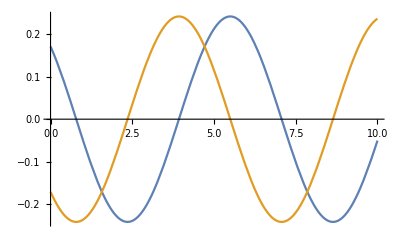

```mathematica
Plot[{Cos[-π/4- t] BesselJ[1,1/2],Sin[-π/4- t] BesselJ[1,1/2]},{t,0,10}]
```

```mathematica
dot[p[1],S[0],S[0],p[1]]
```

```mathematica
(v.e v.e) cosh[L[Y[ν],Subscript[D, a] Y[μ1]]L[Y[ν],Subscript[D, b] Y[μ2]] Subscript[γ, a,b] k[μ1]k[μ2]]+(v.e k.S.e) sinch[L[Y[ν],Subscript[D, a] Y[μ1]]L[Y[ν],Subscript[D, b] Y[μ2]] Subscript[γ, a,b] k[μ1]k[μ2]]
```

```mathematica
c[1](v.e v.e)L[Y[ν],Subscript[D, a] Y[μ1]]L[Y[ν],Subscript[D, b] Y[μ2]] Subscript[γ, a,b] k[μ1]k[μ2] L[Y[ν],Subscript[D, a] Y[μ1]]L[Y[ν],Subscript[D, b] Y[μ2]] Subscript[γ, a,b] k[μ1]k[μ2]
```

```mathematica
dot[p[1],S[0],S[0],p[1]]//expandFS;
%/. dot[p[0],p[1]]->0/.dot[a[0],p[0]]->0/.dot[p[1],p[1]]->0/.dot[p[0],p[0]]->1
```

-dot[a[0],p[1]]^2

```mathematica
k.S.S.k
```

```mathematica
DSolve[r^2 D[D[X[r],r],r]+r D[X[r],r]+Exp[X[r]X[r]]X[r]==0,X[r],r]
```

{Solve[Log[r]+1/(√(-ⅇ^(K[2]^2)+2 C[1]))K[2]1X[r]==C[2],X[r]],Solve[Log[r]+-1/(√(-ⅇ^(K[3]^2)+2 C[1]))K[3]1X[r]==C[2],X[r]]}

```mathematica
Element[n,Integers]
```

n∈ℤ

```mathematica
Assuming[Element[n,Integers],DSolve[r^2 D[D[X[r],r],r]+r D[X[r],r]- 3^2 X[r]==0,X[r],r]//Simplify]
```

{{X[r]→(C[1]+r^6 C[2])/r^3}}

```mathematica
sola=DSolve[r^2 D[D[X[r],r],r]+r D[X[r],r]-r^2(- w^2+e[1])X[r]- 4^2 X[r]==0,X[r],r]
```

{{X[r]→BesselJ[4,ⅈ r √(-w^2+e[1])] C[1]+BesselY[4,-ⅈ r √(-w^2+e[1])] C[2]}}

```mathematica
ta=Assuming[eps>0,X[r]/.sola/.C[2]->0/.f->w^2+eps^2//Simplify]
```

{BesselJ[4,ⅈ eps r] C[1]}

```mathematica
Series[ta,{eps,0,4}]
```

{1/384 r^4 C[1] eps^4+O[eps]^5}

```mathematica
solX=α[n] r^n Exp[I n ϕ]Exp[I e[n,1] t]+αbar[n] r^n Exp[-I n ϕ]Exp[I e[n,2] t]
```

ⅇ^(ⅈ n ϕ+ⅈ t e[n,1]) r^n α[n]+ⅇ^(-ⅈ n ϕ+ⅈ t e[n,2]) r^n αbar[n]

```mathematica
D[solX,t]solX/.e[n,2]->-e[n,1]//Expand
```

ⅈ ⅇ^(2 ⅈ n ϕ+2 ⅈ t e[n,1]) r^(2 n) e[n,1] α[n]^2-ⅈ ⅇ^(-2 ⅈ n ϕ-2 ⅈ t e[n,1]) r^(2 n) e[n,1] αbar[n]^2

# Solution of EOM

## Bulk EOM

```mathematica
ClearAll[EOMOp]
EOMOp[fun_]:=r D[fun,{t,2}]-r D[fun,{r,2}]-D[fun,r]-1/r D[fun,{θ,2}]+r χ fun
```

```mathematica
Sum[c[m,id]Sin[Sqrt[χ]t+m θ]Subscript[f, m][r]+d[m,id]Cos[Sqrt[χ]t+m θ]Subscript[f, m][r],{m,1,10}]
```

Cos[θ+t √χ] d[1,id] f_1[r]+c[1,id] Sin[θ+t √χ] f_1[r]+Cos[2 θ+t √χ] d[2,id] f_2[r]+c[2,id] Sin[2 θ+t √χ] f_2[r]+Cos[3 θ+t √χ] d[3,id] f_3[r]+c[3,id] Sin[3 θ+t √χ] f_3[r]+Cos[4 θ+t √χ] d[4,id] f_4[r]+c[4,id] Sin[4 θ+t √χ] f_4[r]+Cos[5 θ+t √χ] d[5,id] f_5[r]+c[5,id] Sin[5 θ+t √χ] f_5[r]+Cos[6 θ+t √χ] d[6,id] f_6[r]+c[6,id] Sin[6 θ+t √χ] f_6[r]+Cos[7 θ+t √χ] d[7,id] f_7[r]+c[7,id] Sin[7 θ+t √χ] f_7[r]+Cos[8 θ+t √χ] d[8,id] f_8[r]+c[8,id] Sin[8 θ+t √χ] f_8[r]+Cos[9 θ+t √χ] d[9,id] f_9[r]+c[9,id] Sin[9 θ+t √χ] f_9[r]+Cos[10 θ+t √χ] d[10,id] f_10[r]+c[10,id] Sin[10 θ+t √χ] f_10[r]

```mathematica
DSolve[EOMOp[Sin[Sqrt[χ]t+0 θ]f[r]]==0,f[r],r]
DSolve[EOMOp[Sin[Sqrt[χ]t+2θ]f[r]]==0,f[r],r]
```

{{f[r]→C[2]+C[1] Log[r]}}

{{f[r]→C[1]/r^2+r^2 C[2]}}

```mathematica
Y Y Y
```

Y^3

```mathematica
DSolve[EOMOp[Sin[2/a t+2θ]f[r]]==0/.χ->4/a^2,f[r],r]
```

{{f[r]→C[1]/r^2+r^2 C[2]}}

```mathematica
ClearAll[Ysol,Ysol0]
Ysol[m_,id_]:= β[c,m,id] Cos[m/a t+m θ] r^m/a^(m-1)+ β[s,m,id] Sin[m/a t+m θ] r^m/a^(m-1)
Ysol0[m_,id_]:= β[c,m,id] Cos[1/a t+m θ] r^m/a^(m-1)+ β[s,m,id] Sin[1/a t+m θ] r^m/a^(m-1)
```

```mathematica
ta=Integrate[Cos[f[1]/a t+ θ]Cos[f[2]/a t+ θ]Cos[f[3]/a t+ θ]Cos[f[4]/a t+ θ]Cos[f[5]/a t+ θ]Cos[f[6]/a t+ θ],{θ,0,2π}]
```

1/16 π (Cos[(t (f[1]+f[2]+f[3]-f[4]-f[5]-f[6]))/a]+Cos[(t (f[1]+f[2]-f[3]+f[4]-f[5]-f[6]))/a]+Cos[(t (f[1]-f[2]+f[3]+f[4]-f[5]-f[6]))/a]+Cos[(t (f[1]+f[2]-f[3]-f[4]+f[5]-f[6]))/a]+Cos[(t (f[1]-f[2]+f[3]-f[4]+f[5]-f[6]))/a]+Cos[(t (f[1]-f[2]-f[3]+f[4]+f[5]-f[6]))/a]+Cos[(t (f[1]+f[2]-f[3]-f[4]-f[5]+f[6]))/a]+Cos[(t (f[1]-f[2]+f[3]-f[4]-f[5]+f[6]))/a]+Cos[(t (f[1]-f[2]-f[3]+f[4]-f[5]+f[6]))/a]+Cos[(t (f[1]-f[2]-f[3]-f[4]+f[5]+f[6]))/a])

```mathematica
(ta/.Cos->G//CasesG)/.G[f__]:>(0==f/.a->1/.t->1)//Solve
```

{{f[2]→f[1],f[3]→f[1],f[4]→f[1],f[5]→f[1],f[6]→f[1]}}

```mathematica
Integrate[r D[Ysol[μ],t]Ysol[ν]/.m->2//Expand,{r,0,a},{θ,0,2π}]
```

0

```mathematica
ta0=Integrate[r Ysol[ν[1]]Ysol[ν[2]]/.m->1//Expand,{θ,0,2π}]//Expand;
ta0/.β[f__,ν[i_]]:>dot[β[f],k]//Simplify
```

2 π r Ysol[ν[1]] Ysol[ν[2]]

```mathematica
ampOdd=Integrate[r D[(Ysol[1,ν[1]]+1/Sqrt[3] Ysol[3,ν[1]]),t](Ysol[1,ν[2]]+1/Sqrt[3] Ysol[3,ν[2]])(Ysol[1,ν[3]]+1/Sqrt[3] Ysol[3,ν[3]])(Ysol[1,ν[4]]+1/Sqrt[3] Ysol[3,ν[4]])//Expand,{θ,0,2π}]//Expand;
ampOdd/.β[f__,ν[1]]:>dot[β[f],ε]/.β[f__,ν[i_]]:>dot[β[f],k]/;i>1//Simplify
```

1/(4 a^9)π r^5 (-3 a^8 dot[k,β[s,1]]^3 dot[ε,β[c,1]]+√3 a^6 r^2 dot[k,β[s,1]]^2 dot[k,β[s,3]] dot[ε,β[c,1]]-2 a^4 r^4 dot[k,β[s,1]] dot[k,β[s,3]]^2 dot[ε,β[c,1]]+√3 a^6 r^2 dot[k,β[s,1]]^3 dot[ε,β[c,3]]-6 a^4 r^4 dot[k,β[s,1]]^2 dot[k,β[s,3]] dot[ε,β[c,3]]-r^8 dot[k,β[s,3]]^3 dot[ε,β[c,3]]-dot[k,β[c,3]]^2 (2 a^4 r^4 dot[k,β[s,1]] dot[ε,β[c,1]]+r^8 dot[k,β[s,3]] dot[ε,β[c,3]])+r^8 dot[k,β[c,3]]^3 dot[ε,β[s,3]]+dot[k,β[c,1]]^3 (3 a^8 dot[ε,β[s,1]]+√3 a^6 r^2 dot[ε,β[s,3]])+a^4 dot[k,β[c,1]] (2 √3 a^2 r^2 dot[k,β[c,3]] dot[k,β[s,1]] dot[ε,β[c,1]]+2 r^4 dot[k,β[c,3]]^2 dot[ε,β[s,1]]+2 √3 a^2 r^2 dot[k,β[s,1]] dot[k,β[s,3]] dot[ε,β[s,1]]+2 r^4 dot[k,β[s,3]]^2 dot[ε,β[s,1]]+3 dot[k,β[s,1]]^2 (a^4 dot[ε,β[s,1]]-√3 a^2 r^2 dot[ε,β[s,3]]))+dot[k,β[c,3]] (r^8 dot[k,β[s,3]]^2 dot[ε,β[s,3]]+dot[k,β[s,1]]^2 (-√3 a^6 r^2 dot[ε,β[s,1]]+6 a^4 r^4 dot[ε,β[s,3]]))-a^4 dot[k,β[c,1]]^2 (3 dot[k,β[s,1]] (a^4 dot[ε,β[c,1]]+√3 a^2 r^2 dot[ε,β[c,3]])+r^2 (dot[k,β[s,3]] (√3 a^2 dot[ε,β[c,1]]+6 r^2 dot[ε,β[c,3]])-dot[k,β[c,3]] (√3 a^2 dot[ε,β[s,1]]+6 r^2 dot[ε,β[s,3]]))))

```mathematica
ta=ampOdd/.β[f__,ν[1]]:>dot[β[f],ε]/.β[f__,ν[i_]]:>dot[β[f],k]/;i>1/.{β[s,3]->c1 β[c,1],β[c,3]->c1 β[s,1]}//Simplify
```

-1/(4 a^9)π r^5 (-3 a^8+4 a^4 c1^2 r^4+c1^4 r^8) (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2) (-dot[k,β[s,1]] dot[ε,β[c,1]]+dot[k,β[c,1]] dot[ε,β[s,1]])

```mathematica
Integrate[ta,{r,0,a}]//Simplify
```

-1/280 a^5 (-35+28 c1^2+5 c1^4) π (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2) (-dot[k,β[s,1]] dot[ε,β[c,1]]+dot[k,β[c,1]] dot[ε,β[s,1]])

```mathematica
Integrate[ta,{r,0,a}]//Simplify
```

-1/280 a^5 (-35+28 c1^2+5 c1^4) π (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2) (-dot[k,β[s,1]] dot[ε,β[c,1]]+dot[k,β[c,1]] dot[ε,β[s,1]])

```mathematica
Solve[(35+168 c1^2+45 c1^4)==105/2 c1,c1]
```

{{c1→Root-0.170-1.90 ⅈRoot[70-105 #1+336 #1^2+90 #1^4&,1]-0.17047931333960517},{c1→Root-0.170+1.90 ⅈRoot[70-105 #1+336 #1^2+90 #1^4&,2]-0.17047931333960517},{c1→Root0.170-0.430 ⅈRoot[70-105 #1+336 #1^2+90 #1^4&,3]0.17047931333960517},{c1→Root0.170+0.430 ⅈRoot[70-105 #1+336 #1^2+90 #1^4&,4]0.17047931333960517}}

```mathematica
Ysol[3,ν[4]]
```

(r^3 Cos[(3 t)/a+3 θ] β[c,3,ν[4]])/a^2+(r^3 Sin[(3 t)/a+3 θ] β[s,3,ν[4]])/a^2

```mathematica
Ysol[1,ν[1]]Ysol[1,ν[2]]Ysol[1,ν[3]]Ysol[3,ν[4]]
```

(r Cos[t/a+θ] β[c,1,ν[1]]+r Sin[t/a+θ] β[s,1,ν[1]]) (r Cos[t/a+θ] β[c,1,ν[2]]+r Sin[t/a+θ] β[s,1,ν[2]]) (r Cos[t/a+θ] β[c,1,ν[3]]+r Sin[t/a+θ] β[s,1,ν[3]]) ((r^3 Cos[(3 t)/a+3 θ] β[c,3,ν[4]])/a^2+(r^3 Sin[(3 t)/a+3 θ] β[s,3,ν[4]])/a^2)

```mathematica
ampEven=Integrate[r( Ysol[1,ν[1]])( Ysol[1,ν[2]])( Ysol[1,ν[3]])( Ysol[1,ν[4]])//Expand,{θ,0,2π}]//Expand;
```

$Aborted

```mathematica
ampEven/.β[f__,ν[i_]]:>dot[β[f],k]//Simplify
```

3/4 π r^5 (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2)^2

```mathematica
ampEven=Integrate[r( Ysol[1,ν[1]]+1/Sqrt[3] Ysol[3,ν[1]])( Ysol[1,ν[2]]+1/Sqrt[3] Ysol[3,ν[2]])( Ysol[1,ν[3]]+ 1/Sqrt[3] Ysol[3,ν[3]])( Ysol[1,ν[4]]+1/Sqrt[3] Ysol[3,ν[4]])//Expand,{θ,0,2π}]//Expand;
```

```mathematica
ampEven/.β[f__,ν[i_]]:>dot[β[f],k]/.{β[c,3]-> c1 β[s,1],β[s,3]->c1  β[c,1]}//Simplify
```

1/(12 a^8)π r^5 ((9 a^8+12 a^4 c1^2 r^4+c1^4 r^8) dot[k,β[c,1]]^4+16 √3 a^6 c1 r^2 dot[k,β[c,1]]^3 dot[k,β[s,1]]+2 (9 a^8+12 a^4 c1^2 r^4+c1^4 r^8) dot[k,β[c,1]]^2 dot[k,β[s,1]]^2-16 √3 a^6 c1 r^2 dot[k,β[c,1]] dot[k,β[s,1]]^3+(9 a^8+12 a^4 c1^2 r^4+c1^4 r^8) dot[k,β[s,1]]^4)

```mathematica
Integrate[(3 π r^5 (25 a^16+20 a^8 c1^2 r^8+c1^4 r^16) (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2)^2)/(100 a^16),{r,0,a}]//Simplify
```

(a^6 (1925+660 c1^2+21 c1^4) π (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2)^2)/15400

```mathematica
Solve[(105+35 √3 c1+84 c1^2+5 c1^4)==(105-105 √3 c1+84 c1^2+5 c1^4) ,c1]
```

{{c1→0}}

```mathematica
1/a^2 π r^7 (dot[k,β[c,1]]^3 dot[k,β[c,3]]-3 dot[k,β[c,1]] dot[k,β[c,3]] dot[k,β[s,1]]^2+3 dot[k,β[c,1]]^2 dot[k,β[s,1]] dot[k,β[s,3]]-dot[k,β[s,1]]^3 dot[k,β[s,3]])/.β[c,3]->- Sqrt[3]β[s,1]/.β[s,3]->1/Sqrt[3] β[c,1]//Simplify
```

(8 π r^7 dot[k,β[c,1]] dot[k,β[s,1]]^3)/(√3 a^2)

## Boundary EOM

```mathematica
Action=a (D[B[t,θ],t]D[B[t,θ],t]-1/a^2 D[B[t,θ],θ]D[B[t,θ],θ]) dθ dt
```

a dt dθ (-(χ B[t,θ]^2)/a^2-((B^(0,1)[t,θ])^2)/a^2+(B^(1,0)[t,θ])^2)

```mathematica
ClearAll[EOMBDOp]
EOMBDOp[fun_]:= D[fun,{t,2}]-1/a^2 D[fun,{θ,2}]
```

```mathematica
ClearAll[Bsol]
Bsol[id_]=a β[c,1,id] Cos[c1/a t+c2 θ]+a  β[s,1,id] Sin[c1/a t+c2 θ]/.Solve[(c1^2-c2^2)==0,c2][[2]]
```

a Cos[(c1 t)/a+c1 θ] β[c,1,id]+a Sin[(c1 t)/a+c1 θ] β[s,1,id]

```mathematica
Integrate[a D[Bsol[μ],t]D[Bsol[ν],t]-a/a^2 D[Bsol[μ],θ]D[Bsol[ν],θ]-χ/a^2 a Bsol[μ]Bsol[ν]//Expand,{θ,0,2π}]//Simplify
```

0

```mathematica
Integrate[a D[Bsol[μ],t]Bsol[ν]/.m->2//Expand,{θ,0,2π}]
```

a^2 π √(1+χ) (β[c,1,ν] β[s,1,μ]-β[c,1,μ] β[s,1,ν])

```mathematica
res=Integrate[a D[Bsol[μ],t]D[Bsol[ν],t]-t1 a/a^2 D[Bsol[μ],θ]D[Bsol[ν],θ]-t2 χ/a^2 a Bsol[μ]Bsol[ν]//Expand,{θ,0,2π}]//Simplify
```

-a π (-1+t1+(-1+t2) χ) (β[c,1,μ] β[c,1,ν]+β[s,1,μ] β[s,1,ν])

```mathematica
res/.t1->0/.t2->0
```

-a π (-1-χ) (β[c,1,μ] β[c,1,ν]+β[s,1,μ] β[s,1,ν])

```mathematica
Coefficient[res,t1]
```

-a π (β[c,1,μ] β[c,1,ν]+β[s,1,μ] β[s,1,ν])

```mathematica
Coefficient[res,t2]
```

-a π χ (β[c,1,μ] β[c,1,ν]+β[s,1,μ] β[s,1,ν])

```mathematica
(D[Bsol[μ[1]],t]D[Bsol[μ[2]],t]-1/a^2 D[Bsol[μ[1]],θ]D[Bsol[μ[2]],θ])//Simplify
```

0

## EOM for S2

```mathematica
ActionS2= (D[Y[t,θ,ϕ],t]D[Y[t,θ,ϕ],t]-1/a^2 D[Y[t,θ,ϕ],θ]D[Y[t,θ,ϕ],θ]-1/(a^2 Sin[θ]^2)D[Y[t,θ,ϕ],ϕ]D[Y[t,θ,ϕ],ϕ]) a Sin[θ]dt dθ dϕ
```

a dt dθ dϕ Sin[θ] (-(Csc[θ]^2 (Y^(0,0,1)[t,θ,ϕ])^2)/a^2-((Y^(0,1,0)[t,θ,ϕ])^2)/a^2+(Y^(1,0,0)[t,θ,ϕ])^2)

```mathematica
ActionS2//Expand
```

-(dt dθ dϕ Csc[θ] (Y^(0,0,1)[t,θ,ϕ])^2)/R-(dt dθ dϕ Sin[θ] (Y^(0,1,0)[t,θ,ϕ])^2)/R+dt dθ dϕ R Sin[θ] (Y^(1,0,0)[t,θ,ϕ])^2

```mathematica
ClearAll[EOMOpS2]
EOMOpS2[fun_]:=-a Sin[θ] D[fun,{t,2}]+ D[ Sin[θ]/a D[fun,θ],θ]+(Csc[θ] D[fun,{ϕ,2}])/a
```

```mathematica
funt=fun[t](SphericalHarmonicY[6,1,θ,ϕ]);
funtest=EOMOpS2[funt]//Simplify;
```

```mathematica
funtest
```

(ⅇ^(ⅈ ϕ) √(273/(2 π)) Cos[θ] (19+12 Cos[2 θ]+33 Cos[4 θ]) Sin[θ]^2 (42 fun[t]+R^2 fun''[t]))/(128 R)

```mathematica
funSol=DSolve[funtest==0,fun[t],t]//Simplify
```

{{fun[t]→C[1] Cos[(√2 t)/R]+C[2] Sin[(√2 t)/R]}}

```mathematica
funtSol=funt/.funSol[[1]]//Simplify
```

-1/2 ⅇ^(-ⅈ ϕ) (1+ⅇ^(2 ⅈ ϕ)) √(3/(2 π)) (C[1] Cos[(√2 t)/R]+C[2] Sin[(√2 t)/R]) Sin[θ]

```mathematica
ClearAll[YS2Sol]
YS2Sol[l_,m_,id_]:= (a β[c,l,m,id] Cos[Sqrt[l(l+1)]/a t+m ϕ]LegendreP[l,m,Cos[θ]]+ a β[s,l,m,id] Sin[Sqrt[l(l+1)]/a t+m ϕ]LegendreP[l,m,Cos[θ]])
```

```mathematica
LegendreP[6,2,Cos[θ]]
```

-105/8 (-1+Cos[θ]^2) (1-18 Cos[θ]^2+33 Cos[θ]^4)

```mathematica
Assuming[(n1|n2)∈Integers&&n1>0&&n2>0, Integrate[Cos[x]^n1 Sin[x]^n2,{x,0,2π}]]
```

((1+(-1)^n1) (1+(-1)^(n1+n2)) Gamma[(1+n1)/2] Gamma[(1+n2)/2])/(2 Gamma[1/2 (2+n1+n2)])

```mathematica
Integrate[Cos[x]^4 Sin[x]^4,{x,0,2π}]
```

(3 π)/64

### Check dY dY G(Z) terms

```mathematica
ClearAll[YSol]
YSol[id_]:=YS2Sol[1,1,id]
```

```mathematica
actionY0=(D[YSol[μ[1]],t]D[YSol[μ[2]],t]-1/a^2 D[YSol[μ[1]],θ]D[YSol[μ[2]],θ]-1/(a^2 Sin[θ]^2)D[YSol[μ[1]],ϕ]D[YSol[μ[2]],ϕ]) a Sin[θ]//Simplify;
```

```mathematica
ta=actionY0 /.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//Expand//Simplify
Integrate[%//Expand,{ϕ,0,2π}];
Integrate[%,{θ,0,π}]
```

-1/8 a Sin[θ] ((2+6 Cos[2 θ]+2 Cos[2 ((√2 t)/a+ϕ)]-Cos[2 ((√2 t)/a-θ+ϕ)]-Cos[2 ((√2 t)/a+θ+ϕ)]) dot[ε,β[c,1,1]]^2+(2+6 Cos[2 θ]-2 Cos[2 ((√2 t)/a+ϕ)]+Cos[2 ((√2 t)/a-θ+ϕ)]+Cos[2 ((√2 t)/a+θ+ϕ)]) dot[ε,β[s,1,1]]^2+8 dot[ε,β[c,1,1]] dot[ε,β[s,1,1]] Sin[θ]^2 Sin[2 ((√2 t)/a+ϕ)])

0

```mathematica
ta/.θ->π/3/.ϕ->π/3/.a->1//FullSimplify
```

1/32 √3 (-12 Cos[π/6+2 √2 t] dot[ε,β[c,1,1]] dot[ε,β[s,1,1]]+dot[ε,β[s,1,1]]^2 (2-3 Cos[2 √2 t]-3 √3 Sin[2 √2 t])+dot[ε,β[c,1,1]]^2 (2+3 Cos[2 √2 t]+3 √3 Sin[2 √2 t]))

```mathematica
actionY2=actionY0 YSol[μ[3]] YSol[μ[4]]/.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//Expand;
Integrate[actionY2//Expand,{ϕ,0,2π}];
Integrate[%,{θ,0,π}]
```

8/15 a^3 π (dot[k,β[s,1,1]] dot[ε,β[c,1,1]]-dot[k,β[c,1,1]] dot[ε,β[s,1,1]])^2

```mathematica
actionY4=actionY0 YSol[μ[3]] YSol[μ[4]]YSol[μ[5]]YSol[μ[6]]/.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//Expand;
Integrate[actionY4//Expand,{ϕ,0,2π}];
Integrate[%,{θ,0,π}]
```

1/(35 a^2)16 π R (dot[k,β[c,1,1]]^2+dot[k,β[s,1,1]]^2) (dot[k,β[s,1,1]] dot[ε,β[c,1,1]]-dot[k,β[c,1,1]] dot[ε,β[s,1,1]])^2

```mathematica
dot[k,S[0],ε]^2//expandFS;
%/.dot[k,k]->0/.dot[k,p[0]]->0/.dot[k,ε]->0/.dot[ε,ε]->0
```

-dot[k,a[0]]^2 dot[ε,p[0]]^2

```mathematica
actionY6=actionY0 YSol[μ[3]] YSol[μ[4]]YSol[μ[5]]YSol[μ[6]]YSol[μ[7]]YSol[μ[8]]/.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//Expand;
```

```mathematica
ta=List@@actionY6/.a->1/.a_ b_:>b/;NumericQ[a]/.dot[f__]:>1//Union;
```

```mathematica
ta[[12]]
```

```mathematica
Timing[Cos[θ]^6 Cos[ϕ]^6 Cos[2 ϕ] Sin[θ]//Integrate[#,{ϕ,0,2π}]&]
```

{0.024873,15/32 π Cos[θ]^6 Sin[θ]}

```mathematica
Timing[ta[[12]]//Integrate[#,{ϕ,0,2π}]&]
```

{0.112635,15/32 π Cos[θ]^6 Sin[θ]}

```mathematica
Integrate[actionY6,{ϕ,0,2π}];
Integrate[%,{θ,0,π}]
```

### Check dX dX G(Z) terms

```mathematica
ampEven=Integrate[a Sin[θ]( YSol[ν[1]])( YSol[ν[2]])( YSol[ν[3]])( YSol[ν[4]])//Expand,{ϕ,0,2π}]//Expand;
ampEven=ampEven/.β[f__,ν[i_]]:>dot[β[f],k];
```

```mathematica
ampEven2=ampEven//Expand//Integrate[#,{θ,0,π}]&
```

```mathematica
ampOdd=Integrate[r D[Ysol[ν[1]],t]Ysol[ν[2]]Ysol[ν[3]]Ysol[ν[4]]/.m->1//Expand,{θ,0,2π}]//Expand;
ampOdd/.β[f__,ν[1]]:>dot[β[f],ε]/.β[f__,ν[i_]]:>dot[β[f],k]/;i>1//Simplify
```

1/(4 a)3 π r^5 (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2) (-dot[k,β[s,1]] dot[ε,β[c,1]]+dot[k,β[c,1]] dot[ε,β[s,1]])

```mathematica
ampEven=Integrate[r Ysol[ν[1]]Ysol[ν[2]]Ysol[ν[3]]Ysol[ν[4]]/.m->1//Expand,{θ,0,2π}]//Expand;
ampEven/.β[f__,ν[i_]]:>dot[β[f],k]//Simplify
```

3/4 π r^5 (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2)^2

## EOM for S2 elliptic

```mathematica
ActionS2= (D[Y[t,θ,ϕ],t]D[Y[t,θ,ϕ],t]-1/(a^2 Cos[θ]^2+c^2 Sin[θ]^2)D[Y[t,θ,ϕ],θ]D[Y[t,θ,ϕ],θ]-1/(a^2 Sin[θ]^2)D[Y[t,θ,ϕ],ϕ]D[Y[t,θ,ϕ],ϕ]) Sqrt[a^2 Cos[θ]^2+c^2 Sin[θ]^2]a Sin[θ]dt dθ dϕ
```

a dt dθ dϕ Sin[θ] √(a^2 Cos[θ]^2+c^2 Sin[θ]^2) (-(Csc[θ]^2 (Y^(0,0,1)[t,θ,ϕ])^2)/a^2-((Y^(0,1,0)[t,θ,ϕ])^2)/(a^2 Cos[θ]^2+c^2 Sin[θ]^2)+(Y^(1,0,0)[t,θ,ϕ])^2)

```mathematica
ActionS2//Expand
```

-(dt dθ dϕ Csc[θ] (Y^(0,0,1)[t,θ,ϕ])^2)/R-(dt dθ dϕ Sin[θ] (Y^(0,1,0)[t,θ,ϕ])^2)/R+dt dθ dϕ R Sin[θ] (Y^(1,0,0)[t,θ,ϕ])^2

```mathematica
ClearAll[EOMOpS2]
EOMOpS2[fun_]:=-Sqrt[a^2 Cos[θ]^2+c^2 Sin[θ]^2]a Sin[θ] D[fun,{t,2}]+ D[ (Sqrt[a^2 Cos[θ]^2+c^2 Sin[θ]^2]a Sin[θ])/(a^2 Cos[θ]^2+c^2 Sin[θ]^2) D[fun,θ],θ]+(Sqrt[a^2 Cos[θ]^2+c^2 Sin[θ]^2]a Sin[θ] D[fun,{ϕ,2}])/(a^2 Sin[θ]^2)
```

```mathematica
funt=fun[θ](Cos[t/a+ϕ]);
funtest=EOMOpS2[funt]//Simplify;
```

```mathematica
funtest
```

(Cos[t/a+ϕ] Sin[θ] (-1/4 (a^2+c^2+(a^2-c^2) Cos[2 θ])^2 Cot[θ]^2 Csc[θ]^2 fun[θ]+a^4 Cot[θ] Csc[θ]^2 fun'[θ]+a^2 (c^2+a^2 Cot[θ]^2) fun''[θ]))/(a (c^2+a^2 Cot[θ]^2) √(a^2 Cos[θ]^2+c^2 Sin[θ]^2))

```mathematica
funtest2=Series[(-1/4 (a^2+c^2+(a^2-c^2) Cos[2 θ])^2 Cot[θ]^2 Csc[θ]^2 fun[θ]+a^4 Cot[θ] Csc[θ]^2 fun'[θ]+a^2 (c^2+a^2 Cot[θ]^2) fun''[θ]),{c,0,2}]//Normal
```

-1/4 (a^2+a^2 Cos[2 θ])^2 Cot[θ]^2 Csc[θ]^2 fun[θ]+a^4 Cot[θ] Csc[θ]^2 fun'[θ]+a^4 Cot[θ]^2 fun''[θ]+c^2 (1/2 (-1+Cos[2 θ]) (a^2+a^2 Cos[2 θ]) Cot[θ]^2 Csc[θ]^2 fun[θ]+a^2 fun''[θ])

```mathematica
funSol=DSolve[funtest2==0,fun[θ],θ]
```

DSolve[-1/4 (a^2+a^2 Cos[2 θ])^2 Cot[θ]^2 Csc[θ]^2 fun[θ]+a^4 Cot[θ] Csc[θ]^2 fun'[θ]+a^4 Cot[θ]^2 fun''[θ]+c^2 (1/2 (-1+Cos[2 θ]) (a^2+a^2 Cos[2 θ]) Cot[θ]^2 Csc[θ]^2 fun[θ]+a^2 fun''[θ])==0,fun[θ],θ]

```mathematica
funtSol=funt/.funSol[[1]]//Simplify
```

-1/2 ⅇ^(-ⅈ ϕ) (1+ⅇ^(2 ⅈ ϕ)) √(3/(2 π)) (C[1] Cos[(√2 t)/R]+C[2] Sin[(√2 t)/R]) Sin[θ]

```mathematica
ClearAll[YS2Sol]
YS2Sol[l_,m_,id_]:= (β[c,l,m,id] Cos[Sqrt[l(l+1)]/a t+m ϕ]LegendreP[l,m,Cos[θ]]+ β[s,l,m,id] Sin[Sqrt[l(l+1)]/a t+m ϕ]LegendreP[l,m,Cos[θ]])
```

```mathematica
LegendreP[7,1,Cos[θ]]//FullSimplify
```

-7/16 (-5+135 Cos[θ]^2-495 Cos[θ]^4+429 Cos[θ]^6) √(Sin[θ]^2)

### Check dY dY G(Z) terms

```mathematica
ClearAll[YSol]
YSol[id_]:=YS2Sol[1,1,id]
```

```mathematica
actionY0=(D[YSol[μ[1]],t]D[YSol[μ[2]],t]-1/a^2 D[YSol[μ[1]],θ]D[YSol[μ[2]],θ]-1/(a^2 Sin[θ]^2)D[YSol[μ[1]],ϕ]D[YSol[μ[2]],ϕ]) a Sin[θ]//Simplify;
```

```mathematica
actionY0 /.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//Expand;
Integrate[%//Expand,{ϕ,0,2π}];
Integrate[%,{θ,0,π}]
```

0

```mathematica
actionY2=actionY0 YSol[μ[3]] YSol[μ[4]]/.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//Expand;
Integrate[actionY2//Expand,{ϕ,0,2π}];
Integrate[%,{θ,0,π}]
```

1/(15 a^2)8 π R (dot[k,β[s,1,1]] dot[ε,β[c,1,1]]-dot[k,β[c,1,1]] dot[ε,β[s,1,1]])^2

```mathematica
actionY4=actionY0 YSol[μ[3]] YSol[μ[4]]YSol[μ[5]]YSol[μ[6]]/.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//Expand;
Integrate[actionY4//Expand,{ϕ,0,2π}];
Integrate[%,{θ,0,π}]
```

1/(35 a^2)16 π R (dot[k,β[c,1,1]]^2+dot[k,β[s,1,1]]^2) (dot[k,β[s,1,1]] dot[ε,β[c,1,1]]-dot[k,β[c,1,1]] dot[ε,β[s,1,1]])^2

### Check dX dX G(Z) terms

```mathematica
ampEven=Integrate[a Sin[θ]( YSol[ν[1]])( YSol[ν[2]])( YSol[ν[3]])( YSol[ν[4]])//Expand,{ϕ,0,2π}]//Expand;
ampEven=ampEven/.β[f__,ν[i_]]:>dot[β[f],k];
```

```mathematica
ampEven2=ampEven//Expand//Integrate[#,{θ,0,π}]&
```

```mathematica
ampOdd=Integrate[r D[Ysol[ν[1]],t]Ysol[ν[2]]Ysol[ν[3]]Ysol[ν[4]]/.m->1//Expand,{θ,0,2π}]//Expand;
ampOdd/.β[f__,ν[1]]:>dot[β[f],ε]/.β[f__,ν[i_]]:>dot[β[f],k]/;i>1//Simplify
```

1/(4 a)3 π r^5 (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2) (-dot[k,β[s,1]] dot[ε,β[c,1]]+dot[k,β[c,1]] dot[ε,β[s,1]])

```mathematica
ampEven=Integrate[r Ysol[ν[1]]Ysol[ν[2]]Ysol[ν[3]]Ysol[ν[4]]/.m->1//Expand,{θ,0,2π}]//Expand;
ampEven/.β[f__,ν[i_]]:>dot[β[f],k]//Simplify
```

3/4 π r^5 (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2)^2

## EOM for conformal flat space

```mathematica
ActionCF= (D[Y[t,ρ,ϕ],t]D[Y[t,ρ,ϕ],t]-1/f[ρ/a] D[Y[t,ρ,ϕ],ρ]D[Y[t,ρ,ϕ],ρ]-1/f[ρ/a] 1/ρ^2 D[Y[t,ρ,ϕ],ϕ]D[Y[t,ρ,ϕ],ϕ]) f[ρ/a]ρ dt dρ dϕ
```

dt dρ dϕ ρ f[ρ/a] (-((Y^(0,0,1)[t,ρ,ϕ])^2)/(ρ^2 f[ρ/a])-((Y^(0,1,0)[t,ρ,ϕ])^2)/f[ρ/a]+(Y^(1,0,0)[t,ρ,ϕ])^2)

```mathematica
ActionS2//Expand
```

-(dt dθ dϕ Csc[θ] (Y^(0,0,1)[t,θ,ϕ])^2)/R-(dt dθ dϕ Sin[θ] (Y^(0,1,0)[t,θ,ϕ])^2)/R+dt dθ dϕ R Sin[θ] (Y^(1,0,0)[t,θ,ϕ])^2

```mathematica
ClearAll[EOMOpCF]
EOMOpCF[fr_]:=-f[ρ/a]ρ D[fr,{t,2}]+ D[ ρ D[fr,ρ],ρ]+1/ρ D[fr,{ϕ,2}]
```

```mathematica
funt=fun[ρ]Cos[1/a t+ϕ];
funtest=EOMOpCF[funt]/.f[ρ/a]->(ρ/a)^2//Simplify;
```

```mathematica
funtest
```

(Cos[t/a+ϕ] ((-a^4+ρ^4) fun[ρ]+a^4 ρ (fun'[ρ]+ρ fun''[ρ])))/(a^4 ρ)

```mathematica
funSol=DSolve[funtest==0,fun[ρ],ρ]//Simplify
```

{{fun[ρ]→(ⅇ^(-(ⅈ ρ^2)/(2 a^2)) (2 C[1]-ⅈ a^2 ⅇ^((ⅈ ρ^2)/a^2) C[2]))/(2 ρ)}}

```mathematica
funSol/.C[2]->-2/a^2 I C[1]//ExpToTrig//FullSimplify
```

{{fun[ρ]→-(2 ⅈ C[1] Sin[ρ^2/(2 a^2)])/ρ}}

```mathematica
Integrate[Sin[ρ^2/(2 a^2)]/ρ Sin[ρ^2/(2 a^2)]/ρ Sin[ρ^2/(2 a^2)]/ρ Sin[ρ^2/(2 a^2)]/ρ,{ρ,0,a}]
```

-1/(24 a^3)(3-4 Cos[1]+Cos[2]-8 √(2 π) FresnelC[√(2/π)]+8 √π FresnelC[2/(√π)]+8 Sin[1]-4 Sin[2])

```mathematica
funtSol=funt/.funSol[[1]]//Simplify
```

-1/2 ⅇ^(-ⅈ ϕ) (1+ⅇ^(2 ⅈ ϕ)) √(3/(2 π)) (C[1] Cos[(√2 t)/R]+C[2] Sin[(√2 t)/R]) Sin[θ]

```mathematica
ClearAll[YS2Sol]
YS2Sol[l_,m_,id_]:= (β[c,l,m,id] Cos[Sqrt[l(l+1)]/a t+m ϕ]LegendreP[l,m,Cos[θ]]+ β[s,l,m,id] Sin[Sqrt[l(l+1)]/a t+m ϕ]LegendreP[l,m,Cos[θ]])
```

### Check dY dY G(Z) terms

```mathematica
ClearAll[YSol]
YSol[id_]:=YS2Sol[1,1,id]
```

```mathematica
actionY0=(D[YSol[μ[1]],t]D[YSol[μ[2]],t]-1/a^2 D[YSol[μ[1]],θ]D[YSol[μ[2]],θ]-1/(a^2 Sin[θ]^2)D[YSol[μ[1]],ϕ]D[YSol[μ[2]],ϕ]) a Sin[θ]//Simplify;
```

```mathematica
actionY0 /.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//Expand;
Integrate[%//Expand,{ϕ,0,2π}];
Integrate[%,{θ,0,π}]
```

0

```mathematica
actionY2=actionY0 YSol[μ[3]] YSol[μ[4]]/.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//Expand;
Integrate[actionY2//Expand,{ϕ,0,2π}];
Integrate[%,{θ,0,π}]
```

1/(15 a^2)8 π R (dot[k,β[s,1,1]] dot[ε,β[c,1,1]]-dot[k,β[c,1,1]] dot[ε,β[s,1,1]])^2

```mathematica
actionY4=actionY0 YSol[μ[3]] YSol[μ[4]]YSol[μ[5]]YSol[μ[6]]/.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//Expand;
Integrate[actionY4//Expand,{ϕ,0,2π}];
Integrate[%,{θ,0,π}]
```

1/(35 a^2)16 π R (dot[k,β[c,1,1]]^2+dot[k,β[s,1,1]]^2) (dot[k,β[s,1,1]] dot[ε,β[c,1,1]]-dot[k,β[c,1,1]] dot[ε,β[s,1,1]])^2

### Check dX dX G(Z) terms

```mathematica
ampEven=Integrate[a Sin[θ]( YSol[ν[1]])( YSol[ν[2]])( YSol[ν[3]])( YSol[ν[4]])//Expand,{ϕ,0,2π}]//Expand;
ampEven=ampEven/.β[f__,ν[i_]]:>dot[β[f],k];
```

```mathematica
ampEven2=ampEven//Expand//Integrate[#,{θ,0,π}]&
```

```mathematica
ampOdd=Integrate[r D[Ysol[ν[1]],t]Ysol[ν[2]]Ysol[ν[3]]Ysol[ν[4]]/.m->1//Expand,{θ,0,2π}]//Expand;
ampOdd/.β[f__,ν[1]]:>dot[β[f],ε]/.β[f__,ν[i_]]:>dot[β[f],k]/;i>1//Simplify
```

1/(4 a)3 π r^5 (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2) (-dot[k,β[s,1]] dot[ε,β[c,1]]+dot[k,β[c,1]] dot[ε,β[s,1]])

```mathematica
ampEven=Integrate[r Ysol[ν[1]]Ysol[ν[2]]Ysol[ν[3]]Ysol[ν[4]]/.m->1//Expand,{θ,0,2π}]//Expand;
ampEven/.β[f__,ν[i_]]:>dot[β[f],k]//Simplify
```

3/4 π r^5 (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2)^2

# S2*R model

## EOM for S2

```mathematica
ActionS2= (D[Y[t,θ,ϕ],t]D[Y[t,θ,ϕ],t]-1/a^2 D[Y[t,θ,ϕ],θ]D[Y[t,θ,ϕ],θ]-1/(a^2 Sin[θ]^2)D[Y[t,θ,ϕ],ϕ]D[Y[t,θ,ϕ],ϕ]) a^2 Sin[θ]dt dθ dϕ
```

a^2 dt dθ dϕ Sin[θ] (-(Csc[θ]^2 (Y^(0,0,1)[t,θ,ϕ])^2)/a^2-((Y^(0,1,0)[t,θ,ϕ])^2)/a^2+(Y^(1,0,0)[t,θ,ϕ])^2)

```mathematica
ClearAll[EOMOpS2]
EOMOpS2[fun_]:=-a Sin[θ] D[fun,{t,2}]+ D[ Sin[θ]/a D[fun,θ],θ]+(Csc[θ] D[fun,{ϕ,2}])/a
```

```mathematica
ClearAll[YS2Sol,YS2SolSim]
YS2Sol[l_,m_,id_]:=  a Sqrt[Sqrt[l(l+1)]] Sqrt[2l+1]/Sqrt[l(l+1)] Sqrt[((l-m)!!)/((l+m)!!)] 1/Sqrt[Product[l-mm,{mm,-m+1,m-1,2}]](β[c,l,m,id] Cos[Sqrt[l(l+1)]/a t+m ϕ](Assuming[Sin[θ]>0,LegendreP[l,m,Cos[θ]]//Simplify])+ β[s,l,m,id] Sin[Sqrt[l(l+1)]/a t+m ϕ](Assuming[Sin[θ]>0,LegendreP[l,m,Cos[θ]]//Simplify]))
YS2SolSim[l_,m_,id_]:=  a c[l,m](β[c,l,m,id] Cos[Sqrt[l(l+1)]/a t+m ϕ](Assuming[Sin[θ]>0,LegendreP[l,m,Cos[θ]]//Simplify])+ β[s,l,m,id] Sin[Sqrt[l(l+1)]/a t+m ϕ](Assuming[Sin[θ]>0,LegendreP[l,m,Cos[θ]]//Simplify]))
```

### test EOM

```mathematica
funt=fun[t](SphericalHarmonicY[1,1,θ,ϕ]);
funtest=EOMOpS2[funt]//Simplify;
```

```mathematica
funtest
```

(ⅇ^(ⅈ ϕ) √(3/(2 π)) Sin[θ]^2 (2 fun[t]+a^2 fun''[t]))/(2 a)

```mathematica
funSol=DSolve[funtest==0,fun[t],t]//Simplify
```

{{fun[t]→C[1] Cos[(√2 t)/a]+C[2] Sin[(√2 t)/a]}}

```mathematica
funtSol=funt/.funSol[[1]]//Simplify
```

-1/2 ⅇ^(ⅈ ϕ) √(3/(2 π)) (C[1] Cos[(√2 t)/a]+C[2] Sin[(√2 t)/a]) Sin[θ]

### Check dY dY G(Z) terms

```mathematica
actionY0=(D[YSol[μ[1]],t]D[YSol[μ[2]],t]-1/a^2 D[YSol[μ[1]],θ]D[YSol[μ[2]],θ]-1/(a^2 Sin[θ]^2)D[YSol[μ[1]],ϕ]D[YSol[μ[2]],ϕ]) a Sin[θ]//Simplify;
```

```mathematica
ta=actionY0 /.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//Expand;
Integrate[%//Expand,{ϕ,0,2π}]
Integrate[%,{θ,0,π}]
```

-9 a π c[2,2]^2 (3+5 Cos[2 θ]) (dot[ε,β[c,2,2]]^2+dot[ε,β[s,2,2]]^2) Sin[θ]^3

0

```mathematica
actionY8=actionY0  Product[YSol[μ[jj]],{jj,3,4}]/.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//TrigToExp//Expand;
2π*actionY8/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Simplify
```

1/35840 9 a^3 ⅇ^(-ⅈ ((2 √6 t)/a+9 θ+4 ϕ)) π c[2,2]^4 (-524288 ⅇ^(ⅈ ((2 √6 t)/a+9 θ+4 ϕ)) dot[k,β[c,2,2]] dot[k,β[s,2,2]] dot[ε,β[c,2,2]] dot[ε,β[s,2,2]]+dot[k,β[s,2,2]]^2 (3 (-105 ⅈ+735 ⅈ ⅇ^(2 ⅈ θ)-2205 ⅈ ⅇ^(4 ⅈ θ)+3675 ⅈ ⅇ^(6 ⅈ θ)-3675 ⅈ ⅇ^(8 ⅈ θ)+2205 ⅈ ⅇ^(10 ⅈ θ)-735 ⅈ ⅇ^(12 ⅈ θ)+105 ⅈ ⅇ^(14 ⅈ θ)+735 ⅈ ⅇ^(2 ⅈ ((2 √6 t)/a+3 θ+4 ϕ))+77824 ⅇ^(ⅈ ((2 √6 t)/a+9 θ+4 ϕ))-3675 ⅈ ⅇ^((4 ⅈ (√6 t+3 a θ+2 a ϕ))/a)+3675 ⅈ ⅇ^((2 ⅈ (2 √6 t+5 a θ+4 a ϕ))/a)+2205 ⅈ ⅇ^((2 ⅈ (2 √6 t+7 a θ+4 a ϕ))/a)+105 ⅈ ⅇ^((2 ⅈ (2 √6 t+9 a θ+4 a ϕ))/a)-2205 ⅈ ⅇ^((4 ⅈ (√6 t+2 a (θ+ϕ)))/a)-735 ⅈ ⅇ^((4 ⅈ (√6 t+2 a (2 θ+ϕ)))/a)-105 ⅈ ⅇ^((4 ⅈ (√6 t+a (θ+2 ϕ)))/a)) dot[ε,β[c,2,2]]^2+7 (45 ⅈ-315 ⅈ ⅇ^(2 ⅈ θ)+945 ⅈ ⅇ^(4 ⅈ θ)-1575 ⅈ ⅇ^(6 ⅈ θ)+1575 ⅈ ⅇ^(8 ⅈ θ)-945 ⅈ ⅇ^(10 ⅈ θ)+315 ⅈ ⅇ^(12 ⅈ θ)-45 ⅈ ⅇ^(14 ⅈ θ)-315 ⅈ ⅇ^(2 ⅈ ((2 √6 t)/a+3 θ+4 ϕ))+4096 ⅇ^(ⅈ ((2 √6 t)/a+9 θ+4 ϕ))+1575 ⅈ ⅇ^((4 ⅈ (√6 t+3 a θ+2 a ϕ))/a)-1575 ⅈ ⅇ^((2 ⅈ (2 √6 t+5 a θ+4 a ϕ))/a)-945 ⅈ ⅇ^((2 ⅈ (2 √6 t+7 a θ+4 a ϕ))/a)-45 ⅈ ⅇ^((2 ⅈ (2 √6 t+9 a θ+4 a ϕ))/a)+945 ⅈ ⅇ^((4 ⅈ (√6 t+2 a (θ+ϕ)))/a)+315 ⅈ ⅇ^((4 ⅈ (√6 t+2 a (2 θ+ϕ)))/a)+45 ⅈ ⅇ^((4 ⅈ (√6 t+a (θ+2 ϕ)))/a)) dot[ε,β[s,2,2]]^2)+dot[k,β[c,2,2]]^2 (7 (-45 ⅈ+315 ⅈ ⅇ^(2 ⅈ θ)-945 ⅈ ⅇ^(4 ⅈ θ)+1575 ⅈ ⅇ^(6 ⅈ θ)-1575 ⅈ ⅇ^(8 ⅈ θ)+945 ⅈ ⅇ^(10 ⅈ θ)-315 ⅈ ⅇ^(12 ⅈ θ)+45 ⅈ ⅇ^(14 ⅈ θ)+315 ⅈ ⅇ^(2 ⅈ ((2 √6 t)/a+3 θ+4 ϕ))+4096 ⅇ^(ⅈ ((2 √6 t)/a+9 θ+4 ϕ))-1575 ⅈ ⅇ^((4 ⅈ (√6 t+3 a θ+2 a ϕ))/a)+1575 ⅈ ⅇ^((2 ⅈ (2 √6 t+5 a θ+4 a ϕ))/a)+945 ⅈ ⅇ^((2 ⅈ (2 √6 t+7 a θ+4 a ϕ))/a)+45 ⅈ ⅇ^((2 ⅈ (2 √6 t+9 a θ+4 a ϕ))/a)-945 ⅈ ⅇ^((4 ⅈ (√6 t+2 a (θ+ϕ)))/a)-315 ⅈ ⅇ^((4 ⅈ (√6 t+2 a (2 θ+ϕ)))/a)-45 ⅈ ⅇ^((4 ⅈ (√6 t+a (θ+2 ϕ)))/a)) dot[ε,β[c,2,2]]^2+3 (105 ⅈ-735 ⅈ ⅇ^(2 ⅈ θ)+2205 ⅈ ⅇ^(4 ⅈ θ)-3675 ⅈ ⅇ^(6 ⅈ θ)+3675 ⅈ ⅇ^(8 ⅈ θ)-2205 ⅈ ⅇ^(10 ⅈ θ)+735 ⅈ ⅇ^(12 ⅈ θ)-105 ⅈ ⅇ^(14 ⅈ θ)-735 ⅈ ⅇ^(2 ⅈ ((2 √6 t)/a+3 θ+4 ϕ))+77824 ⅇ^(ⅈ ((2 √6 t)/a+9 θ+4 ϕ))+3675 ⅈ ⅇ^((4 ⅈ (√6 t+3 a θ+2 a ϕ))/a)-3675 ⅈ ⅇ^((2 ⅈ (2 √6 t+5 a θ+4 a ϕ))/a)-2205 ⅈ ⅇ^((2 ⅈ (2 √6 t+7 a θ+4 a ϕ))/a)-105 ⅈ ⅇ^((2 ⅈ (2 √6 t+9 a θ+4 a ϕ))/a)+2205 ⅈ ⅇ^((4 ⅈ (√6 t+2 a (θ+ϕ)))/a)+735 ⅈ ⅇ^((4 ⅈ (√6 t+2 a (2 θ+ϕ)))/a)+105 ⅈ ⅇ^((4 ⅈ (√6 t+a (θ+2 ϕ)))/a)) dot[ε,β[s,2,2]]^2))

```mathematica
Integrate[actionY6[[332]],{ϕ,0,2π}]
Integrate[%,{θ,0,π}]
```

Part::partd: Part specification actionY6⟦332⟧ is longer than depth of object.

2 π actionY6⟦332⟧

2 π^2 actionY6⟦332⟧

```mathematica
Integrate[actionY6,{ϕ,0,2π}];
Integrate[%,{θ,0,π}]
```

2 actionY6 π^2

### amp 3

```mathematica
ClearAll[YSolv]
YSolv[k_]:=YS2SolSim[1,1,ν[1]]/.β[cs_,f__]:>dot[β[cs],k]
```

```mathematica
measure=a^2 Sin[θ]/(4π a^2);
ampodd=2measure*dot[v[0],ϵ[1]](D[YSolv[ϵ[1]],t])YSolv[k[1]]^(2j-1)/.Sin[f__]:>0/;Flatten[Cases[f,ϕ]//Union]=={ϕ}/.Cos[f_]:>Cos[f/.t->0];
```

```mathematica
Assuming[Element[j,Integers]&&j>=0,ampoddRes=ampodd//Integrate[#,{ϕ,0,2π}]&//Integrate[#,{θ,0,π}]&]
```

(2 √2 c[1,1] (a c[1,1] dot[k[1],β[c]])^(-1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]])/(1+2 j)

```mathematica
ampeven=measure*(dot[v[0],ϵ[1]]^2 YSolv[k[1]]^(2j)+(D[YSolv[ϵ[1]],t]D[YSolv[ϵ[1]],t]-1/a^2 D[YSolv[ϵ[1]],θ]D[YSolv[ϵ[1]],θ]-1/(a^2 Sin[θ]^2)D[YSolv[ϵ[1]],ϕ]D[YSolv[ϵ[1]],ϕ])YSolv[k[1]]^(2j))/.dot[β[c],ϵ[1]]->0/.dot[k[1],β[s]]->0/.Sin[f_]:>Sin[f/.t->0]/.Cos[f_]:>Cos[f/.t->0]//PowerExpand;
```

```mathematica
ampeven=ampeven/.Cos[θ]^2->1-Sin[θ]^2/.Sin[ϕ]^2->1-Cos[ϕ]^2//Expand
```

((-1)^(2 j) a^(2 j) c[1,1]^(2 j) Cos[ϕ]^(2 j) dot[k[1],β[c]]^(2 j) dot[v[0],ϵ[1]]^2 Sin[θ]^(1+2 j))/(4 π)+((-1)^(1+2 j) a^(2 j) c[1,1]^(2+2 j) Cos[ϕ]^(2 j) dot[k[1],β[c]]^(2 j) dot[β[s],ϵ[1]]^2 Sin[θ]^(1+2 j))/(4 π)+((-1)^(2 j) a^(2 j) c[1,1]^(2+2 j) Cos[ϕ]^(2 j) dot[k[1],β[c]]^(2 j) dot[β[s],ϵ[1]]^2 Sin[θ]^(3+2 j))/(4 π)+((-1)^(2 j) a^(2 j) c[1,1]^(2+2 j) Cos[ϕ]^(2+2 j) dot[k[1],β[c]]^(2 j) dot[β[s],ϵ[1]]^2 Sin[θ]^(3+2 j))/(4 π)

```mathematica
Assuming[Element[j,Integers]&&j>=0,ampevenRes=ampeven/.Power[Cos[ϕ],ni_]:>Integrate[Power[Cos[ϕ],ni],{ϕ,0,2π}]/.Power[Sin[θ],ni_]:>Integrate[Power[Sin[θ],ni],{θ,0,π}]]
```

Integrate::idiv: Integral of Cos[ϕ]^(2+2 j) does not converge on {0,π}.

((-1)^(2 j) a^(2 j) c[1,1]^(2 j) dot[k[1],β[c]]^(2 j) dot[v[0],ϵ[1]]^2 Gamma[1/2+j])/(2 Gamma[3/2+j])+((-1)^(1+2 j) a^(2 j) c[1,1]^(2+2 j) dot[k[1],β[c]]^(2 j) dot[β[s],ϵ[1]]^2 Gamma[1/2+j])/(2 Gamma[3/2+j])+((-1)^(2 j) a^(2 j) c[1,1]^(2+2 j) dot[k[1],β[c]]^(2 j) dot[β[s],ϵ[1]]^2 Gamma[3/2+j])/(2 Gamma[5/2+j])+((-1)^(2 j) a^(2 j) c[1,1]^(2+2 j) dot[k[1],β[c]]^(2 j) dot[β[s],ϵ[1]]^2 Gamma[1/2+j] Gamma[2+j])/(2 Gamma[1+j] Gamma[5/2+j])

```mathematica
Assuming[Element[j,Integers]&&j>=0,ampevenRes/.β[s]->0//FullSimplify]
tta=ampevenRes/.v[0]->0//FullSimplify//Factor
```

((a c[1,1] dot[k[1],β[c]])^(2 j) dot[v[0],ϵ[1]]^2)/(1+2 j)

(2 (-1)^(2 j) a^(2 j) j c[1,1]^(2+2 j) dot[k[1],β[c]]^(2 j) dot[β[s],ϵ[1]]^2)/((1+2 j) (3+2 j))

```mathematica
ampevenRes/.β[s]->v[0]//Simplify//FullSimplify//Factor
ampoddRes//FullSimplify
```

((-1)^(2 j) a^(2 j) c[1,1]^(2 j) (3+2 j+2 j c[1,1]^2) dot[k[1],β[c]]^(2 j) dot[v[0],ϵ[1]]^2)/((1+2 j) (3+2 j))

(2 √2 c[1,1] (a c[1,1] dot[k[1],β[c]])^(-1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]])/(1+2 j)

```mathematica
Assuming[Element[j,Integers]&&j>=0,ta=Integrate[Cos[ϕ]^(2 j),{ϕ,0,2π}];
tb=Integrate[Sin[θ]^(1+2 j),{θ,0,π}];]
```

## Amp 3

```mathematica
repid2dot={v[μ[1]]->dot[v,ϵ],v[μ[2]]->dot[v,ϵ],β[f__,μ[1]]:>dot[β[f],ϵ],β[f__,μ[2]]:>dot[β[f],ϵ],β[f__,μ[i_]]:>dot[β[f],k]/;i>1};
ClearAll[YSol]
YSol[id_]:=YS2Sol[1,1,id]
```

```mathematica
actionZ0=(D[v[μ[1]]t,t]D[v[μ[2]]t,t]+2D[v[μ[1]]t,t]D[YSol[μ[2]],t]+D[YSol[μ[1]],t]D[YSol[μ[2]],t]-1/a^2 D[YSol[μ[1]],θ]D[YSol[μ[2]],θ]-1/(a^2 Sin[θ]^2)D[YSol[μ[1]],ϕ]D[YSol[μ[2]],ϕ]) a^2 Sin[θ];
Assuming[Sin[θ]>0,actionZ0=actionZ0//Simplify//Expand;]
```

```mathematica
actionZ0a=actionZ0/.repid2dot//TrigToExp//Expand;
```

```mathematica
(2π)/(4 π a^2)*actionZ0a/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Simplify
```

dot[v,ϵ]^2

```mathematica
actionZ1=actionZ0 Product[YSol[μ[jj]],{jj,3,3}]/.repid2dot//TrigToExp//Expand;
(2π)/(4 π a^2)*actionZ2/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand
```

-a dot[k,β[s,1,1]] dot[v,ϵ] dot[ϵ,β[c,1,1]]+a dot[k,β[c,1,1]] dot[v,ϵ] dot[ϵ,β[s,1,1]]

```mathematica
ClearAll[Y2a]
Y2a[fg_]:=Module[{res},res=(2π)/(4 π a^2)fg/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
res=res/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand;
res=res/.v->t v[0]//Collect[#,t,Simplify]&;
res=res/.dot[k,β[c,ids__]]^2+dot[k,β[s,ids__]]^2:>(-dot[k,a]^2)/a^2/.(dot[k,β[s,ids__]] dot[ϵ,β[c,ids__]]-dot[k,β[c,ids__]] dot[ϵ,β[s,ids__]])->dot[k,S[0],ϵ]/.dot[k,S[0],ϵ]^2->(-dot[k,a]^2)/a^2 dot[ϵ,v[0]]^2//Simplify
]
```

```mathematica
actionZ2=actionZ0 Product[-I YSol[μ[jj]],{jj,3,4}]/.repid2dot//TrigToExp//Expand;
(2π)/(4 π a^2)*actionZ2/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand;
%/.v->t v[0]//Collect[#,t,Simplify]&
%/.dot[k,β[c,ids__]]^2+dot[k,β[s,ids__]]^2:>(-dot[k,a]^2)/a^2/.(dot[k,β[s,ids__]] dot[ϵ,β[c,ids__]]-dot[k,β[c,ids__]] dot[ϵ,β[s,ids__]])->dot[k,S[0],ϵ]/.dot[k,S[0],ϵ]^2->(-dot[k,a]^2)/a^2 dot[ϵ,v[0]]^2//Simplify
```

-(a^2 t^2 (dot[k,β[c,1,1]]^2+dot[k,β[s,1,1]]^2) dot[ϵ,v[0]]^2)/(2 √2)-3/20 a^2 (dot[k,β[s,1,1]] dot[ϵ,β[c,1,1]]-dot[k,β[c,1,1]] dot[ϵ,β[s,1,1]])^2

1/20 (3+5 √2 t^2) dot[a,k]^2 dot[ϵ,v[0]]^2

```mathematica
Monitor[res=Table[actionZ2=actionZ0 Product[-I YSol[μ[jj]],{jj,3,kk}]/.repid2dot//TrigToExp//Expand;
Y2a[actionZ2],{kk,4,20,2}];,kk]
```

```mathematica
Monitor[resOdd=Table[actionZ2=actionZ0 Product[-I YSol[μ[jj]],{jj,3,kk}]/.repid2dot//TrigToExp//Expand;
Y2a[actionZ2],{kk,3,19,2}];,kk]
```

```mathematica
resOdd/.(dot[k,β[s,ids__]] dot[ϵ,β[c,ids__]]-dot[k,β[c,ids__]] dot[ϵ,β[s,ids__]])->dot[k,S[0],ϵ]//Simplify
```

{ⅈ a t dot[ϵ,v[0]] dot[k,S[0],ϵ],(9 ⅈ a t dot[a,k]^2 dot[ϵ,v[0]] dot[k,S[0],ϵ])/(10 √2),27/56 ⅈ a t dot[a,k]^4 dot[ϵ,v[0]] dot[k,S[0],ϵ],(9 ⅈ a t dot[a,k]^6 dot[ϵ,v[0]] dot[k,S[0],ϵ])/(16 √2),243/704 ⅈ a t dot[a,k]^8 dot[ϵ,v[0]] dot[k,S[0],ϵ],(729 ⅈ a t dot[a,k]^10 dot[ϵ,v[0]] dot[k,S[0],ϵ])/(1664 √2),(729 ⅈ a t dot[a,k]^12 dot[ϵ,v[0]] dot[k,S[0],ϵ])/2560,(6561 ⅈ a t dot[a,k]^14 dot[ϵ,v[0]] dot[k,S[0],ϵ])/(17408 √2),(19683 ⅈ a t dot[a,k]^16 dot[ϵ,v[0]] dot[k,S[0],ϵ])/77824}

```mathematica
2/(4 π a^2)ampoddRes/.j->3
```

27/56 a^5 dot[k[1],β[c]]^5 dot[v[0],ϵ[1]] dot[β[s],ϵ[1]]

```mathematica
Coefficient[res,t^2]
```

{(dot[a,k]^2 dot[ϵ,v[0]]^2)/(2 √2),9/40 dot[a,k]^4 dot[ϵ,v[0]]^2,(27 dot[a,k]^6 dot[ϵ,v[0]]^2)/(112 √2),9/64 dot[a,k]^8 dot[ϵ,v[0]]^2,(243 dot[a,k]^10 dot[ϵ,v[0]]^2)/(1408 √2),(729 dot[a,k]^12 dot[ϵ,v[0]]^2)/6656,(729 dot[a,k]^14 dot[ϵ,v[0]]^2)/(5120 √2),(6561 dot[a,k]^16 dot[ϵ,v[0]]^2)/69632,(19683 dot[a,k]^18 dot[ϵ,v[0]]^2)/(155648 √2)}

```mathematica
res
```

{1/20 (3+5 √2 t^2) dot[a,k]^2 dot[ϵ,v[0]]^2,9/280 (3 √2+7 t^2) dot[a,k]^4 dot[ϵ,v[0]]^2,27/224 (1+√2 t^2) dot[a,k]^6 dot[ϵ,v[0]]^2,9/704 (6 √2+11 t^2) dot[a,k]^8 dot[ϵ,v[0]]^2,(243 (15+13 √2 t^2) dot[a,k]^10 dot[ϵ,v[0]]^2)/36608,(729 (3 √2+5 t^2) dot[a,k]^12 dot[ϵ,v[0]]^2)/33280,(729 (21+17 √2 t^2) dot[a,k]^14 dot[ϵ,v[0]]^2)/174080,(6561 (12 √2+19 t^2) dot[a,k]^16 dot[ϵ,v[0]]^2)/1323008,(19683 (9+7 √2 t^2) dot[a,k]^18 dot[ϵ,v[0]]^2)/2179072}

```mathematica
ampevenRes/.j->2/. dot[β[s],ϵ[1]]-> dot[v[0],ϵ[1]]//Simplify
```

(9 (5+7 √2) a^4 dot[k[1],β[c]]^4 dot[v[0],ϵ[1]]^2)/(280 √2)

```mathematica
res2=Table[res[[jj/2-1]]((2 √2)/3)^(jj/2-1)(jj-1),{jj,4,20,2}]
```

{1/20 (3+5 √2 t^2) dot[a,k]^2 dot[ϵ,v[0]]^2,9/280 (3 √2+7 t^2) dot[a,k]^4 dot[ϵ,v[0]]^2,27/224 (1+√2 t^2) dot[a,k]^6 dot[ϵ,v[0]]^2,9/704 (6 √2+11 t^2) dot[a,k]^8 dot[ϵ,v[0]]^2,(243 (15+13 √2 t^2) dot[a,k]^10 dot[ϵ,v[0]]^2)/36608,(729 (3 √2+5 t^2) dot[a,k]^12 dot[ϵ,v[0]]^2)/33280,(729 (21+17 √2 t^2) dot[a,k]^14 dot[ϵ,v[0]]^2)/174080,(6561 (12 √2+19 t^2) dot[a,k]^16 dot[ϵ,v[0]]^2)/1323008,(19683 (9+7 √2 t^2) dot[a,k]^18 dot[ϵ,v[0]]^2)/2179072}

```mathematica
Sum[1/(((2 √2)/3)^(jj/2-1)(jj-1))dot[a,k]^(jj-2)/((jj-2)!),{jj,4,∞,2}]//Simplify
```

-1+(2^(3/4) Sinh[(√3 dot[a,k])/2^(3/4)])/(√3 dot[a,k])

```mathematica
Series[%/.dot[a,k]->t dot[a,k],{t,0,6}]
```

(dot[a,k]^2 t^2)/(4 √2)+3/80 dot[a,k]^4 t^4+(9 dot[a,k]^6 t^6)/(896 √2)+O[t]^7

```mathematica
Table[1/(((2 √2)/3)^(jj/2-1)(jj-1))dot[a,k]^(jj/2)/((jj/2)!),{jj,4,20,2}]
```

{1/(2 √2),9/40,27/(112 √2),9/64,243/(1408 √2),729/6656,729/(5120 √2),6561/69632,19683/(155648 √2)}

```mathematica
res2=Table[res[[jj/2-1]]((2 √2)/3)^(jj/2-1)(jj-1),{jj,4,20,2}]
```

{((3+5 √2 t^2) dot[a,k]^2 dot[ϵ,v[0]]^2)/(5 √2),1/7 (3 √2+7 t^2) dot[a,k]^4 dot[ϵ,v[0]]^2,((1+√2 t^2) dot[a,k]^6 dot[ϵ,v[0]]^2)/(√2),1/11 (6 √2+11 t^2) dot[a,k]^8 dot[ϵ,v[0]]^2,((15+13 √2 t^2) dot[a,k]^10 dot[ϵ,v[0]]^2)/(13 √2),1/5 (3 √2+5 t^2) dot[a,k]^12 dot[ϵ,v[0]]^2,((21+17 √2 t^2) dot[a,k]^14 dot[ϵ,v[0]]^2)/(17 √2),1/19 (12 √2+19 t^2) dot[a,k]^16 dot[ϵ,v[0]]^2,((9+7 √2 t^2) dot[a,k]^18 dot[ϵ,v[0]]^2)/(7 √2)}

```mathematica
Coefficient[res2,t^2]/.t->0/.dot[f__]:>1
```

{1,1,1,1,1,1,1,1,1}

```mathematica
Table[1/(3^(ii/2-2)(ii-1)),{ii,4,20,2}]
```

{1/3,1/15,1/63,1/243,1/891,1/3159,1/10935,1/37179,1/124659}

```mathematica
168//FactorInteger
297//FactorInteger
```

{{2,3},{3,1},{7,1}}

{{3,3},{11,1}}

## Amp 3 Y22

```mathematica
repid2dot={v[μ[1]]->dot[v,ϵ],v[μ[2]]->dot[v,ϵ],β[f__,μ[1]]:>dot[β[f],ϵ],β[f__,μ[2]]:>dot[β[f],ϵ],β[f__,μ[i_]]:>dot[β[f],k]/;i>1};
ClearAll[YSol]
YSol[id_]:=YS2SolSim[2,2,id]
```

```mathematica
actionZ0=(D[v[μ[1]]t,t]D[v[μ[2]]t,t]) a^2 Sin[θ]
Assuming[Sin[θ]>0,actionZ0=actionZ0//Simplify//Expand;]
```

a^2 Sin[θ] v[μ[1]] v[μ[2]]

```mathematica
actionZ0a=actionZ0/.repid2dot//TrigToExp//Expand;
```

### test

```mathematica
(2π)/(4 π a^2)*actionZ0a/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Simplify
```

dot[v,ϵ]^2

```mathematica
actionZ1=actionZ0 Product[YSol[μ[jj]],{jj,3,6}]/.repid2dot//TrigToExp//Expand;
ta=(2π)/(4 π a^2)*actionZ1/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand//Simplify
```

432/35 a^4 c[2,2]^4 (dot[k,β[c,2,2]]^2+dot[k,β[s,2,2]]^2)^2 dot[v,ϵ]^2

```mathematica
1/(4 π a^2)actionZ1//Integrate[#,{ϕ,0,2π}]&
%//Integrate[#,{θ,0,π}]&
```

243/16 a^4 c[2,2]^4 (dot[k,β[c,2,2]]^2+dot[k,β[s,2,2]]^2)^2 dot[v,ϵ]^2 Sin[θ]^9

432/35 a^4 c[2,2]^4 (dot[k,β[c,2,2]]^2+dot[k,β[s,2,2]]^2)^2 dot[v,ϵ]^2

### continue

```mathematica
ClearAll[Y2a]
Y2a[fg_]:=Module[{res},res=(2π)/(4 π a^2)fg/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
res=res/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand;
res=res/.v->t v[0]//Collect[#,t,Simplify]&;
res=res/.dot[k,β[c,ids__]]^2+dot[k,β[s,ids__]]^2:>(-dot[k,a]^2)/a^2/.(dot[k,β[s,ids__]] dot[ϵ,β[c,ids__]]-dot[k,β[c,ids__]] dot[ϵ,β[s,ids__]])->dot[k,S[0],ϵ]/.dot[k,S[0],ϵ]^2->(-dot[k,a]^2)/a^2 dot[ϵ,v[0]]^2//Simplify
]
```

```mathematica
Monitor[res=Table[actionZ2=actionZ0 Product[-I YSol[μ[jj]],{jj,3,kk}]/.repid2dot//TrigToExp//Expand;
Y2a[actionZ2],{kk,4,20,2}];,kk]
```

```mathematica
432//FactorInteger
```

{{2,4},{3,3}}

```mathematica
Coefficient[res,t^2]
```

{12/5 c[2,2]^2 dot[a,k]^2 dot[ϵ,v[0]]^2,432/35 c[2,2]^4 dot[a,k]^4 dot[ϵ,v[0]]^2,(77760 c[2,2]^6 dot[a,k]^6 dot[ϵ,v[0]]^2)/1001,(1306368 c[2,2]^8 dot[a,k]^8 dot[ϵ,v[0]]^2)/2431,(181398528 c[2,2]^10 dot[a,k]^10 dot[ϵ,v[0]]^2)/46189,(71833817088 c[2,2]^12 dot[a,k]^12 dot[ϵ,v[0]]^2)/2414425,(1245119496192 c[2,2]^14 dot[a,k]^14 dot[ϵ,v[0]]^2)/5386025,(12224809598976 c[2,2]^16 dot[a,k]^16 dot[ϵ,v[0]]^2)/6678671,(7481583474573312 c[2,2]^18 dot[a,k]^18 dot[ϵ,v[0]]^2)/508757585}

```mathematica
res2=Table[res[[jj/2-1]]((2(jj-2)+1)(2(jj-2)-1)!!)/((3)^(jj-2) 2^(jj-2) (jj-2-1)!! (jj-2-1)!!),{jj,4,20,2}]
```

{t^2 c[2,2]^2 dot[a,k]^2 dot[ϵ,v[0]]^2,t^2 c[2,2]^4 dot[a,k]^4 dot[ϵ,v[0]]^2,t^2 c[2,2]^6 dot[a,k]^6 dot[ϵ,v[0]]^2,t^2 c[2,2]^8 dot[a,k]^8 dot[ϵ,v[0]]^2,t^2 c[2,2]^10 dot[a,k]^10 dot[ϵ,v[0]]^2,t^2 c[2,2]^12 dot[a,k]^12 dot[ϵ,v[0]]^2,t^2 c[2,2]^14 dot[a,k]^14 dot[ϵ,v[0]]^2,t^2 c[2,2]^16 dot[a,k]^16 dot[ϵ,v[0]]^2,t^2 c[2,2]^18 dot[a,k]^18 dot[ϵ,v[0]]^2}

```mathematica
((2(jj-2)+1)(2(jj-2)-1)!!)/((3)^(jj-2) 2^(jj-2) (jj-2-1)!! (jj-2-1)!!)//Simplify
```

(6^(2-jj) (-3+2 jj) (-5+2 jj)!!)/((-3+jj)!!)^2

```mathematica
Sum[((3)^(jj-2) 2^(jj-2) (jj-2-1)!! (jj-2-1)!!)/((2(jj-2)+1)(2(jj-2)-1)!!)dot[a,k]^(jj-2)/((jj-2)!),{jj,2,∞,2}]
```

HypergeometricPFQ[{1/2},{3/4,5/4},9/4 dot[a,k]^2]

```mathematica
HypergeometricPFQ[{1/2},{3/4,5/4},1.2+0.001I]//N
HypergeometricPFQ[{1},{1},x]//Simplify
```

1.80378+0.000821858 ⅈ

ⅇ^x

```mathematica
Exp[1234]//N
```

8.30597593736×10^535

```mathematica
Series[%/.dot[a,k]->t dot[a,k],{t,0,6}]
```

(dot[a,k]^2 t^2)/(4 √2)+3/80 dot[a,k]^4 t^4+(9 dot[a,k]^6 t^6)/(896 √2)+O[t]^7

```mathematica
Table[1/(((2 √2)/3)^(jj/2-1)(jj-1))dot[a,k]^(jj/2)/((jj/2)!),{jj,4,20,2}]
```

{1/(2 √2),9/40,27/(112 √2),9/64,243/(1408 √2),729/6656,729/(5120 √2),6561/69632,19683/(155648 √2)}

```mathematica
res2=Table[res[[jj/2-1]]((2 √2)/3)^(jj/2-1)(jj-1),{jj,4,20,2}]
```

{((3+5 √2 t^2) dot[a,k]^2 dot[ϵ,v[0]]^2)/(5 √2),1/7 (3 √2+7 t^2) dot[a,k]^4 dot[ϵ,v[0]]^2,((1+√2 t^2) dot[a,k]^6 dot[ϵ,v[0]]^2)/(√2),1/11 (6 √2+11 t^2) dot[a,k]^8 dot[ϵ,v[0]]^2,((15+13 √2 t^2) dot[a,k]^10 dot[ϵ,v[0]]^2)/(13 √2),1/5 (3 √2+5 t^2) dot[a,k]^12 dot[ϵ,v[0]]^2,((21+17 √2 t^2) dot[a,k]^14 dot[ϵ,v[0]]^2)/(17 √2),1/19 (12 √2+19 t^2) dot[a,k]^16 dot[ϵ,v[0]]^2,((9+7 √2 t^2) dot[a,k]^18 dot[ϵ,v[0]]^2)/(7 √2)}

```mathematica
Coefficient[res2,t^2]/.t->0/.dot[f__]:>1
```

{1,1,1,1,1,1,1,1,1}

```mathematica
Table[1/(3^(ii/2-2)(ii-1)),{ii,4,20,2}]
```

{1/3,1/15,1/63,1/243,1/891,1/3159,1/10935,1/37179,1/124659}

```mathematica
168//FactorInteger
297//FactorInteger
```

{{2,3},{3,1},{7,1}}

{{3,3},{11,1}}

## Amp 3 Y31

```mathematica
repid2dot={v[μ[1]]->dot[v,ϵ],v[μ[2]]->dot[v,ϵ],β[f__,μ[1]]:>dot[β[f],ϵ],β[f__,μ[2]]:>dot[β[f],ϵ],β[f__,μ[i_]]:>dot[β[f],k]/;i>1};
ClearAll[YSol]
YSol[id_]:=YS2SolSim[3,3,id]
```

```mathematica
actionZ0=(D[v[μ[1]]t,t]D[v[μ[2]]t,t]) a^2 Sin[θ]
Assuming[Sin[θ]>0,actionZ0=actionZ0//Simplify//Expand;]
```

a^2 Sin[θ] v[μ[1]] v[μ[2]]

```mathematica
actionZ0a=actionZ0/.repid2dot//TrigToExp//Expand;
```

### test

```mathematica
(2π)/(4 π a^2)*actionZ0a/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Simplify
```

dot[v,ϵ]^2

```mathematica
actionZ1=actionZ0 Product[YSol[μ[jj]],{jj,3,6}]/.repid2dot//TrigToExp//Expand;
ta=(2π)/(4 π a^2)*actionZ1/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand//Simplify
```

432/35 a^4 c[2,2]^4 (dot[k,β[c,2,2]]^2+dot[k,β[s,2,2]]^2)^2 dot[v,ϵ]^2

```mathematica
1/(4 π a^2)actionZ1//Integrate[#,{ϕ,0,2π}]&
%//Integrate[#,{θ,0,π}]&
```

243/16 a^4 c[2,2]^4 (dot[k,β[c,2,2]]^2+dot[k,β[s,2,2]]^2)^2 dot[v,ϵ]^2 Sin[θ]^9

432/35 a^4 c[2,2]^4 (dot[k,β[c,2,2]]^2+dot[k,β[s,2,2]]^2)^2 dot[v,ϵ]^2

### continue

```mathematica
ClearAll[Y2a]
Y2a[fg_]:=Module[{res},res=(2π)/(4 π a^2)fg/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
res=res/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand;
res=res/.v->t v[0]//Collect[#,t,Simplify]&;
res=res/.dot[k,β[c,ids__]]^2+dot[k,β[s,ids__]]^2:>(-dot[k,a]^2)/a^2/.(dot[k,β[s,ids__]] dot[ϵ,β[c,ids__]]-dot[k,β[c,ids__]] dot[ϵ,β[s,ids__]])->dot[k,S[0],ϵ]/.dot[k,S[0],ϵ]^2->(-dot[k,a]^2)/a^2 dot[ϵ,v[0]]^2//Simplify
]
```

```mathematica
lm=1
Assuming[Element[n,Integers]&&n>0,ta=(LegendreP[lm+1,lm,Cos[θ]])^(2n)Sin[θ]//Integrate[#,{θ,0,π}]&//FullSimplify;]
Assuming[Element[n,Integers]&&n>0,tb=(Cos[lm ϕ] )^(2n)//Integrate[#,{ϕ,0,2π}]&;]
AmpRes=Sum[1/(4 π)ta*tb/((2n)!) x^(2n),{n,0,∞}]
```

1

HypergeometricPFQ[{1/2},{3/4,5/4},(9 x^2)/16]

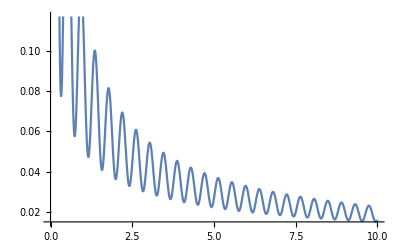

```mathematica
Plot[{HypergeometricPFQ[{1/3,2/3},{1/2,5/6,7/6},-(225 x^2)/4]},{x,0,10}]
```

```mathematica
HypergeometricPFQ[{2,2,2},{3,3,3,3},(297675 x^2)/1024]/.x->20//N
```

8.14345×10^282

```mathematica
Series[HypergeometricPFQ[{2,2,2},{3,3,3,3},(297675 x^2)/1024],{x,0,920}]//Normal;
%/.x->20//N
```

8.14345×10^282

# D2*R model

## EOM for S2

```mathematica
ActionS2= (D[Y[t,θ,ϕ],t]D[Y[t,θ,ϕ],t]-1/a^2 D[Y[t,θ,ϕ],θ]D[Y[t,θ,ϕ],θ]-1/(a^2 Sin[θ]^4)D[Y[t,θ,ϕ],ϕ]D[Y[t,θ,ϕ],ϕ]) a^2 Sin[θ]dt dθ dϕ
```

a^2 dt dθ dϕ Sin[θ] (-(Csc[θ]^4 (Y^(0,0,1)[t,θ,ϕ])^2)/a^2-((Y^(0,1,0)[t,θ,ϕ])^2)/a^2+(Y^(1,0,0)[t,θ,ϕ])^2)

```mathematica
ClearAll[EOMOpS2]
EOMOpS2[fun_]:=-a Sin[θ] D[fun,{t,2}]+ D[ Sin[θ]/a D[fun,θ],θ]+D[fun,{ϕ,2}]/(Sin[θ]^3 a)
```

```mathematica
ClearAll[YS2Sol,YS2SolSim]
YS2Sol[l_,m_,id_]:=  a Sqrt[Sqrt[l(l+1)]] Sqrt[2l+1]/Sqrt[l(l+1)] Sqrt[((l-m)!!)/((l+m)!!)] 1/Sqrt[Product[l-mm,{mm,-m+1,m-1,2}]](β[c,l,m,id] Cos[Sqrt[l(l+1)]/a t+m ϕ](Assuming[Sin[θ]>0,LegendreP[l,m,Cos[θ]]//Simplify])+ β[s,l,m,id] Sin[Sqrt[l(l+1)]/a t+m ϕ](Assuming[Sin[θ]>0,LegendreP[l,m,Cos[θ]]//Simplify]))
YS2SolSim[l_,m_,id_]:=  a c[l,m](β[c,l,m,id] Cos[Sqrt[l(l+1)]/a t+m ϕ](Assuming[Sin[θ]>0,LegendreP[l,m,Cos[θ]]//Simplify])+ β[s,l,m,id] Sin[Sqrt[l(l+1)]/a t+m ϕ](Assuming[Sin[θ]>0,LegendreP[l,m,Cos[θ]]//Simplify]))
```

```mathematica
LegendreP[2,2,Cos[θ]]//FullSimplify
```

3 Sin[θ]^2

```mathematica
LegendreP[2,1,Cos[θ]]//FullSimplify
```

-3 Cos[θ] √(Sin[θ]^2)

```mathematica
(Assuming[Sin[θ]>0,LegendreP[7,3,Cos[θ]]//Simplify])
```

-315/8 (3-66 Cos[θ]^2+143 Cos[θ]^4) Sin[θ]^3

```mathematica
10395//FactorInteger
```

{{3,3},{5,1},{7,1},{11,1}}

```mathematica
(*Table[
YSol[id_]:=YS2Sol[kk,12,id];
actionZ0=(2D[v[μ[1]]t,t]D[YSol[μ[2]],t]) a^2 Sin[θ];
Assuming[Sin[θ]>0,actionZ0=actionZ0//Simplify//Expand;]
actionZ0a=actionZ0/.repid2dot//TrigToExp//Expand;
actionZ2=actionZ0 Product[YSol[μ[jj]],{jj,3,3}]/.repid2dot//TrigToExp//Expand;
actionZ2a=(2π)/(4 π a^2)*actionZ2/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
actionZ2b=actionZ2a/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand;
((actionZ2b/.dot[k,β[s,f__]]:>0/.dot[f__]:>1/.a->1)==1//Solve)[[2]]/.Rule[f1_,f2_]:>Rule[f1,f2^-2],{kk,12,16}]*)
```

{{c[12,12]→1},{c[13,12]→1},{c[14,12]→1},{c[15,12]→1},{c[16,12]→1}}

```mathematica
l=1;
m1=1;
w=Sqrt[2];
Assuming[Sin[θ]>0,test=EOMOpS2[Cos[(w1 t)/a-m1 ϕ]f2[θ]]//FullSimplify]
```

(Cos[(t w1)/a-ϕ] Sin[θ] ((w1^2-Csc[θ]^4) f2[θ]+Cot[θ] f2'[θ]+f2''[θ]))/a

```mathematica
DSolve[test==0,f2[θ],θ]
```

DSolve[(Cos[(t w1)/a-ϕ] Sin[θ] ((w1^2-Csc[θ]^4) f2[θ]+Cot[θ] f2'[θ]+f2''[θ]))/a==0,f2[θ],θ]

```mathematica
funt=fun[t](SphericalHarmonicY[1,1,θ,ϕ]);
funtest=EOMOpS2[funt]//Simplify;
```

```mathematica
funtest
```

(ⅇ^(ⅈ ϕ) √(3/(2 π)) Sin[θ]^2 (2 fun[t]+a^2 fun''[t]))/(2 a)

```mathematica
funSol=DSolve[funtest==0,fun[t],t]//Simplify
```

{{fun[t]→C[1] Cos[(√2 t)/a]+C[2] Sin[(√2 t)/a]}}

```mathematica
funtSol=funt/.funSol[[1]]//Simplify
```

-1/2 ⅇ^(-ⅈ ϕ) (1+ⅇ^(2 ⅈ ϕ)) √(3/(2 π)) (C[1] Cos[(√2 t)/R]+C[2] Sin[(√2 t)/R]) Sin[θ]

### Check dY dY G(Z) terms

```mathematica
actionY0=(D[YSol[μ[1]],t]D[YSol[μ[2]],t]-1/a^2 D[YSol[μ[1]],θ]D[YSol[μ[2]],θ]-1/(a^2 Sin[θ]^2)D[YSol[μ[1]],ϕ]D[YSol[μ[2]],ϕ]) a Sin[θ]//Simplify;
```

```mathematica
ta=actionY0 /.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//Expand;
Integrate[%//Expand,{ϕ,0,2π}]
Integrate[%,{θ,0,π}]
```

1/4 a π (dot[ε,β[c,1,1]]^2+dot[ε,β[s,1,1]]^2) (Sin[θ]-3 Sin[3 θ])

0

```mathematica
actionY8=actionY0  Product[YSol[μ[jj]],{jj,3,4}]/.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//TrigToExp//Expand;
2π*actionY8/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Simplify
```

8/15 a^3 π (dot[k,β[s,1,1]] dot[ε,β[c,1,1]]-dot[k,β[c,1,1]] dot[ε,β[s,1,1]])^2

```mathematica
Integrate[actionY6[[332]],{ϕ,0,2π}]
Integrate[%,{θ,0,π}]
```

(1575 ⅈ ⅇ^(3 ⅈ θ) π dot[k,β[c,1,1]]^2 dot[k,β[s,1,1]]^4 dot[ε,β[c,1,1]]^2)/(8192 a)

-(525 π dot[k,β[c,1,1]]^2 dot[k,β[s,1,1]]^4 dot[ε,β[c,1,1]]^2)/(4096 a)

```mathematica
Integrate[actionY6,{ϕ,0,2π}];
Integrate[%,{θ,0,π}]
```

1/(21 a)8 π (dot[k,β[c,1,1]]^2+dot[k,β[s,1,1]]^2)^2 (dot[k,β[s,1,1]] dot[ε,β[c,1,1]]-dot[k,β[c,1,1]] dot[ε,β[s,1,1]])^2

### Check dX dX G(Z) terms

```mathematica
ampEven=Integrate[a Sin[θ]( YSol[ν[1]])( YSol[ν[2]])( YSol[ν[3]])( YSol[ν[4]])//Expand,{ϕ,0,2π}]//Expand;
ampEven=ampEven/.β[f__,ν[i_]]:>dot[β[f],k];
```

```mathematica
ampEven2=ampEven//Expand//Integrate[#,{θ,0,π}]&
```

```mathematica
ampOdd=Integrate[r D[Ysol[ν[1]],t]Ysol[ν[2]]Ysol[ν[3]]Ysol[ν[4]]/.m->1//Expand,{θ,0,2π}]//Expand;
ampOdd/.β[f__,ν[1]]:>dot[β[f],ε]/.β[f__,ν[i_]]:>dot[β[f],k]/;i>1//Simplify
```

1/(4 a)3 π r^5 (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2) (-dot[k,β[s,1]] dot[ε,β[c,1]]+dot[k,β[c,1]] dot[ε,β[s,1]])

```mathematica
ampEven=Integrate[r Ysol[ν[1]]Ysol[ν[2]]Ysol[ν[3]]Ysol[ν[4]]/.m->1//Expand,{θ,0,2π}]//Expand;
ampEven/.β[f__,ν[i_]]:>dot[β[f],k]//Simplify
```

3/4 π r^5 (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2)^2

### amp dX dY terms

```mathematica
ClearAll[YSolv]
YSolv[k_]:=YS2Sol[1,1,ν[1]]/.β[cs_,f__]:>dot[β[cs],k]
```

```mathematica
measure=a^2 Sin[θ];
ampodd=measure*dot[v[0],ϵ[1]](D[YSolv[ϵ[1]],t])YSolv[k[1]]^(2j-1)/.Sin[f__]:>0/;Flatten[Cases[f,ϕ]//Union]=={ϕ}/.Cos[f_]:>Cos[f/.t->0]//PowerExpand;
```

```mathematica
Assuming[Element[j,Integers]&&j>=0,ampoddRes=ampodd//Integrate[#,{ϕ,0,2π}]&//Integrate[#,{θ,0,π}]&]
```

(2^(5/2-(3 j)/2) 3^j a^(1+2 j) π dot[k[1],β[c]]^(-1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]])/(1+2 j)

```mathematica
Sum[ampoddRes 1/(4π a^2(2j-1)!),{j,1,∞}]
```

1/(3 a^2 dot[k[1],β[c]]^2)√2 dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] (3 a Cosh[(√3 a dot[k[1],β[c]])/2^(3/4)] dot[k[1],β[c]]-2^(3/4) √3 Sinh[(√3 a dot[k[1],β[c]])/2^(3/4)])

```mathematica
Assuming[Element[j,Integers]&&j>=0,ta=Integrate[Cos[ϕ]^(2 j),{ϕ,0,2π}];
tb=Integrate[Sin[θ]^(1+2 j),{θ,0,π}];]
```

```mathematica
Sum[ta*tb x^(2j-1)/((2j-1)!),{j,1,∞}]//FullSimplify
```

(4 π (x Cosh[x]-Sinh[x]))/x^2

```mathematica
D[Sinh[x]/x,x]//FullSimplify
```

```mathematica
Integrate[(x Cosh[x]-Sinh[x])/x^2,x]
```

Sinh[x]/x

## Amp 3

```mathematica
repid2dot={v[μ[1]]->dot[v,ϵ],v[μ[2]]->dot[v,ϵ],β[f__,μ[1]]:>dot[β[f],ϵ],β[f__,μ[2]]:>dot[β[f],ϵ],β[f__,μ[i_]]:>dot[β[f],k]/;i>1};
ClearAll[YSol]
YSol[id_]:=YS2Sol[1,1,id]
```

```mathematica
actionZ0=(D[v[μ[1]]t,t]D[v[μ[2]]t,t]+2D[v[μ[1]]t,t]D[YSol[μ[2]],t]+D[YSol[μ[1]],t]D[YSol[μ[2]],t]-1/a^2 D[YSol[μ[1]],θ]D[YSol[μ[2]],θ]-1/(a^2 Sin[θ]^2)D[YSol[μ[1]],ϕ]D[YSol[μ[2]],ϕ]) a^2 Sin[θ];
Assuming[Sin[θ]>0,actionZ0=actionZ0//Simplify//Expand;]
```

```mathematica
actionZ0a=actionZ0/.repid2dot//TrigToExp//Expand;
```

```mathematica
(2π)/(4 π a^2)*actionZ0a/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Simplify
```

dot[v,ϵ]^2

```mathematica
actionZ1=actionZ0 Product[YSol[μ[jj]],{jj,3,3}]/.repid2dot//TrigToExp//Expand;
(2π)/(4 π a^2)*actionZ2/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand
```

-a dot[k,β[s,1,1]] dot[v,ϵ] dot[ϵ,β[c,1,1]]+a dot[k,β[c,1,1]] dot[v,ϵ] dot[ϵ,β[s,1,1]]

```mathematica
ClearAll[Y2a]
Y2a[fg_]:=Module[{res},res=(2π)/(4 π a^2)fg/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
res=res/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand;
res=res/.v->t v[0]//Collect[#,t,Simplify]&;
res=res/.dot[k,β[c,ids__]]^2+dot[k,β[s,ids__]]^2:>(-dot[k,a]^2)/a^2/.(dot[k,β[s,ids__]] dot[ϵ,β[c,ids__]]-dot[k,β[c,ids__]] dot[ϵ,β[s,ids__]])->dot[k,S[0],ϵ]/.dot[k,S[0],ϵ]^2->(-dot[k,a]^2)/a^2 dot[ϵ,v[0]]^2//Simplify
]
```

```mathematica
actionZ2=actionZ0 Product[-I YSol[μ[jj]],{jj,3,4}]/.repid2dot//TrigToExp//Expand;
(2π)/(4 π a^2)*actionZ2/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand;
%/.v->t v[0]//Collect[#,t,Simplify]&
%/.dot[k,β[c,ids__]]^2+dot[k,β[s,ids__]]^2:>(-dot[k,a]^2)/a^2/.(dot[k,β[s,ids__]] dot[ϵ,β[c,ids__]]-dot[k,β[c,ids__]] dot[ϵ,β[s,ids__]])->dot[k,S[0],ϵ]/.dot[k,S[0],ϵ]^2->(-dot[k,a]^2)/a^2 dot[ϵ,v[0]]^2//Simplify
```

-(a^2 t^2 (dot[k,β[c,1,1]]^2+dot[k,β[s,1,1]]^2) dot[ϵ,v[0]]^2)/(2 √2)-3/20 a^2 (dot[k,β[s,1,1]] dot[ϵ,β[c,1,1]]-dot[k,β[c,1,1]] dot[ϵ,β[s,1,1]])^2

1/20 (3+5 √2 t^2) dot[a,k]^2 dot[ϵ,v[0]]^2

```mathematica
Monitor[res=Table[actionZ2=actionZ0 Product[-I YSol[μ[jj]],{jj,3,kk}]/.repid2dot//TrigToExp//Expand;
Y2a[actionZ2],{kk,4,20,2}];,kk]
```

```mathematica
Monitor[resOdd=Table[actionZ2=actionZ0 Product[-I YSol[μ[jj]],{jj,3,kk}]/.repid2dot//TrigToExp//Expand;
Y2a[actionZ2],{kk,3,19,2}];,kk]
```

```mathematica
resOdd/.(dot[k,β[s,ids__]] dot[ϵ,β[c,ids__]]-dot[k,β[c,ids__]] dot[ϵ,β[s,ids__]])->dot[k,S[0],ϵ]//Simplify
```

{ⅈ a t dot[ϵ,v[0]] dot[k,S[0],ϵ],(9 ⅈ a t dot[a,k]^2 dot[ϵ,v[0]] dot[k,S[0],ϵ])/(10 √2),27/56 ⅈ a t dot[a,k]^4 dot[ϵ,v[0]] dot[k,S[0],ϵ],(9 ⅈ a t dot[a,k]^6 dot[ϵ,v[0]] dot[k,S[0],ϵ])/(16 √2),243/704 ⅈ a t dot[a,k]^8 dot[ϵ,v[0]] dot[k,S[0],ϵ],(729 ⅈ a t dot[a,k]^10 dot[ϵ,v[0]] dot[k,S[0],ϵ])/(1664 √2),(729 ⅈ a t dot[a,k]^12 dot[ϵ,v[0]] dot[k,S[0],ϵ])/2560,(6561 ⅈ a t dot[a,k]^14 dot[ϵ,v[0]] dot[k,S[0],ϵ])/(17408 √2),(19683 ⅈ a t dot[a,k]^16 dot[ϵ,v[0]] dot[k,S[0],ϵ])/77824}

```mathematica
2/(4 π a^2)ampoddRes/.j->3
```

27/56 a^5 dot[k[1],β[c]]^5 dot[v[0],ϵ[1]] dot[β[s],ϵ[1]]

```mathematica
Coefficient[res,t^2]
```

{(dot[a,k]^2 dot[ϵ,v[0]]^2)/(2 √2),9/40 dot[a,k]^4 dot[ϵ,v[0]]^2,(27 dot[a,k]^6 dot[ϵ,v[0]]^2)/(112 √2),9/64 dot[a,k]^8 dot[ϵ,v[0]]^2,(243 dot[a,k]^10 dot[ϵ,v[0]]^2)/(1408 √2),(729 dot[a,k]^12 dot[ϵ,v[0]]^2)/6656,(729 dot[a,k]^14 dot[ϵ,v[0]]^2)/(5120 √2),(6561 dot[a,k]^16 dot[ϵ,v[0]]^2)/69632,(19683 dot[a,k]^18 dot[ϵ,v[0]]^2)/(155648 √2)}

```mathematica
res2=Table[res[[jj/2-1]]((2 √2)/3)^(jj/2-1)(jj-1),{jj,4,20,2}]
```

{1/20 (3+5 √2 t^2) dot[a,k]^2 dot[ϵ,v[0]]^2,9/280 (3 √2+7 t^2) dot[a,k]^4 dot[ϵ,v[0]]^2,27/224 (1+√2 t^2) dot[a,k]^6 dot[ϵ,v[0]]^2,9/704 (6 √2+11 t^2) dot[a,k]^8 dot[ϵ,v[0]]^2,(243 (15+13 √2 t^2) dot[a,k]^10 dot[ϵ,v[0]]^2)/36608,(729 (3 √2+5 t^2) dot[a,k]^12 dot[ϵ,v[0]]^2)/33280,(729 (21+17 √2 t^2) dot[a,k]^14 dot[ϵ,v[0]]^2)/174080,(6561 (12 √2+19 t^2) dot[a,k]^16 dot[ϵ,v[0]]^2)/1323008,(19683 (9+7 √2 t^2) dot[a,k]^18 dot[ϵ,v[0]]^2)/2179072}

```mathematica
Sum[1/(((2 √2)/3)^(jj/2-1)(jj-1))dot[a,k]^(jj-2)/((jj-2)!),{jj,4,∞,2}]//Simplify
```

-1+(2^(3/4) Sinh[(√3 dot[a,k])/2^(3/4)])/(√3 dot[a,k])

```mathematica
Series[%/.dot[a,k]->t dot[a,k],{t,0,6}]
```

(dot[a,k]^2 t^2)/(4 √2)+3/80 dot[a,k]^4 t^4+(9 dot[a,k]^6 t^6)/(896 √2)+O[t]^7

```mathematica
Table[1/(((2 √2)/3)^(jj/2-1)(jj-1))dot[a,k]^(jj/2)/((jj/2)!),{jj,4,20,2}]
```

{1/(2 √2),9/40,27/(112 √2),9/64,243/(1408 √2),729/6656,729/(5120 √2),6561/69632,19683/(155648 √2)}

```mathematica
res2=Table[res[[jj/2-1]]((2 √2)/3)^(jj/2-1)(jj-1),{jj,4,20,2}]
```

{((3+5 √2 t^2) dot[a,k]^2 dot[ϵ,v[0]]^2)/(5 √2),1/7 (3 √2+7 t^2) dot[a,k]^4 dot[ϵ,v[0]]^2,((1+√2 t^2) dot[a,k]^6 dot[ϵ,v[0]]^2)/(√2),1/11 (6 √2+11 t^2) dot[a,k]^8 dot[ϵ,v[0]]^2,((15+13 √2 t^2) dot[a,k]^10 dot[ϵ,v[0]]^2)/(13 √2),1/5 (3 √2+5 t^2) dot[a,k]^12 dot[ϵ,v[0]]^2,((21+17 √2 t^2) dot[a,k]^14 dot[ϵ,v[0]]^2)/(17 √2),1/19 (12 √2+19 t^2) dot[a,k]^16 dot[ϵ,v[0]]^2,((9+7 √2 t^2) dot[a,k]^18 dot[ϵ,v[0]]^2)/(7 √2)}

```mathematica
Coefficient[res2,t^2]/.t->0/.dot[f__]:>1
```

{1,1,1,1,1,1,1,1,1}

```mathematica
Table[1/(3^(ii/2-2)(ii-1)),{ii,4,20,2}]
```

{1/3,1/15,1/63,1/243,1/891,1/3159,1/10935,1/37179,1/124659}

```mathematica
168//FactorInteger
297//FactorInteger
```

{{2,3},{3,1},{7,1}}

{{3,3},{11,1}}

## Amp 3 Y22

```mathematica
repid2dot={v[μ[1]]->dot[v,ϵ],v[μ[2]]->dot[v,ϵ],β[f__,μ[1]]:>dot[β[f],ϵ],β[f__,μ[2]]:>dot[β[f],ϵ],β[f__,μ[i_]]:>dot[β[f],k]/;i>1};
ClearAll[YSol]
YSol[id_]:=YS2SolSim[2,2,id]
```

```mathematica
actionZ0=(D[v[μ[1]]t,t]D[v[μ[2]]t,t]) a^2 Sin[θ]
Assuming[Sin[θ]>0,actionZ0=actionZ0//Simplify//Expand;]
```

a^2 Sin[θ] v[μ[1]] v[μ[2]]

```mathematica
actionZ0a=actionZ0/.repid2dot//TrigToExp//Expand;
```

### test

```mathematica
(2π)/(4 π a^2)*actionZ0a/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Simplify
```

dot[v,ϵ]^2

```mathematica
actionZ1=actionZ0 Product[YSol[μ[jj]],{jj,3,6}]/.repid2dot//TrigToExp//Expand;
ta=(2π)/(4 π a^2)*actionZ1/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand//Simplify
```

432/35 a^4 c[2,2]^4 (dot[k,β[c,2,2]]^2+dot[k,β[s,2,2]]^2)^2 dot[v,ϵ]^2

```mathematica
1/(4 π a^2)actionZ1//Integrate[#,{ϕ,0,2π}]&
%//Integrate[#,{θ,0,π}]&
```

243/16 a^4 c[2,2]^4 (dot[k,β[c,2,2]]^2+dot[k,β[s,2,2]]^2)^2 dot[v,ϵ]^2 Sin[θ]^9

432/35 a^4 c[2,2]^4 (dot[k,β[c,2,2]]^2+dot[k,β[s,2,2]]^2)^2 dot[v,ϵ]^2

### continue

```mathematica
ClearAll[Y2a]
Y2a[fg_]:=Module[{res},res=(2π)/(4 π a^2)fg/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
res=res/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand;
res=res/.v->t v[0]//Collect[#,t,Simplify]&;
res=res/.dot[k,β[c,ids__]]^2+dot[k,β[s,ids__]]^2:>(-dot[k,a]^2)/a^2/.(dot[k,β[s,ids__]] dot[ϵ,β[c,ids__]]-dot[k,β[c,ids__]] dot[ϵ,β[s,ids__]])->dot[k,S[0],ϵ]/.dot[k,S[0],ϵ]^2->(-dot[k,a]^2)/a^2 dot[ϵ,v[0]]^2//Simplify
]
```

```mathematica
Monitor[res=Table[actionZ2=actionZ0 Product[-I YSol[μ[jj]],{jj,3,kk}]/.repid2dot//TrigToExp//Expand;
Y2a[actionZ2],{kk,4,20,2}];,kk]
```

```mathematica
432//FactorInteger
```

{{2,4},{3,3}}

```mathematica
Coefficient[res,t^2]
```

{12/5 c[2,2]^2 dot[a,k]^2 dot[ϵ,v[0]]^2,432/35 c[2,2]^4 dot[a,k]^4 dot[ϵ,v[0]]^2,(77760 c[2,2]^6 dot[a,k]^6 dot[ϵ,v[0]]^2)/1001,(1306368 c[2,2]^8 dot[a,k]^8 dot[ϵ,v[0]]^2)/2431,(181398528 c[2,2]^10 dot[a,k]^10 dot[ϵ,v[0]]^2)/46189,(71833817088 c[2,2]^12 dot[a,k]^12 dot[ϵ,v[0]]^2)/2414425,(1245119496192 c[2,2]^14 dot[a,k]^14 dot[ϵ,v[0]]^2)/5386025,(12224809598976 c[2,2]^16 dot[a,k]^16 dot[ϵ,v[0]]^2)/6678671,(7481583474573312 c[2,2]^18 dot[a,k]^18 dot[ϵ,v[0]]^2)/508757585}

```mathematica
res2=Table[res[[jj/2-1]]((2(jj-2)+1)(2(jj-2)-1)!!)/((3)^(jj-2) 2^(jj-2) (jj-2-1)!! (jj-2-1)!!),{jj,4,20,2}]
```

{t^2 c[2,2]^2 dot[a,k]^2 dot[ϵ,v[0]]^2,t^2 c[2,2]^4 dot[a,k]^4 dot[ϵ,v[0]]^2,t^2 c[2,2]^6 dot[a,k]^6 dot[ϵ,v[0]]^2,t^2 c[2,2]^8 dot[a,k]^8 dot[ϵ,v[0]]^2,t^2 c[2,2]^10 dot[a,k]^10 dot[ϵ,v[0]]^2,t^2 c[2,2]^12 dot[a,k]^12 dot[ϵ,v[0]]^2,t^2 c[2,2]^14 dot[a,k]^14 dot[ϵ,v[0]]^2,t^2 c[2,2]^16 dot[a,k]^16 dot[ϵ,v[0]]^2,t^2 c[2,2]^18 dot[a,k]^18 dot[ϵ,v[0]]^2}

```mathematica
((2(jj-2)+1)(2(jj-2)-1)!!)/((3)^(jj-2) 2^(jj-2) (jj-2-1)!! (jj-2-1)!!)//Simplify
```

(6^(2-jj) (-3+2 jj) (-5+2 jj)!!)/((-3+jj)!!)^2

```mathematica
Sum[((3)^(jj-2) 2^(jj-2) (jj-2-1)!! (jj-2-1)!!)/((2(jj-2)+1)(2(jj-2)-1)!!)dot[a,k]^(jj-2)/((jj-2)!),{jj,2,∞,2}]
```

HypergeometricPFQ[{1/2},{3/4,5/4},9/4 dot[a,k]^2]

```mathematica
HypergeometricPFQ[{1/2},{3/4,5/4},1.2+0.001I]//N
HypergeometricPFQ[{1},{1},x]//Simplify
```

1.80378+0.000821858 ⅈ

ⅇ^x

```mathematica
Exp[1234]//N
```

8.30597593736×10^535

```mathematica
Series[%/.dot[a,k]->t dot[a,k],{t,0,6}]
```

(dot[a,k]^2 t^2)/(4 √2)+3/80 dot[a,k]^4 t^4+(9 dot[a,k]^6 t^6)/(896 √2)+O[t]^7

```mathematica
Table[1/(((2 √2)/3)^(jj/2-1)(jj-1))dot[a,k]^(jj/2)/((jj/2)!),{jj,4,20,2}]
```

{1/(2 √2),9/40,27/(112 √2),9/64,243/(1408 √2),729/6656,729/(5120 √2),6561/69632,19683/(155648 √2)}

```mathematica
res2=Table[res[[jj/2-1]]((2 √2)/3)^(jj/2-1)(jj-1),{jj,4,20,2}]
```

{((3+5 √2 t^2) dot[a,k]^2 dot[ϵ,v[0]]^2)/(5 √2),1/7 (3 √2+7 t^2) dot[a,k]^4 dot[ϵ,v[0]]^2,((1+√2 t^2) dot[a,k]^6 dot[ϵ,v[0]]^2)/(√2),1/11 (6 √2+11 t^2) dot[a,k]^8 dot[ϵ,v[0]]^2,((15+13 √2 t^2) dot[a,k]^10 dot[ϵ,v[0]]^2)/(13 √2),1/5 (3 √2+5 t^2) dot[a,k]^12 dot[ϵ,v[0]]^2,((21+17 √2 t^2) dot[a,k]^14 dot[ϵ,v[0]]^2)/(17 √2),1/19 (12 √2+19 t^2) dot[a,k]^16 dot[ϵ,v[0]]^2,((9+7 √2 t^2) dot[a,k]^18 dot[ϵ,v[0]]^2)/(7 √2)}

```mathematica
Coefficient[res2,t^2]/.t->0/.dot[f__]:>1
```

{1,1,1,1,1,1,1,1,1}

```mathematica
Table[1/(3^(ii/2-2)(ii-1)),{ii,4,20,2}]
```

{1/3,1/15,1/63,1/243,1/891,1/3159,1/10935,1/37179,1/124659}

```mathematica
168//FactorInteger
297//FactorInteger
```

{{2,3},{3,1},{7,1}}

{{3,3},{11,1}}

## Amp 3 Y31

```mathematica
repid2dot={v[μ[1]]->dot[v,ϵ],v[μ[2]]->dot[v,ϵ],β[f__,μ[1]]:>dot[β[f],ϵ],β[f__,μ[2]]:>dot[β[f],ϵ],β[f__,μ[i_]]:>dot[β[f],k]/;i>1};
ClearAll[YSol]
YSol[id_]:=YS2SolSim[3,3,id]
```

```mathematica
actionZ0=(D[v[μ[1]]t,t]D[v[μ[2]]t,t]) a^2 Sin[θ]
Assuming[Sin[θ]>0,actionZ0=actionZ0//Simplify//Expand;]
```

a^2 Sin[θ] v[μ[1]] v[μ[2]]

```mathematica
actionZ0a=actionZ0/.repid2dot//TrigToExp//Expand;
```

### test

```mathematica
(2π)/(4 π a^2)*actionZ0a/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Simplify
```

dot[v,ϵ]^2

```mathematica
actionZ1=actionZ0 Product[YSol[μ[jj]],{jj,3,6}]/.repid2dot//TrigToExp//Expand;
ta=(2π)/(4 π a^2)*actionZ1/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand//Simplify
```

432/35 a^4 c[2,2]^4 (dot[k,β[c,2,2]]^2+dot[k,β[s,2,2]]^2)^2 dot[v,ϵ]^2

```mathematica
1/(4 π a^2)actionZ1//Integrate[#,{ϕ,0,2π}]&
%//Integrate[#,{θ,0,π}]&
```

243/16 a^4 c[2,2]^4 (dot[k,β[c,2,2]]^2+dot[k,β[s,2,2]]^2)^2 dot[v,ϵ]^2 Sin[θ]^9

432/35 a^4 c[2,2]^4 (dot[k,β[c,2,2]]^2+dot[k,β[s,2,2]]^2)^2 dot[v,ϵ]^2

### continue

```mathematica
ClearAll[Y2a]
Y2a[fg_]:=Module[{res},res=(2π)/(4 π a^2)fg/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
res=res/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand;
res=res/.v->t v[0]//Collect[#,t,Simplify]&;
res=res/.dot[k,β[c,ids__]]^2+dot[k,β[s,ids__]]^2:>(-dot[k,a]^2)/a^2/.(dot[k,β[s,ids__]] dot[ϵ,β[c,ids__]]-dot[k,β[c,ids__]] dot[ϵ,β[s,ids__]])->dot[k,S[0],ϵ]/.dot[k,S[0],ϵ]^2->(-dot[k,a]^2)/a^2 dot[ϵ,v[0]]^2//Simplify
]
```

```mathematica
lm=1
Assuming[Element[n,Integers]&&n>0,ta=(LegendreP[lm,lm,Cos[θ]])^(2n)Sin[θ]//Integrate[#,{θ,0,π}]&//FullSimplify;]
Assuming[Element[n,Integers]&&n>0,tb=(Cos[lm ϕ] )^(2n)//Integrate[#,{ϕ,0,2π}]&;]
AmpRes=Sum[1/(4 π)ta*tb/((2n)!) x^(2n),{n,0,∞}]
```

1

Sinh[x]/x

```mathematica
(LegendreP[1,1,Cos[θ]])^(2n)Sin[θ]//Integrate[#,{θ,0,π}]&//FullSimplify
```

ConditionalExpression[((-1)^(2 n) √π Gamma[1+n])/Gamma[3/2+n], Re[n]>-1]

```mathematica
(Cos[ϕ] )^(2n)//Integrate[#,{ϕ,0,2π}]&
```

ConditionalExpression[((1+(-1)^(2 n))^2 √π Gamma[1/2+n])/(2 Gamma[1+n]), Re[n]>-1/2]

```mathematica
Assuming[Element[n,Integers]&&n>0,((1+(-1)^(2 n))^2 √π Gamma[1/2+n])/(2 Gamma[1+n])(9^n √π Gamma[1+2 n])/Gamma[3/2+2 n]//FullSimplify]
```

(2 9^n π (2 n)! Gamma[1/2+n])/(n! Gamma[3/2+2 n])

```mathematica
x^(2n)(1-x^2)^(-1/2)//Integrate[#,{x,0,1}]&
```

ConditionalExpression[(√π Gamma[1/2+n])/(2 Gamma[1+n]), Re[n]>-1/2]

```mathematica
ta//FullSimplify
```

(√π n!)/Gamma[3/2+n]

```mathematica
tb//FullSimplify
```

(2 √π Gamma[1/2+n])/Gamma[1+n]

```mathematica
Gamma[1/2+n]/Gamma[3/2+n]//FullSimplify
```

2/(1+2 n)

```mathematica
Integrate[x^(2n),{x,0,1}]
```

ConditionalExpression[1/(1+2 n), Re[n]>-1/2]

```mathematica
Gamma[1+n]/n!//FullSimplify
```

1

```mathematica
ta*tb//FullSimplify
```

(4 π)/(1+2 n)

```mathematica
tb
```

(2 √π Gamma[1/2+n])/Gamma[1+n]

```mathematica
ClearAll[YSolt]
YSolt[id_]:=YS2SolSim[lm,lm,id]
Monitor[res=Table[actionZ2=actionZ0 Product[-I YSolt[μ[jj]],{jj,3,kk}]/.repid2dot//TrigToExp//Expand;
Y2a[actionZ2],{kk,4,12,2}];,kk]
```

```mathematica
res0=Coefficient[res/.dot[f__]:>1/.c[d__]:>1,t^2];
res2=Table[res0[[jj/2-1]] 1/((jj-2)!),{jj,4,12,2}]
```

{6/5,18/35,108/1001,162/12155,8748/8083075}

```mathematica
Series[AmpRes,{x,0,8}]
```

1+(6 x^2)/5+(18 x^4)/35+(108 x^6)/1001+(162 x^8)/12155+O[x]^9

```mathematica
Series[Sinh[x]/x,{x,0,8}]
```

1+x^2/6+x^4/120+x^6/5040+x^8/362880+O[x]^9

```mathematica
((2(jj-2)+1)(2(jj-2)-1)!!)/((3)^(jj-2) 2^(jj-2) (jj-2-1)!! (jj-2-1)!!)//Simplify
```

(6^(2-jj) (-3+2 jj) (-5+2 jj)!!)/((-3+jj)!!)^2

```mathematica
Sum[((3)^(jj-2) 2^(jj-2) (jj-2-1)!! (jj-2-1)!!)/((2(jj-2)+1)(2(jj-2)-1)!!)dot[a,k]^(jj-2)/((jj-2)!),{jj,2,∞,2}]
```

HypergeometricPFQ[{1/2},{3/4,5/4},9/4 dot[a,k]^2]

```mathematica
HypergeometricPFQ[{1/2},{3/4,5/4},1.2+0.001I]//N
HypergeometricPFQ[{1},{1},x]//Simplify
```

1.80378+0.000821858 ⅈ

ⅇ^x

```mathematica
Exp[1234]//N
```

8.30597593736×10^535

```mathematica
Series[%/.dot[a,k]->t dot[a,k],{t,0,6}]
```

(dot[a,k]^2 t^2)/(4 √2)+3/80 dot[a,k]^4 t^4+(9 dot[a,k]^6 t^6)/(896 √2)+O[t]^7

```mathematica
Table[1/(((2 √2)/3)^(jj/2-1)(jj-1))dot[a,k]^(jj/2)/((jj/2)!),{jj,4,20,2}]
```

{1/(2 √2),9/40,27/(112 √2),9/64,243/(1408 √2),729/6656,729/(5120 √2),6561/69632,19683/(155648 √2)}

```mathematica
res2=Table[res[[jj/2-1]]((2 √2)/3)^(jj/2-1)(jj-1),{jj,4,20,2}]
```

{((3+5 √2 t^2) dot[a,k]^2 dot[ϵ,v[0]]^2)/(5 √2),1/7 (3 √2+7 t^2) dot[a,k]^4 dot[ϵ,v[0]]^2,((1+√2 t^2) dot[a,k]^6 dot[ϵ,v[0]]^2)/(√2),1/11 (6 √2+11 t^2) dot[a,k]^8 dot[ϵ,v[0]]^2,((15+13 √2 t^2) dot[a,k]^10 dot[ϵ,v[0]]^2)/(13 √2),1/5 (3 √2+5 t^2) dot[a,k]^12 dot[ϵ,v[0]]^2,((21+17 √2 t^2) dot[a,k]^14 dot[ϵ,v[0]]^2)/(17 √2),1/19 (12 √2+19 t^2) dot[a,k]^16 dot[ϵ,v[0]]^2,((9+7 √2 t^2) dot[a,k]^18 dot[ϵ,v[0]]^2)/(7 √2)}

```mathematica
Coefficient[res2,t^2]/.t->0/.dot[f__]:>1
```

{1,1,1,1,1,1,1,1,1}

```mathematica
Table[1/(3^(ii/2-2)(ii-1)),{ii,4,20,2}]
```

{1/3,1/15,1/63,1/243,1/891,1/3159,1/10935,1/37179,1/124659}

```mathematica
168//FactorInteger
297//FactorInteger
```

{{2,3},{3,1},{7,1}}

{{3,3},{11,1}}

# B3*R model

## EOM for B2

```mathematica
ActionB2= (D[Y[t,r,θ,ϕ],t]D[Y[t,r,θ,ϕ],t]-D[Y[t,r,θ,ϕ],r]D[Y[t,r,θ,ϕ],r]-1/r^2 D[Y[t,r,θ,ϕ],θ]D[Y[t,r,θ,ϕ],θ]-1/(r^2 Sin[θ]^2)D[Y[t,r,θ,ϕ],ϕ]D[Y[t,r,θ,ϕ],ϕ]) r^2 Sin[θ];
eom=(ActionB2//Expand)/.Times[f__,(Derivative[pw__][Y][t,r,θ,ϕ])^2]:>D[f Derivative[pw][Y][t,r,θ,ϕ],{pw}.{t,r,θ,ϕ}];
ClearAll[EOMOpS3]
EOMOpS3[fun_]:=eom/.Derivative[pws__][Y][vars__]:>D[fun,Sequence@@({{vars},{pws}}//Transpose)]
```

```mathematica
eomhold=eom/(r^2 Sin[θ])/.Derivative[pw__][Y][vars__]:>dD[ Z,({pw}.{vars}/.a_ b_:>{b,a}/;NumberQ[a])]/.dD[Z,{f1_,od_}]:>Subsuperscript["∂",f1,od]/.dD[Z,f1_]:>Subscript["∂",f1]//Expand
```

-(2 ∂_r)/r-(Cot[θ] ∂_θ)/r^2-∂_r^2 +∂_t^2 -(∂_θ^2)/r^2-(Csc[θ]^2 ∂_ϕ^2)/r^2

```mathematica
l=1;
m1=1;
Assuming[Sin[θ]>0,EOMOpS3[Cos[(w t)/a-m1 ϕ]LegendreP[l,m1,Cos[θ]]f2[r]]//FullSimplify]
```

(Cos[(t w)/a-ϕ] Sin[θ]^2 ((-2 a^2+r^2 w^2) f2[r]+a^2 r (2 f2'[r]+r f2''[r])))/a^2

```mathematica
DSolve[0==%,f2[r],r]
```

{{f2[r]→C[1] SphericalBesselJ[1,(r w)/a]+C[2] SphericalBesselY[1,(r w)/a]}}

```mathematica
Integrate[SphericalBesselJ[1,r/a]^2 r^2,{r,0,a}]
```

1/4 a^3 (2 Cos[2]+Sin[2])

```mathematica
Integrate[SphericalBesselJ[1,r ]^12 r^2,{r,0,∞}]
```

(7853967643 π)/118794043368000

```mathematica
SphericalBesselJ[1,r ]^2 r^2//NIntegrate[#,{r,0,∞}]&
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {6.3887×10^56}. NIntegrate obtained 1.32236×10^244 and 1.30342×10^244 for the integral and error estimates.

1.32236×10^244

```mathematica
Series[SphericalBesselJ[4,r ],{r,∞,2}]//Normal
```

√(π/2) ((10 √(2/π) Cos[r])/r^2+(√(2/π) Sin[r])/r)

```mathematica
D[SphericalBesselJ[1,r],r]/.r->0.8//N
```

0.271731

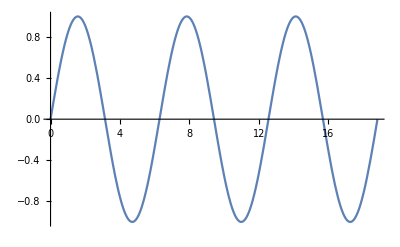

```mathematica
Plot[Sin[x],{x,0,6Pi}]
```

```mathematica
D[SphericalBesselJ[1,r],r]/.r->2.0816
```

-5.64159×10^-6

```mathematica
E//N
```

2.71828

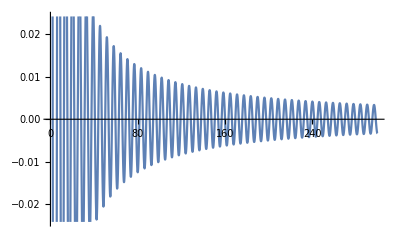

```mathematica
Plot[-SphericalBesselJ[1,r]/(2 r)+1/2 (SphericalBesselJ[0,r]-SphericalBesselJ[2,r]),{r,0.1,300}]
```

```mathematica
(C[1] LegendreP[1/2 (-1+2 √(1+w^2)),7/2,Cos[χ]])/((-1+Cos[χ]^2)^(1/4))(C[1] LegendreP[1/2 (-1+2 √(1+w^2)),7/2,Cos[χ]])/((-1+Cos[χ]^2)^(1/4))//Integrate[#,χ]&
```

C[1]^2 ∫(LegendreP[1/2 (-1+2 √(1+w^2)),7/2,Cos[χ]]^2)/(√(-1+Cos[χ]^2))ⅆχ

```mathematica
l=5;
m1=3;
EOMOpS3[Cos[(Sqrt[l(l+2)] t)/a+m1 ϕ]LegendreP[l,m1,Cos[θ]] LegendreP[(2l+1)/2,(2l+1)/2,Cos[χ]]/((1-Cos[χ]^2)^(1/4))]//FullSimplify
```

0

```mathematica
LegendreP[3/2 ,3/2,Cos[χ]]
```

-((1+Cos[χ])^(3/4) (3 Cos[χ]-2 Cos[χ]^3))/(2 √π (1+1/2 (-1+Cos[χ]))^(3/2) (1-Cos[χ])^(3/4))

```mathematica
LegendreP[1/2 (-1+2 √(1+3)),3/2,Cos[χ]]/.χ->2//N
```

1.01618

```mathematica
Integrate[LegendreP[(2l+1)/2,(2l+1)/2,Cos[χ]]/((1-Cos[χ]^2)^(1/4))Sin[χ]^2,χ]
```

(15 (280 Csc[χ]+84 Csc[χ]^3-320 Sin[χ]-128 Sin[χ]^3-(512 Sin[χ]^5)/5-(1024 Sin[χ]^7)/7))/(2 √(2 π))

```mathematica
(15 (280 Csc[χ]+84 Csc[χ]^3-320 Sin[χ]-128 Sin[χ]^3-(512 Sin[χ]^5)/5-(1024 Sin[χ]^7)/7))/(2 √(2 π))/.χ->π/2
```

-(8733 √(2/π))/7

```mathematica
Assuming[Sin[χ]>0,Integrate[(3 C[1] (1+Cos[χ])^(7/4) (35 Cos[χ]-70 Cos[χ]^3+56 Cos[χ]^5-16 Cos[χ]^7))/(8 √π (1+1/2 (-1+Cos[χ]))^(7/2) (1-Cos[χ])^(7/4) (-1+Cos[χ]^2)^(1/4))(3 C[1] (1+Cos[χ])^(7/4) (35 Cos[χ]-70 Cos[χ]^3+56 Cos[χ]^5-16 Cos[χ]^7))/(8 √π (1+1/2 (-1+Cos[χ]))^(7/2) (1-Cos[χ])^(7/4) (-1+Cos[χ]^2)^(1/4))Sin[χ]^2,χ]//Simplify]
```

-1/(2 π)3 ⅈ C[1]^2 (840 χ-4 Cot[χ] (278+55 Csc[χ]^2+15 Csc[χ]^4)+672 Sin[2 χ]-168 Sin[4 χ]+32 Sin[6 χ]-3 Sin[8 χ])

```mathematica
ClearAll[YS2Sol,YS2SolSim]
YS2Sol[l_,m_,id_]:=  a Sqrt[Sqrt[l(l+1)]] Sqrt[2l+1]/Sqrt[l(l+1)] Sqrt[((l-m)!!)/((l+m)!!)] 1/Sqrt[Product[l-mm,{mm,-m+1,m-1,2}]](β[c,l,m,id] Cos[Sqrt[l(l+1)]/a t+m ϕ](Assuming[Sin[θ]>0,LegendreP[l,m,Cos[θ]]//Simplify])+ β[s,l,m,id] Sin[Sqrt[l(l+1)]/a t+m ϕ](Assuming[Sin[θ]>0,LegendreP[l,m,Cos[θ]]//Simplify]))
YS2SolSim[l_,m_,id_]:=  a c[l,m](β[c,l,m,id] Cos[Sqrt[l(l+1)]/a t+m ϕ](Assuming[Sin[θ]>0,LegendreP[l,m,Cos[θ]]//Simplify])+ β[s,l,m,id] Sin[Sqrt[l(l+1)]/a t+m ϕ](Assuming[Sin[θ]>0,LegendreP[l,m,Cos[θ]]//Simplify]))
```

```mathematica
LegendreP[2,2,Cos[θ]]//FullSimplify
```

3 Sin[θ]^2

```mathematica
LegendreP[2,1,Cos[θ]]//FullSimplify
```

-3 Cos[θ] √(Sin[θ]^2)

```mathematica
(Assuming[Sin[θ]>0,LegendreP[7,3,Cos[θ]]//Simplify])
```

-315/8 (3-66 Cos[θ]^2+143 Cos[θ]^4) Sin[θ]^3

```mathematica
10395//FactorInteger
```

{{3,3},{5,1},{7,1},{11,1}}

```mathematica
(*Table[
YSol[id_]:=YS2Sol[kk,12,id];
actionZ0=(2D[v[μ[1]]t,t]D[YSol[μ[2]],t]) a^2 Sin[θ];
Assuming[Sin[θ]>0,actionZ0=actionZ0//Simplify//Expand;]
actionZ0a=actionZ0/.repid2dot//TrigToExp//Expand;
actionZ2=actionZ0 Product[YSol[μ[jj]],{jj,3,3}]/.repid2dot//TrigToExp//Expand;
actionZ2a=(2π)/(4 π a^2)*actionZ2/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
actionZ2b=actionZ2a/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand;
((actionZ2b/.dot[k,β[s,f__]]:>0/.dot[f__]:>1/.a->1)==1//Solve)[[2]]/.Rule[f1_,f2_]:>Rule[f1,f2^-2],{kk,12,16}]*)
```

{{c[12,12]→1},{c[13,12]→1},{c[14,12]→1},{c[15,12]→1},{c[16,12]→1}}

```mathematica
funt=fun[t](SphericalHarmonicY[1,1,θ,ϕ]);
funtest=EOMOpS2[funt]//Simplify;
```

```mathematica
funtest
```

(ⅇ^(ⅈ ϕ) √(3/(2 π)) Sin[θ]^2 (2 fun[t]+a^2 fun''[t]))/(2 a)

```mathematica
funSol=DSolve[funtest==0,fun[t],t]//Simplify
```

{{fun[t]→C[1] Cos[(√2 t)/a]+C[2] Sin[(√2 t)/a]}}

```mathematica
funtSol=funt/.funSol[[1]]//Simplify
```

-1/2 ⅇ^(-ⅈ ϕ) (1+ⅇ^(2 ⅈ ϕ)) √(3/(2 π)) (C[1] Cos[(√2 t)/R]+C[2] Sin[(√2 t)/R]) Sin[θ]

### Check dY dY G(Z) terms

```mathematica
actionY0=(D[YSol[μ[1]],t]D[YSol[μ[2]],t]-1/a^2 D[YSol[μ[1]],θ]D[YSol[μ[2]],θ]-1/(a^2 Sin[θ]^2)D[YSol[μ[1]],ϕ]D[YSol[μ[2]],ϕ]) a Sin[θ]//Simplify;
```

```mathematica
ta=actionY0 /.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//Expand;
Integrate[%//Expand,{ϕ,0,2π}]
Integrate[%,{θ,0,π}]
```

1/4 a π (dot[ε,β[c,1,1]]^2+dot[ε,β[s,1,1]]^2) (Sin[θ]-3 Sin[3 θ])

0

```mathematica
actionY8=actionY0  Product[YSol[μ[jj]],{jj,3,4}]/.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//TrigToExp//Expand;
2π*actionY8/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Simplify
```

8/15 a^3 π (dot[k,β[s,1,1]] dot[ε,β[c,1,1]]-dot[k,β[c,1,1]] dot[ε,β[s,1,1]])^2

```mathematica
Integrate[actionY6[[332]],{ϕ,0,2π}]
Integrate[%,{θ,0,π}]
```

(1575 ⅈ ⅇ^(3 ⅈ θ) π dot[k,β[c,1,1]]^2 dot[k,β[s,1,1]]^4 dot[ε,β[c,1,1]]^2)/(8192 a)

-(525 π dot[k,β[c,1,1]]^2 dot[k,β[s,1,1]]^4 dot[ε,β[c,1,1]]^2)/(4096 a)

```mathematica
Integrate[actionY6,{ϕ,0,2π}];
Integrate[%,{θ,0,π}]
```

1/(21 a)8 π (dot[k,β[c,1,1]]^2+dot[k,β[s,1,1]]^2)^2 (dot[k,β[s,1,1]] dot[ε,β[c,1,1]]-dot[k,β[c,1,1]] dot[ε,β[s,1,1]])^2

### Check dX dX G(Z) terms

```mathematica
ampEven=Integrate[a Sin[θ]( YSol[ν[1]])( YSol[ν[2]])( YSol[ν[3]])( YSol[ν[4]])//Expand,{ϕ,0,2π}]//Expand;
ampEven=ampEven/.β[f__,ν[i_]]:>dot[β[f],k];
```

```mathematica
ampEven2=ampEven//Expand//Integrate[#,{θ,0,π}]&
```

```mathematica
ampOdd=Integrate[r D[Ysol[ν[1]],t]Ysol[ν[2]]Ysol[ν[3]]Ysol[ν[4]]/.m->1//Expand,{θ,0,2π}]//Expand;
ampOdd/.β[f__,ν[1]]:>dot[β[f],ε]/.β[f__,ν[i_]]:>dot[β[f],k]/;i>1//Simplify
```

1/(4 a)3 π r^5 (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2) (-dot[k,β[s,1]] dot[ε,β[c,1]]+dot[k,β[c,1]] dot[ε,β[s,1]])

```mathematica
ampEven=Integrate[r Ysol[ν[1]]Ysol[ν[2]]Ysol[ν[3]]Ysol[ν[4]]/.m->1//Expand,{θ,0,2π}]//Expand;
ampEven/.β[f__,ν[i_]]:>dot[β[f],k]//Simplify
```

3/4 π r^5 (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2)^2

## Amp 3

```mathematica
repid2dot={v[μ[1]]->dot[v,ϵ],v[μ[2]]->dot[v,ϵ],β[f__,μ[1]]:>dot[β[f],ϵ],β[f__,μ[2]]:>dot[β[f],ϵ],β[f__,μ[i_]]:>dot[β[f],k]/;i>1};
ClearAll[YSol]
YSol[id_]:=YS2Sol[1,1,id]
```

```mathematica
actionZ0=(D[v[μ[1]]t,t]D[v[μ[2]]t,t]+2D[v[μ[1]]t,t]D[YSol[μ[2]],t]+D[YSol[μ[1]],t]D[YSol[μ[2]],t]-1/a^2 D[YSol[μ[1]],θ]D[YSol[μ[2]],θ]-1/(a^2 Sin[θ]^2)D[YSol[μ[1]],ϕ]D[YSol[μ[2]],ϕ]) a^2 Sin[θ];
Assuming[Sin[θ]>0,actionZ0=actionZ0//Simplify//Expand;]
```

```mathematica
actionZ0a=actionZ0/.repid2dot//TrigToExp//Expand;
```

```mathematica
(2π)/(4 π a^2)*actionZ0a/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Simplify
```

dot[v,ϵ]^2

```mathematica
actionZ1=actionZ0 Product[YSol[μ[jj]],{jj,3,3}]/.repid2dot//TrigToExp//Expand;
(2π)/(4 π a^2)*actionZ2/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand
```

-a dot[k,β[s,1,1]] dot[v,ϵ] dot[ϵ,β[c,1,1]]+a dot[k,β[c,1,1]] dot[v,ϵ] dot[ϵ,β[s,1,1]]

```mathematica
ClearAll[Y2a]
Y2a[fg_]:=Module[{res},res=(2π)/(4 π a^2)fg/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
res=res/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand;
res=res/.v->t v[0]//Collect[#,t,Simplify]&;
res=res/.dot[k,β[c,ids__]]^2+dot[k,β[s,ids__]]^2:>(-dot[k,a]^2)/a^2/.(dot[k,β[s,ids__]] dot[ϵ,β[c,ids__]]-dot[k,β[c,ids__]] dot[ϵ,β[s,ids__]])->dot[k,S[0],ϵ]/.dot[k,S[0],ϵ]^2->(-dot[k,a]^2)/a^2 dot[ϵ,v[0]]^2//Simplify
]
```

```mathematica
actionZ2=actionZ0 Product[-I YSol[μ[jj]],{jj,3,4}]/.repid2dot//TrigToExp//Expand;
(2π)/(4 π a^2)*actionZ2/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand;
%/.v->t v[0]//Collect[#,t,Simplify]&
%/.dot[k,β[c,ids__]]^2+dot[k,β[s,ids__]]^2:>(-dot[k,a]^2)/a^2/.(dot[k,β[s,ids__]] dot[ϵ,β[c,ids__]]-dot[k,β[c,ids__]] dot[ϵ,β[s,ids__]])->dot[k,S[0],ϵ]/.dot[k,S[0],ϵ]^2->(-dot[k,a]^2)/a^2 dot[ϵ,v[0]]^2//Simplify
```

-(a^2 t^2 (dot[k,β[c,1,1]]^2+dot[k,β[s,1,1]]^2) dot[ϵ,v[0]]^2)/(2 √2)-3/20 a^2 (dot[k,β[s,1,1]] dot[ϵ,β[c,1,1]]-dot[k,β[c,1,1]] dot[ϵ,β[s,1,1]])^2

1/20 (3+5 √2 t^2) dot[a,k]^2 dot[ϵ,v[0]]^2

```mathematica
Monitor[res=Table[actionZ2=actionZ0 Product[-I YSol[μ[jj]],{jj,3,kk}]/.repid2dot//TrigToExp//Expand;
Y2a[actionZ2],{kk,4,20,2}];,kk]
```

```mathematica
Coefficient[res,t^2]
```

{(dot[a,k]^2 dot[ϵ,v[0]]^2)/(2 √2),9/40 dot[a,k]^4 dot[ϵ,v[0]]^2,(27 dot[a,k]^6 dot[ϵ,v[0]]^2)/(112 √2),9/64 dot[a,k]^8 dot[ϵ,v[0]]^2,(243 dot[a,k]^10 dot[ϵ,v[0]]^2)/(1408 √2),(729 dot[a,k]^12 dot[ϵ,v[0]]^2)/6656,(729 dot[a,k]^14 dot[ϵ,v[0]]^2)/(5120 √2),(6561 dot[a,k]^16 dot[ϵ,v[0]]^2)/69632,(19683 dot[a,k]^18 dot[ϵ,v[0]]^2)/(155648 √2)}

```mathematica
res2=Table[res[[jj/2-1]]((2 √2)/3)^(jj/2-1)(jj-1),{jj,4,20,2}]
```

{1/20 (3+5 √2 t^2) dot[a,k]^2 dot[ϵ,v[0]]^2,9/280 (3 √2+7 t^2) dot[a,k]^4 dot[ϵ,v[0]]^2,27/224 (1+√2 t^2) dot[a,k]^6 dot[ϵ,v[0]]^2,9/704 (6 √2+11 t^2) dot[a,k]^8 dot[ϵ,v[0]]^2,(243 (15+13 √2 t^2) dot[a,k]^10 dot[ϵ,v[0]]^2)/36608,(729 (3 √2+5 t^2) dot[a,k]^12 dot[ϵ,v[0]]^2)/33280,(729 (21+17 √2 t^2) dot[a,k]^14 dot[ϵ,v[0]]^2)/174080,(6561 (12 √2+19 t^2) dot[a,k]^16 dot[ϵ,v[0]]^2)/1323008,(19683 (9+7 √2 t^2) dot[a,k]^18 dot[ϵ,v[0]]^2)/2179072}

```mathematica
Sum[1/(((2 √2)/3)^(jj/2-1)(jj-1))dot[a,k]^(jj-2)/((jj-2)!),{jj,4,∞,2}]//Simplify
```

-1+(2^(3/4) Sinh[(√3 dot[a,k])/2^(3/4)])/(√3 dot[a,k])

```mathematica
Series[%/.dot[a,k]->t dot[a,k],{t,0,6}]
```

(dot[a,k]^2 t^2)/(4 √2)+3/80 dot[a,k]^4 t^4+(9 dot[a,k]^6 t^6)/(896 √2)+O[t]^7

```mathematica
Table[1/(((2 √2)/3)^(jj/2-1)(jj-1))dot[a,k]^(jj/2)/((jj/2)!),{jj,4,20,2}]
```

{1/(2 √2),9/40,27/(112 √2),9/64,243/(1408 √2),729/6656,729/(5120 √2),6561/69632,19683/(155648 √2)}

```mathematica
res2=Table[res[[jj/2-1]]((2 √2)/3)^(jj/2-1)(jj-1),{jj,4,20,2}]
```

{((3+5 √2 t^2) dot[a,k]^2 dot[ϵ,v[0]]^2)/(5 √2),1/7 (3 √2+7 t^2) dot[a,k]^4 dot[ϵ,v[0]]^2,((1+√2 t^2) dot[a,k]^6 dot[ϵ,v[0]]^2)/(√2),1/11 (6 √2+11 t^2) dot[a,k]^8 dot[ϵ,v[0]]^2,((15+13 √2 t^2) dot[a,k]^10 dot[ϵ,v[0]]^2)/(13 √2),1/5 (3 √2+5 t^2) dot[a,k]^12 dot[ϵ,v[0]]^2,((21+17 √2 t^2) dot[a,k]^14 dot[ϵ,v[0]]^2)/(17 √2),1/19 (12 √2+19 t^2) dot[a,k]^16 dot[ϵ,v[0]]^2,((9+7 √2 t^2) dot[a,k]^18 dot[ϵ,v[0]]^2)/(7 √2)}

```mathematica
Coefficient[res2,t^2]/.t->0/.dot[f__]:>1
```

{1,1,1,1,1,1,1,1,1}

```mathematica
Table[1/(3^(ii/2-2)(ii-1)),{ii,4,20,2}]
```

{1/3,1/15,1/63,1/243,1/891,1/3159,1/10935,1/37179,1/124659}

```mathematica
168//FactorInteger
297//FactorInteger
```

{{2,3},{3,1},{7,1}}

{{3,3},{11,1}}

## Amp 3 Y22

```mathematica
repid2dot={v[μ[1]]->dot[v,ϵ],v[μ[2]]->dot[v,ϵ],β[f__,μ[1]]:>dot[β[f],ϵ],β[f__,μ[2]]:>dot[β[f],ϵ],β[f__,μ[i_]]:>dot[β[f],k]/;i>1};
ClearAll[YSol]
YSol[id_]:=YS2SolSim[2,2,id]
```

```mathematica
actionZ0=(D[v[μ[1]]t,t]D[v[μ[2]]t,t]) a^2 Sin[θ]
Assuming[Sin[θ]>0,actionZ0=actionZ0//Simplify//Expand;]
```

a^2 Sin[θ] v[μ[1]] v[μ[2]]

```mathematica
actionZ0a=actionZ0/.repid2dot//TrigToExp//Expand;
```

### test

```mathematica
(2π)/(4 π a^2)*actionZ0a/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Simplify
```

dot[v,ϵ]^2

```mathematica
actionZ1=actionZ0 Product[YSol[μ[jj]],{jj,3,6}]/.repid2dot//TrigToExp//Expand;
ta=(2π)/(4 π a^2)*actionZ1/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand//Simplify
```

432/35 a^4 c[2,2]^4 (dot[k,β[c,2,2]]^2+dot[k,β[s,2,2]]^2)^2 dot[v,ϵ]^2

```mathematica
1/(4 π a^2)actionZ1//Integrate[#,{ϕ,0,2π}]&
%//Integrate[#,{θ,0,π}]&
```

243/16 a^4 c[2,2]^4 (dot[k,β[c,2,2]]^2+dot[k,β[s,2,2]]^2)^2 dot[v,ϵ]^2 Sin[θ]^9

432/35 a^4 c[2,2]^4 (dot[k,β[c,2,2]]^2+dot[k,β[s,2,2]]^2)^2 dot[v,ϵ]^2

### continue

```mathematica
ClearAll[Y2a]
Y2a[fg_]:=Module[{res},res=(2π)/(4 π a^2)fg/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
res=res/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand;
res=res/.v->t v[0]//Collect[#,t,Simplify]&;
res=res/.dot[k,β[c,ids__]]^2+dot[k,β[s,ids__]]^2:>(-dot[k,a]^2)/a^2/.(dot[k,β[s,ids__]] dot[ϵ,β[c,ids__]]-dot[k,β[c,ids__]] dot[ϵ,β[s,ids__]])->dot[k,S[0],ϵ]/.dot[k,S[0],ϵ]^2->(-dot[k,a]^2)/a^2 dot[ϵ,v[0]]^2//Simplify
]
```

```mathematica
Monitor[res=Table[actionZ2=actionZ0 Product[-I YSol[μ[jj]],{jj,3,kk}]/.repid2dot//TrigToExp//Expand;
Y2a[actionZ2],{kk,4,20,2}];,kk]
```

```mathematica
432//FactorInteger
```

{{2,4},{3,3}}

```mathematica
Coefficient[res,t^2]
```

{12/5 c[2,2]^2 dot[a,k]^2 dot[ϵ,v[0]]^2,432/35 c[2,2]^4 dot[a,k]^4 dot[ϵ,v[0]]^2,(77760 c[2,2]^6 dot[a,k]^6 dot[ϵ,v[0]]^2)/1001,(1306368 c[2,2]^8 dot[a,k]^8 dot[ϵ,v[0]]^2)/2431,(181398528 c[2,2]^10 dot[a,k]^10 dot[ϵ,v[0]]^2)/46189,(71833817088 c[2,2]^12 dot[a,k]^12 dot[ϵ,v[0]]^2)/2414425,(1245119496192 c[2,2]^14 dot[a,k]^14 dot[ϵ,v[0]]^2)/5386025,(12224809598976 c[2,2]^16 dot[a,k]^16 dot[ϵ,v[0]]^2)/6678671,(7481583474573312 c[2,2]^18 dot[a,k]^18 dot[ϵ,v[0]]^2)/508757585}

```mathematica
res2=Table[res[[jj/2-1]]((2(jj-2)+1)(2(jj-2)-1)!!)/((3)^(jj-2) 2^(jj-2) (jj-2-1)!! (jj-2-1)!!),{jj,4,20,2}]
```

{t^2 c[2,2]^2 dot[a,k]^2 dot[ϵ,v[0]]^2,t^2 c[2,2]^4 dot[a,k]^4 dot[ϵ,v[0]]^2,t^2 c[2,2]^6 dot[a,k]^6 dot[ϵ,v[0]]^2,t^2 c[2,2]^8 dot[a,k]^8 dot[ϵ,v[0]]^2,t^2 c[2,2]^10 dot[a,k]^10 dot[ϵ,v[0]]^2,t^2 c[2,2]^12 dot[a,k]^12 dot[ϵ,v[0]]^2,t^2 c[2,2]^14 dot[a,k]^14 dot[ϵ,v[0]]^2,t^2 c[2,2]^16 dot[a,k]^16 dot[ϵ,v[0]]^2,t^2 c[2,2]^18 dot[a,k]^18 dot[ϵ,v[0]]^2}

```mathematica
((2(jj-2)+1)(2(jj-2)-1)!!)/((3)^(jj-2) 2^(jj-2) (jj-2-1)!! (jj-2-1)!!)//Simplify
```

(6^(2-jj) (-3+2 jj) (-5+2 jj)!!)/((-3+jj)!!)^2

```mathematica
Sum[((3)^(jj-2) 2^(jj-2) (jj-2-1)!! (jj-2-1)!!)/((2(jj-2)+1)(2(jj-2)-1)!!)dot[a,k]^(jj-2)/((jj-2)!),{jj,2,∞,2}]
```

HypergeometricPFQ[{1/2},{3/4,5/4},9/4 dot[a,k]^2]

```mathematica
HypergeometricPFQ[{1/2},{3/4,5/4},1.2+0.001I]//N
HypergeometricPFQ[{1},{1},x]//Simplify
```

1.80378+0.000821858 ⅈ

ⅇ^x

```mathematica
Exp[1234]//N
```

8.30597593736×10^535

```mathematica
Series[%/.dot[a,k]->t dot[a,k],{t,0,6}]
```

(dot[a,k]^2 t^2)/(4 √2)+3/80 dot[a,k]^4 t^4+(9 dot[a,k]^6 t^6)/(896 √2)+O[t]^7

```mathematica
Table[1/(((2 √2)/3)^(jj/2-1)(jj-1))dot[a,k]^(jj/2)/((jj/2)!),{jj,4,20,2}]
```

{1/(2 √2),9/40,27/(112 √2),9/64,243/(1408 √2),729/6656,729/(5120 √2),6561/69632,19683/(155648 √2)}

```mathematica
res2=Table[res[[jj/2-1]]((2 √2)/3)^(jj/2-1)(jj-1),{jj,4,20,2}]
```

{((3+5 √2 t^2) dot[a,k]^2 dot[ϵ,v[0]]^2)/(5 √2),1/7 (3 √2+7 t^2) dot[a,k]^4 dot[ϵ,v[0]]^2,((1+√2 t^2) dot[a,k]^6 dot[ϵ,v[0]]^2)/(√2),1/11 (6 √2+11 t^2) dot[a,k]^8 dot[ϵ,v[0]]^2,((15+13 √2 t^2) dot[a,k]^10 dot[ϵ,v[0]]^2)/(13 √2),1/5 (3 √2+5 t^2) dot[a,k]^12 dot[ϵ,v[0]]^2,((21+17 √2 t^2) dot[a,k]^14 dot[ϵ,v[0]]^2)/(17 √2),1/19 (12 √2+19 t^2) dot[a,k]^16 dot[ϵ,v[0]]^2,((9+7 √2 t^2) dot[a,k]^18 dot[ϵ,v[0]]^2)/(7 √2)}

```mathematica
Coefficient[res2,t^2]/.t->0/.dot[f__]:>1
```

{1,1,1,1,1,1,1,1,1}

```mathematica
Table[1/(3^(ii/2-2)(ii-1)),{ii,4,20,2}]
```

{1/3,1/15,1/63,1/243,1/891,1/3159,1/10935,1/37179,1/124659}

```mathematica
168//FactorInteger
297//FactorInteger
```

{{2,3},{3,1},{7,1}}

{{3,3},{11,1}}

## Amp 3 Y31

```mathematica
repid2dot={v[μ[1]]->dot[v,ϵ],v[μ[2]]->dot[v,ϵ],β[f__,μ[1]]:>dot[β[f],ϵ],β[f__,μ[2]]:>dot[β[f],ϵ],β[f__,μ[i_]]:>dot[β[f],k]/;i>1};
ClearAll[YSol]
YSol[id_]:=YS2SolSim[3,3,id]
```

```mathematica
actionZ0=(D[v[μ[1]]t,t]D[v[μ[2]]t,t]) a^2 Sin[θ]
Assuming[Sin[θ]>0,actionZ0=actionZ0//Simplify//Expand;]
```

a^2 Sin[θ] v[μ[1]] v[μ[2]]

```mathematica
actionZ0a=actionZ0/.repid2dot//TrigToExp//Expand;
```

### test

```mathematica
(2π)/(4 π a^2)*actionZ0a/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Simplify
```

dot[v,ϵ]^2

```mathematica
actionZ1=actionZ0 Product[YSol[μ[jj]],{jj,3,6}]/.repid2dot//TrigToExp//Expand;
ta=(2π)/(4 π a^2)*actionZ1/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand//Simplify
```

432/35 a^4 c[2,2]^4 (dot[k,β[c,2,2]]^2+dot[k,β[s,2,2]]^2)^2 dot[v,ϵ]^2

```mathematica
1/(4 π a^2)actionZ1//Integrate[#,{ϕ,0,2π}]&
%//Integrate[#,{θ,0,π}]&
```

243/16 a^4 c[2,2]^4 (dot[k,β[c,2,2]]^2+dot[k,β[s,2,2]]^2)^2 dot[v,ϵ]^2 Sin[θ]^9

432/35 a^4 c[2,2]^4 (dot[k,β[c,2,2]]^2+dot[k,β[s,2,2]]^2)^2 dot[v,ϵ]^2

### continue

```mathematica
ClearAll[Y2a]
Y2a[fg_]:=Module[{res},res=(2π)/(4 π a^2)fg/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
res=res/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand;
res=res/.v->t v[0]//Collect[#,t,Simplify]&;
res=res/.dot[k,β[c,ids__]]^2+dot[k,β[s,ids__]]^2:>(-dot[k,a]^2)/a^2/.(dot[k,β[s,ids__]] dot[ϵ,β[c,ids__]]-dot[k,β[c,ids__]] dot[ϵ,β[s,ids__]])->dot[k,S[0],ϵ]/.dot[k,S[0],ϵ]^2->(-dot[k,a]^2)/a^2 dot[ϵ,v[0]]^2//Simplify
]
```

```mathematica
lm=1
Assuming[Element[n,Integers]&&n>0,ta=(LegendreP[lm,lm,Cos[θ]])^(2n)Sin[θ]//Integrate[#,{θ,0,π}]&//FullSimplify;]
Assuming[Element[n,Integers]&&n>0,tb=(Cos[lm ϕ] )^(2n)//Integrate[#,{ϕ,0,2π}]&;]
AmpRes=Sum[1/(4 π)ta*tb/((2n)!) x^(2n),{n,0,∞}]
```

1

Sinh[x]/x

```mathematica
(LegendreP[1,1,Cos[θ]])^(2n)Sin[θ]//Integrate[#,{θ,0,π}]&//FullSimplify
```

ConditionalExpression[((-1)^(2 n) √π Gamma[1+n])/Gamma[3/2+n], Re[n]>-1]

```mathematica
(Cos[ϕ] )^(2n)//Integrate[#,{ϕ,0,2π}]&
```

ConditionalExpression[((1+(-1)^(2 n))^2 √π Gamma[1/2+n])/(2 Gamma[1+n]), Re[n]>-1/2]

```mathematica
Assuming[Element[n,Integers]&&n>0,((1+(-1)^(2 n))^2 √π Gamma[1/2+n])/(2 Gamma[1+n])(9^n √π Gamma[1+2 n])/Gamma[3/2+2 n]//FullSimplify]
```

(2 9^n π (2 n)! Gamma[1/2+n])/(n! Gamma[3/2+2 n])

```mathematica
x^(2n)(1-x^2)^(-1/2)//Integrate[#,{x,0,1}]&
```

ConditionalExpression[(√π Gamma[1/2+n])/(2 Gamma[1+n]), Re[n]>-1/2]

```mathematica
ta//FullSimplify
```

(√π n!)/Gamma[3/2+n]

```mathematica
tb//FullSimplify
```

(2 √π Gamma[1/2+n])/Gamma[1+n]

```mathematica
Gamma[1/2+n]/Gamma[3/2+n]//FullSimplify
```

2/(1+2 n)

```mathematica
Integrate[x^(2n),{x,0,1}]
```

ConditionalExpression[1/(1+2 n), Re[n]>-1/2]

```mathematica
Gamma[1+n]/n!//FullSimplify
```

1

```mathematica
ta*tb//FullSimplify
```

(4 π)/(1+2 n)

```mathematica
tb
```

(2 √π Gamma[1/2+n])/Gamma[1+n]

```mathematica
ClearAll[YSolt]
YSolt[id_]:=YS2SolSim[lm,lm,id]
Monitor[res=Table[actionZ2=actionZ0 Product[-I YSolt[μ[jj]],{jj,3,kk}]/.repid2dot//TrigToExp//Expand;
Y2a[actionZ2],{kk,4,12,2}];,kk]
```

```mathematica
res0=Coefficient[res/.dot[f__]:>1/.c[d__]:>1,t^2];
res2=Table[res0[[jj/2-1]] 1/((jj-2)!),{jj,4,12,2}]
```

{6/5,18/35,108/1001,162/12155,8748/8083075}

```mathematica
Series[AmpRes,{x,0,8}]
```

1+(6 x^2)/5+(18 x^4)/35+(108 x^6)/1001+(162 x^8)/12155+O[x]^9

```mathematica
Series[Sinh[x]/x,{x,0,8}]
```

1+x^2/6+x^4/120+x^6/5040+x^8/362880+O[x]^9

```mathematica
((2(jj-2)+1)(2(jj-2)-1)!!)/((3)^(jj-2) 2^(jj-2) (jj-2-1)!! (jj-2-1)!!)//Simplify
```

(6^(2-jj) (-3+2 jj) (-5+2 jj)!!)/((-3+jj)!!)^2

```mathematica
Sum[((3)^(jj-2) 2^(jj-2) (jj-2-1)!! (jj-2-1)!!)/((2(jj-2)+1)(2(jj-2)-1)!!)dot[a,k]^(jj-2)/((jj-2)!),{jj,2,∞,2}]
```

HypergeometricPFQ[{1/2},{3/4,5/4},9/4 dot[a,k]^2]

```mathematica
HypergeometricPFQ[{1/2},{3/4,5/4},1.2+0.001I]//N
HypergeometricPFQ[{1},{1},x]//Simplify
```

1.80378+0.000821858 ⅈ

ⅇ^x

```mathematica
Exp[1234]//N
```

8.30597593736×10^535

```mathematica
Series[%/.dot[a,k]->t dot[a,k],{t,0,6}]
```

(dot[a,k]^2 t^2)/(4 √2)+3/80 dot[a,k]^4 t^4+(9 dot[a,k]^6 t^6)/(896 √2)+O[t]^7

```mathematica
Table[1/(((2 √2)/3)^(jj/2-1)(jj-1))dot[a,k]^(jj/2)/((jj/2)!),{jj,4,20,2}]
```

{1/(2 √2),9/40,27/(112 √2),9/64,243/(1408 √2),729/6656,729/(5120 √2),6561/69632,19683/(155648 √2)}

```mathematica
res2=Table[res[[jj/2-1]]((2 √2)/3)^(jj/2-1)(jj-1),{jj,4,20,2}]
```

{((3+5 √2 t^2) dot[a,k]^2 dot[ϵ,v[0]]^2)/(5 √2),1/7 (3 √2+7 t^2) dot[a,k]^4 dot[ϵ,v[0]]^2,((1+√2 t^2) dot[a,k]^6 dot[ϵ,v[0]]^2)/(√2),1/11 (6 √2+11 t^2) dot[a,k]^8 dot[ϵ,v[0]]^2,((15+13 √2 t^2) dot[a,k]^10 dot[ϵ,v[0]]^2)/(13 √2),1/5 (3 √2+5 t^2) dot[a,k]^12 dot[ϵ,v[0]]^2,((21+17 √2 t^2) dot[a,k]^14 dot[ϵ,v[0]]^2)/(17 √2),1/19 (12 √2+19 t^2) dot[a,k]^16 dot[ϵ,v[0]]^2,((9+7 √2 t^2) dot[a,k]^18 dot[ϵ,v[0]]^2)/(7 √2)}

```mathematica
Coefficient[res2,t^2]/.t->0/.dot[f__]:>1
```

{1,1,1,1,1,1,1,1,1}

```mathematica
Table[1/(3^(ii/2-2)(ii-1)),{ii,4,20,2}]
```

{1/3,1/15,1/63,1/243,1/891,1/3159,1/10935,1/37179,1/124659}

```mathematica
168//FactorInteger
297//FactorInteger
```

{{2,3},{3,1},{7,1}}

{{3,3},{11,1}}

# S2*S1*R model

## EOM for S2*S1*R

```mathematica
ActionS2S1= (D[Y[t,r,θ,ϕ],t]D[Y[t,r,θ,ϕ],t]-D[Y[t,r,θ,ϕ],r]D[Y[t,r,θ,ϕ],r]-1/a^2 D[Y[t,r,θ,ϕ],θ]D[Y[t,r,θ,ϕ],θ]-1/(a^2 Sin[θ]^2)D[Y[t,r,θ,ϕ],ϕ]D[Y[t,r,θ,ϕ],ϕ]) a^2 Sin[θ];
eom=(ActionS2S1//Expand)/.Times[f__,(Derivative[pw__][Y][t,r,θ,ϕ])^2]:>D[f Derivative[pw][Y][t,r,θ,ϕ],{pw}.{t,r,θ,ϕ}];
ClearAll[EOMOpS2S1]
EOMOpS2S1[fun_]:=eom/.Derivative[pws__][Y][vars__]:>D[fun,Sequence@@({{vars},{pws}}//Transpose)]
```

```mathematica
eom
```

-ⅇ^(-r/(2 a)) Csc[θ] Y^(0,0,0,2)[t,r,θ,ϕ]-ⅇ^(-r/(2 a)) Cos[θ] Y^(0,0,1,0)[t,r,θ,ϕ]-ⅇ^(-r/(2 a)) Sin[θ] Y^(0,0,2,0)[t,r,θ,ϕ]+a ⅇ^(-r/a) Sin[θ] Y^(0,1,0,0)[t,r,θ,ϕ]-a^2 ⅇ^(-r/a) Sin[θ] Y^(0,2,0,0)[t,r,θ,ϕ]+a^2 ⅇ^(-r/a) Sin[θ] Y^(2,0,0,0)[t,r,θ,ϕ]

```mathematica
eomhold=eom/(a^2 Sin[θ])/.Derivative[pw__][Y][vars__]:>dD[ Z,({pw}.{vars}/.a_ b_:>{b,a}/;NumberQ[a])]/.dD[Z,{f1_,od_}]:>Subsuperscript["∂",f1,od]/.dD[Z,f1_]:>Subscript["∂",f1]//Expand
```

-(Cot[θ] ∂_θ)/a^2-∂_r^2 +∂_t^2 -(∂_θ^2)/a^2-(Csc[θ]^2 ∂_ϕ^2)/a^2

```mathematica
l=1;
m1=1;
w=Sqrt[3];
Assuming[Sin[θ]>0,EOMOpS2S1[Cos[(w t)/a-m1 ϕ]LegendreP[l,m1,Cos[θ]]f2[r]]//FullSimplify]
```

Cos[(√3 t)/a-ϕ] Sin[θ]^2 (f2[r]+a^2 f2''[r])

```mathematica
DSolve[0==%,f2[r],r]
```

{{f2[r]→C[1] Cos[r/a]+C[2] Sin[r/a]}}

```mathematica
D[ⅇ^(r/a) C[1]+ⅇ^(-r/a) C[2],r]/.r->0
```

C[1]/a-C[2]/a

```mathematica
ClearAll[YS2S1Sol,YS2S1SolSim]
YS2S1Sol[w_,l_,m_,id_]:=  a Sqrt[2l+1]/Sqrt[l(l+1)] Sqrt[((l-m)!!)/((l+m)!!)] 1/Sqrt[Product[l-mm,{mm,-m+1,m-1,2}]](β[c,l,m,id] Cos[(w t)/a+m ϕ]+ β[s,l,m,id] Sin[(w t)/a+m ϕ])(Assuming[Sin[θ]>0,LegendreP[l,m,Cos[θ]]//Simplify])r/a
YS2S1SolSim[w_,l_,m_,id_]:=  a c[l,m](β[c,l,m,id] Cos[(w t)/a+m ϕ](Assuming[Sin[θ]>0,LegendreP[l,m,Cos[θ]]//Simplify])+ β[s,l,m,id] Sin[(w t)/a+m ϕ](Assuming[Sin[θ]>0,LegendreP[l,m,Cos[θ]]//Simplify]))r/a
```

### Check dY dY G(Z) terms

```mathematica
ClearAll[YSol]
YSol[id_]:=YS2S1SolSim[Sqrt[2],1,1,id]
```

```mathematica
actionY0=(D[YSol[μ[1]],t]D[YSol[μ[2]],t]-D[YSol[μ[1]],r]D[YSol[μ[2]],r]-1/a^2 D[YSol[μ[1]],θ]D[YSol[μ[2]],θ]-1/(a^2 Sin[θ]^2)D[YSol[μ[1]],ϕ]D[YSol[μ[2]],ϕ]) a^2 Sin[θ]//Simplify;
```

```mathematica
YSol[μ[1]]
```

r c[1,1] (-Cos[(√2 t)/a+ϕ] Sin[θ] β[c,1,1,μ[1]]-Sin[θ] Sin[(√2 t)/a+ϕ] β[s,1,1,μ[1]])

```mathematica
ta=actionY0 /.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//Expand;
Integrate[%//Expand,{ϕ,0,2π}]
Integrate[%,{θ,0,π}]
```

-1/2 π c[1,1]^2 (a^2+r^2-(a^2-3 r^2) Cos[2 θ]) (dot[ε,β[c,1,1]]^2+dot[ε,β[s,1,1]]^2) Sin[θ]

-4/3 a^2 π c[1,1]^2 (dot[ε,β[c,1,1]]^2+dot[ε,β[s,1,1]]^2)

```mathematica
Integrate[Cos[(2 √2 r)/a] ,{r,0,(a π)/(√2)}]
```

0

### Check dX dY G(Z) terms

```mathematica
ClearAll[YSolv]
YSolv[k_]:=YS2S1SolSim[Sqrt[2],1,1,ν[1]]/.β[cs_,f__]:>dot[β[cs],k]
```

```mathematica
measure=a^2 Sin[θ];
ampodd=measure*dot[v[0],ϵ[1]](D[YSolv[ϵ[1]],t])YSolv[k[1]]^(2j-1)/.Sin[f__]:>0/;Flatten[Cases[f,ϕ]//Union]=={ϕ}/.Cos[f_]:>Cos[f/.t->0]//PowerExpand;
```

```mathematica
Assuming[Element[j,Integers]&&j>=0,ampoddRes=ampodd//Integrate[#,{ϕ,0,2π}]&//Integrate[#,{θ,0,π}]&//Integrate[#,{r,0,a}]&]
```

(4 √2 a^(2+2 j) π c[1,1]^(2 j) dot[k[1],β[c]]^(-1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]])/(1+2 j)^2

```mathematica
Integrate[(1/(1+r)^(1/3))^j,{r,0,∞}]
```

ConditionalExpression[3/(-3+j), Re[j]>3]

```mathematica
Sum[ampoddRes 1/((2j-1)!),{j,1,∞}]
```

1/(c[1,1] dot[k[1],β[c]]^2)4 √2 a π dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] (Sinh[a c[1,1] dot[k[1],β[c]]]-SinhIntegral[a c[1,1] dot[k[1],β[c]]])

```mathematica
Assuming[Element[j,Integers]&&j>=0,ta=Integrate[Cos[ϕ]^(2 j),{ϕ,0,2π}];
tc=Integrate[ Cos[(√2 r)/a]^(2 j) ,{r,0,(a π)/(√2)}];
tb=Integrate[Sin[θ]^(1+2 j),{θ,0,π}];]
```

```mathematica
tc=Integrate[ Cos[r/a]^(2 j) ,{r,0, a π}]
```

ConditionalExpression[((1+(-1)^(2 j)) a √π Gamma[1/2+j])/(2 Gamma[1+j]), Re[j]>-1/2]

```mathematica
Integrate[(1)^(2j)(r)^(2j+1),{r,0,1}]
```

ConditionalExpression[1/(2+2 j), Re[j]>-1]

```mathematica
ta=Integrate[(Sqrt[1-x^2])^(2j-1),{x,0,1}]
```

ConditionalExpression[(√π Gamma[1/2+j])/(2 Gamma[1+j]), Re[j]>-1/2]

```mathematica
tb=Integrate[(Sqrt[1-x^(1/2)])^(2j-1),{x,0,1}]
```

ConditionalExpression[8/(3+8 j+4 j^2), Re[j]>-1/2]

```mathematica
Gamma[1+j]/Gamma[3/2+j]/.j->123//N
```

0.0898932

```mathematica
Assuming[Element[j,Integers]&&j>=0,ta*tb//FullSimplify]
```

π/(2+4 j)

```mathematica
Sum[ta*tb* tc x^(2j-1)/((2j-1)!),{j,1,∞}]//FullSimplify
```

(√2 a π^3 (BesselI[1,x] StruveL[0,x]-BesselI[0,x] StruveL[1,x]))/x

```mathematica
ampEven=Integrate[a Sin[θ]( YSol[ν[1]])( YSol[ν[2]])( YSol[ν[3]])( YSol[ν[4]])//Expand,{ϕ,0,2π}]//Expand;
ampEven=ampEven/.β[f__,ν[i_]]:>dot[β[f],k];
```

```mathematica
ampEven2=ampEven//Expand//Integrate[#,{θ,0,π}]&
```

```mathematica
ampOdd=Integrate[r D[Ysol[ν[1]],t]Ysol[ν[2]]Ysol[ν[3]]Ysol[ν[4]]/.m->1//Expand,{θ,0,2π}]//Expand;
ampOdd/.β[f__,ν[1]]:>dot[β[f],ε]/.β[f__,ν[i_]]:>dot[β[f],k]/;i>1//Simplify
```

1/(4 a)3 π r^5 (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2) (-dot[k,β[s,1]] dot[ε,β[c,1]]+dot[k,β[c,1]] dot[ε,β[s,1]])

```mathematica
ampEven=Integrate[r Ysol[ν[1]]Ysol[ν[2]]Ysol[ν[3]]Ysol[ν[4]]/.m->1//Expand,{θ,0,2π}]//Expand;
ampEven/.β[f__,ν[i_]]:>dot[β[f],k]//Simplify
```

3/4 π r^5 (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2)^2

### Check dX dX G(Z) terms

```mathematica
ampEven=Integrate[a Sin[θ]( YSol[ν[1]])( YSol[ν[2]])( YSol[ν[3]])( YSol[ν[4]])//Expand,{ϕ,0,2π}]//Expand;
ampEven=ampEven/.β[f__,ν[i_]]:>dot[β[f],k];
```

```mathematica
ampEven2=ampEven//Expand//Integrate[#,{θ,0,π}]&
```

```mathematica
ampOdd=Integrate[r D[Ysol[ν[1]],t]Ysol[ν[2]]Ysol[ν[3]]Ysol[ν[4]]/.m->1//Expand,{θ,0,2π}]//Expand;
ampOdd/.β[f__,ν[1]]:>dot[β[f],ε]/.β[f__,ν[i_]]:>dot[β[f],k]/;i>1//Simplify
```

1/(4 a)3 π r^5 (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2) (-dot[k,β[s,1]] dot[ε,β[c,1]]+dot[k,β[c,1]] dot[ε,β[s,1]])

```mathematica
ampEven=Integrate[r Ysol[ν[1]]Ysol[ν[2]]Ysol[ν[3]]Ysol[ν[4]]/.m->1//Expand,{θ,0,2π}]//Expand;
ampEven/.β[f__,ν[i_]]:>dot[β[f],k]//Simplify
```

3/4 π r^5 (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2)^2

## Amp 3

```mathematica
repid2dot={v[μ[1]]->dot[v,ϵ],v[μ[2]]->dot[v,ϵ],β[f__,μ[1]]:>dot[β[f],ϵ],β[f__,μ[2]]:>dot[β[f],ϵ],β[f__,μ[i_]]:>dot[β[f],k]/;i>1};
ClearAll[YSol]
YSol[id_]:=YS2Sol[1,1,id]
```

```mathematica
actionZ0=(D[v[μ[1]]t,t]D[v[μ[2]]t,t]+2D[v[μ[1]]t,t]D[YSol[μ[2]],t]+D[YSol[μ[1]],t]D[YSol[μ[2]],t]-1/a^2 D[YSol[μ[1]],θ]D[YSol[μ[2]],θ]-1/(a^2 Sin[θ]^2)D[YSol[μ[1]],ϕ]D[YSol[μ[2]],ϕ]) a^2 Sin[θ];
Assuming[Sin[θ]>0,actionZ0=actionZ0//Simplify//Expand;]
```

```mathematica
actionZ0a=actionZ0/.repid2dot//TrigToExp//Expand;
```

```mathematica
(2π)/(4 π a^2)*actionZ0a/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Simplify
```

dot[v,ϵ]^2

```mathematica
actionZ1=actionZ0 Product[YSol[μ[jj]],{jj,3,3}]/.repid2dot//TrigToExp//Expand;
(2π)/(4 π a^2)*actionZ2/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand
```

-a dot[k,β[s,1,1]] dot[v,ϵ] dot[ϵ,β[c,1,1]]+a dot[k,β[c,1,1]] dot[v,ϵ] dot[ϵ,β[s,1,1]]

```mathematica
ClearAll[Y2a]
Y2a[fg_]:=Module[{res},res=(2π)/(4 π a^2)fg/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
res=res/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand;
res=res/.v->t v[0]//Collect[#,t,Simplify]&;
res=res/.dot[k,β[c,ids__]]^2+dot[k,β[s,ids__]]^2:>(-dot[k,a]^2)/a^2/.(dot[k,β[s,ids__]] dot[ϵ,β[c,ids__]]-dot[k,β[c,ids__]] dot[ϵ,β[s,ids__]])->dot[k,S[0],ϵ]/.dot[k,S[0],ϵ]^2->(-dot[k,a]^2)/a^2 dot[ϵ,v[0]]^2//Simplify
]
```

```mathematica
actionZ2=actionZ0 Product[-I YSol[μ[jj]],{jj,3,4}]/.repid2dot//TrigToExp//Expand;
(2π)/(4 π a^2)*actionZ2/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand;
%/.v->t v[0]//Collect[#,t,Simplify]&
%/.dot[k,β[c,ids__]]^2+dot[k,β[s,ids__]]^2:>(-dot[k,a]^2)/a^2/.(dot[k,β[s,ids__]] dot[ϵ,β[c,ids__]]-dot[k,β[c,ids__]] dot[ϵ,β[s,ids__]])->dot[k,S[0],ϵ]/.dot[k,S[0],ϵ]^2->(-dot[k,a]^2)/a^2 dot[ϵ,v[0]]^2//Simplify
```

-(a^2 t^2 (dot[k,β[c,1,1]]^2+dot[k,β[s,1,1]]^2) dot[ϵ,v[0]]^2)/(2 √2)-3/20 a^2 (dot[k,β[s,1,1]] dot[ϵ,β[c,1,1]]-dot[k,β[c,1,1]] dot[ϵ,β[s,1,1]])^2

1/20 (3+5 √2 t^2) dot[a,k]^2 dot[ϵ,v[0]]^2

```mathematica
Monitor[res=Table[actionZ2=actionZ0 Product[-I YSol[μ[jj]],{jj,3,kk}]/.repid2dot//TrigToExp//Expand;
Y2a[actionZ2],{kk,4,20,2}];,kk]
```

```mathematica
Coefficient[res,t^2]
```

{(dot[a,k]^2 dot[ϵ,v[0]]^2)/(2 √2),9/40 dot[a,k]^4 dot[ϵ,v[0]]^2,(27 dot[a,k]^6 dot[ϵ,v[0]]^2)/(112 √2),9/64 dot[a,k]^8 dot[ϵ,v[0]]^2,(243 dot[a,k]^10 dot[ϵ,v[0]]^2)/(1408 √2),(729 dot[a,k]^12 dot[ϵ,v[0]]^2)/6656,(729 dot[a,k]^14 dot[ϵ,v[0]]^2)/(5120 √2),(6561 dot[a,k]^16 dot[ϵ,v[0]]^2)/69632,(19683 dot[a,k]^18 dot[ϵ,v[0]]^2)/(155648 √2)}

```mathematica
res2=Table[res[[jj/2-1]]((2 √2)/3)^(jj/2-1)(jj-1),{jj,4,20,2}]
```

{1/20 (3+5 √2 t^2) dot[a,k]^2 dot[ϵ,v[0]]^2,9/280 (3 √2+7 t^2) dot[a,k]^4 dot[ϵ,v[0]]^2,27/224 (1+√2 t^2) dot[a,k]^6 dot[ϵ,v[0]]^2,9/704 (6 √2+11 t^2) dot[a,k]^8 dot[ϵ,v[0]]^2,(243 (15+13 √2 t^2) dot[a,k]^10 dot[ϵ,v[0]]^2)/36608,(729 (3 √2+5 t^2) dot[a,k]^12 dot[ϵ,v[0]]^2)/33280,(729 (21+17 √2 t^2) dot[a,k]^14 dot[ϵ,v[0]]^2)/174080,(6561 (12 √2+19 t^2) dot[a,k]^16 dot[ϵ,v[0]]^2)/1323008,(19683 (9+7 √2 t^2) dot[a,k]^18 dot[ϵ,v[0]]^2)/2179072}

```mathematica
Sum[1/(((2 √2)/3)^(jj/2-1)(jj-1))dot[a,k]^(jj-2)/((jj-2)!),{jj,4,∞,2}]//Simplify
```

-1+(2^(3/4) Sinh[(√3 dot[a,k])/2^(3/4)])/(√3 dot[a,k])

```mathematica
Series[%/.dot[a,k]->t dot[a,k],{t,0,6}]
```

(dot[a,k]^2 t^2)/(4 √2)+3/80 dot[a,k]^4 t^4+(9 dot[a,k]^6 t^6)/(896 √2)+O[t]^7

```mathematica
Table[1/(((2 √2)/3)^(jj/2-1)(jj-1))dot[a,k]^(jj/2)/((jj/2)!),{jj,4,20,2}]
```

{1/(2 √2),9/40,27/(112 √2),9/64,243/(1408 √2),729/6656,729/(5120 √2),6561/69632,19683/(155648 √2)}

```mathematica
res2=Table[res[[jj/2-1]]((2 √2)/3)^(jj/2-1)(jj-1),{jj,4,20,2}]
```

{((3+5 √2 t^2) dot[a,k]^2 dot[ϵ,v[0]]^2)/(5 √2),1/7 (3 √2+7 t^2) dot[a,k]^4 dot[ϵ,v[0]]^2,((1+√2 t^2) dot[a,k]^6 dot[ϵ,v[0]]^2)/(√2),1/11 (6 √2+11 t^2) dot[a,k]^8 dot[ϵ,v[0]]^2,((15+13 √2 t^2) dot[a,k]^10 dot[ϵ,v[0]]^2)/(13 √2),1/5 (3 √2+5 t^2) dot[a,k]^12 dot[ϵ,v[0]]^2,((21+17 √2 t^2) dot[a,k]^14 dot[ϵ,v[0]]^2)/(17 √2),1/19 (12 √2+19 t^2) dot[a,k]^16 dot[ϵ,v[0]]^2,((9+7 √2 t^2) dot[a,k]^18 dot[ϵ,v[0]]^2)/(7 √2)}

```mathematica
Coefficient[res2,t^2]/.t->0/.dot[f__]:>1
```

{1,1,1,1,1,1,1,1,1}

```mathematica
Table[1/(3^(ii/2-2)(ii-1)),{ii,4,20,2}]
```

{1/3,1/15,1/63,1/243,1/891,1/3159,1/10935,1/37179,1/124659}

```mathematica
168//FactorInteger
297//FactorInteger
```

{{2,3},{3,1},{7,1}}

{{3,3},{11,1}}

## Amp 3 Y22

```mathematica
repid2dot={v[μ[1]]->dot[v,ϵ],v[μ[2]]->dot[v,ϵ],β[f__,μ[1]]:>dot[β[f],ϵ],β[f__,μ[2]]:>dot[β[f],ϵ],β[f__,μ[i_]]:>dot[β[f],k]/;i>1};
ClearAll[YSol]
YSol[id_]:=YS2SolSim[2,2,id]
```

```mathematica
actionZ0=(D[v[μ[1]]t,t]D[v[μ[2]]t,t]) a^2 Sin[θ]
Assuming[Sin[θ]>0,actionZ0=actionZ0//Simplify//Expand;]
```

a^2 Sin[θ] v[μ[1]] v[μ[2]]

```mathematica
actionZ0a=actionZ0/.repid2dot//TrigToExp//Expand;
```

### test

```mathematica
(2π)/(4 π a^2)*actionZ0a/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Simplify
```

dot[v,ϵ]^2

```mathematica
actionZ1=actionZ0 Product[YSol[μ[jj]],{jj,3,6}]/.repid2dot//TrigToExp//Expand;
ta=(2π)/(4 π a^2)*actionZ1/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand//Simplify
```

432/35 a^4 c[2,2]^4 (dot[k,β[c,2,2]]^2+dot[k,β[s,2,2]]^2)^2 dot[v,ϵ]^2

```mathematica
1/(4 π a^2)actionZ1//Integrate[#,{ϕ,0,2π}]&
%//Integrate[#,{θ,0,π}]&
```

243/16 a^4 c[2,2]^4 (dot[k,β[c,2,2]]^2+dot[k,β[s,2,2]]^2)^2 dot[v,ϵ]^2 Sin[θ]^9

432/35 a^4 c[2,2]^4 (dot[k,β[c,2,2]]^2+dot[k,β[s,2,2]]^2)^2 dot[v,ϵ]^2

### continue

```mathematica
ClearAll[Y2a]
Y2a[fg_]:=Module[{res},res=(2π)/(4 π a^2)fg/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
res=res/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand;
res=res/.v->t v[0]//Collect[#,t,Simplify]&;
res=res/.dot[k,β[c,ids__]]^2+dot[k,β[s,ids__]]^2:>(-dot[k,a]^2)/a^2/.(dot[k,β[s,ids__]] dot[ϵ,β[c,ids__]]-dot[k,β[c,ids__]] dot[ϵ,β[s,ids__]])->dot[k,S[0],ϵ]/.dot[k,S[0],ϵ]^2->(-dot[k,a]^2)/a^2 dot[ϵ,v[0]]^2//Simplify
]
```

```mathematica
Monitor[res=Table[actionZ2=actionZ0 Product[-I YSol[μ[jj]],{jj,3,kk}]/.repid2dot//TrigToExp//Expand;
Y2a[actionZ2],{kk,4,20,2}];,kk]
```

```mathematica
432//FactorInteger
```

{{2,4},{3,3}}

```mathematica
Coefficient[res,t^2]
```

{12/5 c[2,2]^2 dot[a,k]^2 dot[ϵ,v[0]]^2,432/35 c[2,2]^4 dot[a,k]^4 dot[ϵ,v[0]]^2,(77760 c[2,2]^6 dot[a,k]^6 dot[ϵ,v[0]]^2)/1001,(1306368 c[2,2]^8 dot[a,k]^8 dot[ϵ,v[0]]^2)/2431,(181398528 c[2,2]^10 dot[a,k]^10 dot[ϵ,v[0]]^2)/46189,(71833817088 c[2,2]^12 dot[a,k]^12 dot[ϵ,v[0]]^2)/2414425,(1245119496192 c[2,2]^14 dot[a,k]^14 dot[ϵ,v[0]]^2)/5386025,(12224809598976 c[2,2]^16 dot[a,k]^16 dot[ϵ,v[0]]^2)/6678671,(7481583474573312 c[2,2]^18 dot[a,k]^18 dot[ϵ,v[0]]^2)/508757585}

```mathematica
res2=Table[res[[jj/2-1]]((2(jj-2)+1)(2(jj-2)-1)!!)/((3)^(jj-2) 2^(jj-2) (jj-2-1)!! (jj-2-1)!!),{jj,4,20,2}]
```

{t^2 c[2,2]^2 dot[a,k]^2 dot[ϵ,v[0]]^2,t^2 c[2,2]^4 dot[a,k]^4 dot[ϵ,v[0]]^2,t^2 c[2,2]^6 dot[a,k]^6 dot[ϵ,v[0]]^2,t^2 c[2,2]^8 dot[a,k]^8 dot[ϵ,v[0]]^2,t^2 c[2,2]^10 dot[a,k]^10 dot[ϵ,v[0]]^2,t^2 c[2,2]^12 dot[a,k]^12 dot[ϵ,v[0]]^2,t^2 c[2,2]^14 dot[a,k]^14 dot[ϵ,v[0]]^2,t^2 c[2,2]^16 dot[a,k]^16 dot[ϵ,v[0]]^2,t^2 c[2,2]^18 dot[a,k]^18 dot[ϵ,v[0]]^2}

```mathematica
((2(jj-2)+1)(2(jj-2)-1)!!)/((3)^(jj-2) 2^(jj-2) (jj-2-1)!! (jj-2-1)!!)//Simplify
```

(6^(2-jj) (-3+2 jj) (-5+2 jj)!!)/((-3+jj)!!)^2

```mathematica
Sum[((3)^(jj-2) 2^(jj-2) (jj-2-1)!! (jj-2-1)!!)/((2(jj-2)+1)(2(jj-2)-1)!!)dot[a,k]^(jj-2)/((jj-2)!),{jj,2,∞,2}]
```

HypergeometricPFQ[{1/2},{3/4,5/4},9/4 dot[a,k]^2]

```mathematica
HypergeometricPFQ[{1/2},{3/4,5/4},1.2+0.001I]//N
HypergeometricPFQ[{1},{1},x]//Simplify
```

1.80378+0.000821858 ⅈ

ⅇ^x

```mathematica
Exp[1234]//N
```

8.30597593736×10^535

```mathematica
Series[%/.dot[a,k]->t dot[a,k],{t,0,6}]
```

(dot[a,k]^2 t^2)/(4 √2)+3/80 dot[a,k]^4 t^4+(9 dot[a,k]^6 t^6)/(896 √2)+O[t]^7

```mathematica
Table[1/(((2 √2)/3)^(jj/2-1)(jj-1))dot[a,k]^(jj/2)/((jj/2)!),{jj,4,20,2}]
```

{1/(2 √2),9/40,27/(112 √2),9/64,243/(1408 √2),729/6656,729/(5120 √2),6561/69632,19683/(155648 √2)}

```mathematica
res2=Table[res[[jj/2-1]]((2 √2)/3)^(jj/2-1)(jj-1),{jj,4,20,2}]
```

{((3+5 √2 t^2) dot[a,k]^2 dot[ϵ,v[0]]^2)/(5 √2),1/7 (3 √2+7 t^2) dot[a,k]^4 dot[ϵ,v[0]]^2,((1+√2 t^2) dot[a,k]^6 dot[ϵ,v[0]]^2)/(√2),1/11 (6 √2+11 t^2) dot[a,k]^8 dot[ϵ,v[0]]^2,((15+13 √2 t^2) dot[a,k]^10 dot[ϵ,v[0]]^2)/(13 √2),1/5 (3 √2+5 t^2) dot[a,k]^12 dot[ϵ,v[0]]^2,((21+17 √2 t^2) dot[a,k]^14 dot[ϵ,v[0]]^2)/(17 √2),1/19 (12 √2+19 t^2) dot[a,k]^16 dot[ϵ,v[0]]^2,((9+7 √2 t^2) dot[a,k]^18 dot[ϵ,v[0]]^2)/(7 √2)}

```mathematica
Coefficient[res2,t^2]/.t->0/.dot[f__]:>1
```

{1,1,1,1,1,1,1,1,1}

```mathematica
Table[1/(3^(ii/2-2)(ii-1)),{ii,4,20,2}]
```

{1/3,1/15,1/63,1/243,1/891,1/3159,1/10935,1/37179,1/124659}

```mathematica
168//FactorInteger
297//FactorInteger
```

{{2,3},{3,1},{7,1}}

{{3,3},{11,1}}

## Amp 3 Y31

```mathematica
repid2dot={v[μ[1]]->dot[v,ϵ],v[μ[2]]->dot[v,ϵ],β[f__,μ[1]]:>dot[β[f],ϵ],β[f__,μ[2]]:>dot[β[f],ϵ],β[f__,μ[i_]]:>dot[β[f],k]/;i>1};
ClearAll[YSol]
YSol[id_]:=YS2SolSim[3,3,id]
```

```mathematica
actionZ0=(D[v[μ[1]]t,t]D[v[μ[2]]t,t]) a^2 Sin[θ]
Assuming[Sin[θ]>0,actionZ0=actionZ0//Simplify//Expand;]
```

a^2 Sin[θ] v[μ[1]] v[μ[2]]

```mathematica
actionZ0a=actionZ0/.repid2dot//TrigToExp//Expand;
```

### test

```mathematica
(2π)/(4 π a^2)*actionZ0a/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Simplify
```

dot[v,ϵ]^2

```mathematica
actionZ1=actionZ0 Product[YSol[μ[jj]],{jj,3,6}]/.repid2dot//TrigToExp//Expand;
ta=(2π)/(4 π a^2)*actionZ1/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand//Simplify
```

432/35 a^4 c[2,2]^4 (dot[k,β[c,2,2]]^2+dot[k,β[s,2,2]]^2)^2 dot[v,ϵ]^2

```mathematica
1/(4 π a^2)actionZ1//Integrate[#,{ϕ,0,2π}]&
%//Integrate[#,{θ,0,π}]&
```

243/16 a^4 c[2,2]^4 (dot[k,β[c,2,2]]^2+dot[k,β[s,2,2]]^2)^2 dot[v,ϵ]^2 Sin[θ]^9

432/35 a^4 c[2,2]^4 (dot[k,β[c,2,2]]^2+dot[k,β[s,2,2]]^2)^2 dot[v,ϵ]^2

### continue

```mathematica
ClearAll[Y2a]
Y2a[fg_]:=Module[{res},res=(2π)/(4 π a^2)fg/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
res=res/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand;
res=res/.v->t v[0]//Collect[#,t,Simplify]&;
res=res/.dot[k,β[c,ids__]]^2+dot[k,β[s,ids__]]^2:>(-dot[k,a]^2)/a^2/.(dot[k,β[s,ids__]] dot[ϵ,β[c,ids__]]-dot[k,β[c,ids__]] dot[ϵ,β[s,ids__]])->dot[k,S[0],ϵ]/.dot[k,S[0],ϵ]^2->(-dot[k,a]^2)/a^2 dot[ϵ,v[0]]^2//Simplify
]
```

```mathematica
lm=1
Assuming[Element[n,Integers]&&n>0,ta=(LegendreP[lm,lm,Cos[θ]])^(2n)Sin[θ]//Integrate[#,{θ,0,π}]&//FullSimplify;]
Assuming[Element[n,Integers]&&n>0,tb=(Cos[lm ϕ] )^(2n)//Integrate[#,{ϕ,0,2π}]&;]
AmpRes=Sum[1/(4 π)ta*tb/((2n)!) x^(2n),{n,0,∞}]
```

1

Sinh[x]/x

```mathematica
(LegendreP[1,1,Cos[θ]])^(2n)Sin[θ]//Integrate[#,{θ,0,π}]&//FullSimplify
```

ConditionalExpression[((-1)^(2 n) √π Gamma[1+n])/Gamma[3/2+n], Re[n]>-1]

```mathematica
(Cos[ϕ] )^(2n)//Integrate[#,{ϕ,0,2π}]&
```

ConditionalExpression[((1+(-1)^(2 n))^2 √π Gamma[1/2+n])/(2 Gamma[1+n]), Re[n]>-1/2]

```mathematica
Assuming[Element[n,Integers]&&n>0,((1+(-1)^(2 n))^2 √π Gamma[1/2+n])/(2 Gamma[1+n])(9^n √π Gamma[1+2 n])/Gamma[3/2+2 n]//FullSimplify]
```

(2 9^n π (2 n)! Gamma[1/2+n])/(n! Gamma[3/2+2 n])

```mathematica
x^(2n)(1-x^2)^(-1/2)//Integrate[#,{x,0,1}]&
```

ConditionalExpression[(√π Gamma[1/2+n])/(2 Gamma[1+n]), Re[n]>-1/2]

```mathematica
ta//FullSimplify
```

(√π n!)/Gamma[3/2+n]

```mathematica
tb//FullSimplify
```

(2 √π Gamma[1/2+n])/Gamma[1+n]

```mathematica
Gamma[1/2+n]/Gamma[3/2+n]//FullSimplify
```

2/(1+2 n)

```mathematica
Integrate[x^(2n),{x,0,1}]
```

ConditionalExpression[1/(1+2 n), Re[n]>-1/2]

```mathematica
Gamma[1+n]/n!//FullSimplify
```

1

```mathematica
ta*tb//FullSimplify
```

(4 π)/(1+2 n)

```mathematica
tb
```

(2 √π Gamma[1/2+n])/Gamma[1+n]

```mathematica
ClearAll[YSolt]
YSolt[id_]:=YS2SolSim[lm,lm,id]
Monitor[res=Table[actionZ2=actionZ0 Product[-I YSolt[μ[jj]],{jj,3,kk}]/.repid2dot//TrigToExp//Expand;
Y2a[actionZ2],{kk,4,12,2}];,kk]
```

```mathematica
res0=Coefficient[res/.dot[f__]:>1/.c[d__]:>1,t^2];
res2=Table[res0[[jj/2-1]] 1/((jj-2)!),{jj,4,12,2}]
```

{6/5,18/35,108/1001,162/12155,8748/8083075}

```mathematica
Series[AmpRes,{x,0,8}]
```

1+(6 x^2)/5+(18 x^4)/35+(108 x^6)/1001+(162 x^8)/12155+O[x]^9

```mathematica
Series[Sinh[x]/x,{x,0,8}]
```

1+x^2/6+x^4/120+x^6/5040+x^8/362880+O[x]^9

```mathematica
((2(jj-2)+1)(2(jj-2)-1)!!)/((3)^(jj-2) 2^(jj-2) (jj-2-1)!! (jj-2-1)!!)//Simplify
```

(6^(2-jj) (-3+2 jj) (-5+2 jj)!!)/((-3+jj)!!)^2

```mathematica
Sum[((3)^(jj-2) 2^(jj-2) (jj-2-1)!! (jj-2-1)!!)/((2(jj-2)+1)(2(jj-2)-1)!!)dot[a,k]^(jj-2)/((jj-2)!),{jj,2,∞,2}]
```

HypergeometricPFQ[{1/2},{3/4,5/4},9/4 dot[a,k]^2]

```mathematica
HypergeometricPFQ[{1/2},{3/4,5/4},1.2+0.001I]//N
HypergeometricPFQ[{1},{1},x]//Simplify
```

1.80378+0.000821858 ⅈ

ⅇ^x

```mathematica
Exp[1234]//N
```

8.30597593736×10^535

```mathematica
Series[%/.dot[a,k]->t dot[a,k],{t,0,6}]
```

(dot[a,k]^2 t^2)/(4 √2)+3/80 dot[a,k]^4 t^4+(9 dot[a,k]^6 t^6)/(896 √2)+O[t]^7

```mathematica
Table[1/(((2 √2)/3)^(jj/2-1)(jj-1))dot[a,k]^(jj/2)/((jj/2)!),{jj,4,20,2}]
```

{1/(2 √2),9/40,27/(112 √2),9/64,243/(1408 √2),729/6656,729/(5120 √2),6561/69632,19683/(155648 √2)}

```mathematica
res2=Table[res[[jj/2-1]]((2 √2)/3)^(jj/2-1)(jj-1),{jj,4,20,2}]
```

{((3+5 √2 t^2) dot[a,k]^2 dot[ϵ,v[0]]^2)/(5 √2),1/7 (3 √2+7 t^2) dot[a,k]^4 dot[ϵ,v[0]]^2,((1+√2 t^2) dot[a,k]^6 dot[ϵ,v[0]]^2)/(√2),1/11 (6 √2+11 t^2) dot[a,k]^8 dot[ϵ,v[0]]^2,((15+13 √2 t^2) dot[a,k]^10 dot[ϵ,v[0]]^2)/(13 √2),1/5 (3 √2+5 t^2) dot[a,k]^12 dot[ϵ,v[0]]^2,((21+17 √2 t^2) dot[a,k]^14 dot[ϵ,v[0]]^2)/(17 √2),1/19 (12 √2+19 t^2) dot[a,k]^16 dot[ϵ,v[0]]^2,((9+7 √2 t^2) dot[a,k]^18 dot[ϵ,v[0]]^2)/(7 √2)}

```mathematica
Coefficient[res2,t^2]/.t->0/.dot[f__]:>1
```

{1,1,1,1,1,1,1,1,1}

```mathematica
Table[1/(3^(ii/2-2)(ii-1)),{ii,4,20,2}]
```

{1/3,1/15,1/63,1/243,1/891,1/3159,1/10935,1/37179,1/124659}

```mathematica
168//FactorInteger
297//FactorInteger
```

{{2,3},{3,1},{7,1}}

{{3,3},{11,1}}

# S3*R model

## EOM for S2

```mathematica
ActionS3= (D[Y[t,χ,θ,ϕ],t]D[Y[t,χ,θ,ϕ],t]-1/a^2 D[Y[t,χ,θ,ϕ],χ]D[Y[t,χ,θ,ϕ],χ]-1/(a^2 Sin[χ]^2)D[Y[t,χ,θ,ϕ],θ]D[Y[t,χ,θ,ϕ],θ]-1/(a^2 Sin[χ]^2 Sin[θ]^2)D[Y[t,χ,θ,ϕ],ϕ]D[Y[t,χ,θ,ϕ],ϕ]) a^3 Sin[χ]^2 Sin[θ]
```

a^3 Sin[θ] Sin[χ]^2 (-(Csc[θ]^2 Csc[χ]^2 (Y^(0,0,0,1)[t,χ,θ,ϕ])^2)/a^2-(Csc[χ]^2 (Y^(0,0,1,0)[t,χ,θ,ϕ])^2)/a^2-((Y^(0,1,0,0)[t,χ,θ,ϕ])^2)/a^2+(Y^(1,0,0,0)[t,χ,θ,ϕ])^2)

```mathematica
eom=(ActionS3//Expand)/.Times[f__,(Derivative[pw__][Y][t,χ,θ,ϕ])^2]:>D[f Derivative[pw][Y][t,χ,θ,ϕ],{pw}.{t,χ,θ,ϕ}]
```

-a Csc[θ] Y^(0,0,0,2)[t,χ,θ,ϕ]-a Cos[θ] Y^(0,0,1,0)[t,χ,θ,ϕ]-a Sin[θ] Y^(0,0,2,0)[t,χ,θ,ϕ]-2 a Cos[χ] Sin[θ] Sin[χ] Y^(0,1,0,0)[t,χ,θ,ϕ]-a Sin[θ] Sin[χ]^2 Y^(0,2,0,0)[t,χ,θ,ϕ]+a^3 Sin[θ] Sin[χ]^2 Y^(2,0,0,0)[t,χ,θ,ϕ]

```mathematica
Derivative[0,0,0,2][Y][t,χ,θ,ϕ]/.Derivative[pws__][Y][vars__]:>D[fun,Sequence@@({{vars},{pws}}//Transpose)]
```

0

```mathematica
List@@({0,0,0,2}.{t,χ,θ,ϕ})//ReverseSort
```

{ϕ,2}

```mathematica
{{t,χ,θ,ϕ},{0,0,0,2}}//Transpose//Sequence
```

Sequence[{{t,0},{χ,0},{θ,0},{ϕ,2}}]

```mathematica
Derivative[0,0,0,2][Y][t,χ,θ,ϕ]:>D[Y[t,χ,θ,ϕ],({{t,χ,θ,ϕ},{0,0,0,2}}//Transpose//Sequence)]
```

Y^(0,0,0,2)[t,χ,θ,ϕ]:>∂_Sequence[Transpose[{{t,χ,θ,ϕ},{0,0,0,2}}]] Y[t,χ,θ,ϕ]

```mathematica
ClearAll[EOMOpS3]
EOMOpS3[fun_]:=eom/.Derivative[pws__][Y][vars__]:>D[fun,Sequence@@({{vars},{pws}}//Transpose)]
```

```mathematica
l=2;
m1=1;
EOMOpS3[Cos[m1 ϕ]LegendreP[l,m1,Cos[θ]]f1[χ]f2[t]]//Simplify
DSolve[0==%,{f1[χ],f2[t]},{χ,t}]
```

-1/((Sin[θ]^2)^(3/2))3 a Cos[θ] Cos[ϕ] Sin[θ]^5 (-f2[t] Sin[χ] (2 Cos[χ] f1'[χ]+Sin[χ] f1''[χ])+f1[χ] (6 f2[t]+a^2 Sin[χ]^2 f2''[t]))

DSolve::alliv: The function f1[χ] was specified without dependence on all the independent variables. Each function must depend on all the independent variables.

DSolve[0==-1/((Sin[θ]^2)^(3/2))3 a Cos[θ] Cos[ϕ] Sin[θ]^5 (-f2[t] Sin[χ] (2 Cos[χ] f1'[χ]+Sin[χ] f1''[χ])+f1[χ] (6 f2[t]+a^2 Sin[χ]^2 f2''[t])),{f1[χ],f2[t]},{χ,t}]

```mathematica
DSolve[(2 Cos[χ] f1'[χ]+Sin[χ] f1''[χ])==0,f1[χ],χ]
```

{{f1[χ]→C[2]-C[1] Cot[χ]}}

```mathematica
l=3;
m1=2;
EOMOpS3[Cos[(w t)/a+m1 ϕ]LegendreP[l,m1,Cos[θ]]f2[χ]]//Simplify
DSolve[0==%,f2[χ],χ]
```

15/2 a Cos[θ] Cos[(t w)/a+2 ϕ] Sin[θ]^3 ((24-w^2+w^2 Cos[2 χ]) f2[χ]-2 Sin[χ] (2 Cos[χ] f2'[χ]+Sin[χ] f2''[χ]))

{{f2[χ]→(C[1] LegendreP[1/2 (-1+2 √(1+w^2)),7/2,Cos[χ]])/((-1+Cos[χ]^2)^(1/4))+(C[2] LegendreQ[1/2 (-1+2 √(1+w^2)),7/2,Cos[χ]])/((-1+Cos[χ]^2)^(1/4))}}

```mathematica
(C[1] LegendreP[1/2 (-1+2 √(1+w^2)),7/2,Cos[χ]])/((-1+Cos[χ]^2)^(1/4))(C[1] LegendreP[1/2 (-1+2 √(1+w^2)),7/2,Cos[χ]])/((-1+Cos[χ]^2)^(1/4))//Integrate[#,χ]&
```

C[1]^2 ∫(LegendreP[1/2 (-1+2 √(1+w^2)),7/2,Cos[χ]]^2)/(√(-1+Cos[χ]^2))ⅆχ

```mathematica
l=5;
m1=3;
EOMOpS3[Cos[(Sqrt[l(l+2)] t)/a+m1 ϕ]LegendreP[l,m1,Cos[θ]] LegendreP[(2l+1)/2,(2l+1)/2,Cos[χ]]/((1-Cos[χ]^2)^(1/4))]//FullSimplify
```

0

```mathematica
LegendreP[3/2 ,3/2,Cos[χ]]
```

-((1+Cos[χ])^(3/4) (3 Cos[χ]-2 Cos[χ]^3))/(2 √π (1+1/2 (-1+Cos[χ]))^(3/2) (1-Cos[χ])^(3/4))

```mathematica
LegendreP[1/2 (-1+2 √(1+3)),3/2,Cos[χ]]/.χ->2//N
```

1.01618

```mathematica
Integrate[LegendreP[(2l+1)/2,(2l+1)/2,Cos[χ]]/((1-Cos[χ]^2)^(1/4))Sin[χ]^2,χ]
```

(15 (280 Csc[χ]+84 Csc[χ]^3-320 Sin[χ]-128 Sin[χ]^3-(512 Sin[χ]^5)/5-(1024 Sin[χ]^7)/7))/(2 √(2 π))

```mathematica
(15 (280 Csc[χ]+84 Csc[χ]^3-320 Sin[χ]-128 Sin[χ]^3-(512 Sin[χ]^5)/5-(1024 Sin[χ]^7)/7))/(2 √(2 π))/.χ->π/2
```

-(8733 √(2/π))/7

```mathematica
Assuming[Sin[χ]>0,Integrate[(3 C[1] (1+Cos[χ])^(7/4) (35 Cos[χ]-70 Cos[χ]^3+56 Cos[χ]^5-16 Cos[χ]^7))/(8 √π (1+1/2 (-1+Cos[χ]))^(7/2) (1-Cos[χ])^(7/4) (-1+Cos[χ]^2)^(1/4))(3 C[1] (1+Cos[χ])^(7/4) (35 Cos[χ]-70 Cos[χ]^3+56 Cos[χ]^5-16 Cos[χ]^7))/(8 √π (1+1/2 (-1+Cos[χ]))^(7/2) (1-Cos[χ])^(7/4) (-1+Cos[χ]^2)^(1/4))Sin[χ]^2,χ]//Simplify]
```

-1/(2 π)3 ⅈ C[1]^2 (840 χ-4 Cot[χ] (278+55 Csc[χ]^2+15 Csc[χ]^4)+672 Sin[2 χ]-168 Sin[4 χ]+32 Sin[6 χ]-3 Sin[8 χ])

```mathematica
ClearAll[YS2Sol,YS2SolSim]
YS2Sol[l_,m_,id_]:=  a Sqrt[Sqrt[l(l+1)]] Sqrt[2l+1]/Sqrt[l(l+1)] Sqrt[((l-m)!!)/((l+m)!!)] 1/Sqrt[Product[l-mm,{mm,-m+1,m-1,2}]](β[c,l,m,id] Cos[Sqrt[l(l+1)]/a t+m ϕ](Assuming[Sin[θ]>0,LegendreP[l,m,Cos[θ]]//Simplify])+ β[s,l,m,id] Sin[Sqrt[l(l+1)]/a t+m ϕ](Assuming[Sin[θ]>0,LegendreP[l,m,Cos[θ]]//Simplify]))
YS2SolSim[l_,m_,id_]:=  a c[l,m](β[c,l,m,id] Cos[Sqrt[l(l+1)]/a t+m ϕ](Assuming[Sin[θ]>0,LegendreP[l,m,Cos[θ]]//Simplify])+ β[s,l,m,id] Sin[Sqrt[l(l+1)]/a t+m ϕ](Assuming[Sin[θ]>0,LegendreP[l,m,Cos[θ]]//Simplify]))
```

```mathematica
LegendreP[2,2,Cos[θ]]//FullSimplify
```

3 Sin[θ]^2

```mathematica
LegendreP[2,1,Cos[θ]]//FullSimplify
```

-3 Cos[θ] √(Sin[θ]^2)

```mathematica
(Assuming[Sin[θ]>0,LegendreP[7,3,Cos[θ]]//Simplify])
```

-315/8 (3-66 Cos[θ]^2+143 Cos[θ]^4) Sin[θ]^3

```mathematica
10395//FactorInteger
```

{{3,3},{5,1},{7,1},{11,1}}

```mathematica
(*Table[
YSol[id_]:=YS2Sol[kk,12,id];
actionZ0=(2D[v[μ[1]]t,t]D[YSol[μ[2]],t]) a^2 Sin[θ];
Assuming[Sin[θ]>0,actionZ0=actionZ0//Simplify//Expand;]
actionZ0a=actionZ0/.repid2dot//TrigToExp//Expand;
actionZ2=actionZ0 Product[YSol[μ[jj]],{jj,3,3}]/.repid2dot//TrigToExp//Expand;
actionZ2a=(2π)/(4 π a^2)*actionZ2/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
actionZ2b=actionZ2a/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand;
((actionZ2b/.dot[k,β[s,f__]]:>0/.dot[f__]:>1/.a->1)==1//Solve)[[2]]/.Rule[f1_,f2_]:>Rule[f1,f2^-2],{kk,12,16}]*)
```

{{c[12,12]→1},{c[13,12]→1},{c[14,12]→1},{c[15,12]→1},{c[16,12]→1}}

```mathematica
funt=fun[t](SphericalHarmonicY[1,1,θ,ϕ]);
funtest=EOMOpS2[funt]//Simplify;
```

```mathematica
funtest
```

(ⅇ^(ⅈ ϕ) √(3/(2 π)) Sin[θ]^2 (2 fun[t]+a^2 fun''[t]))/(2 a)

```mathematica
funSol=DSolve[funtest==0,fun[t],t]//Simplify
```

{{fun[t]→C[1] Cos[(√2 t)/a]+C[2] Sin[(√2 t)/a]}}

```mathematica
funtSol=funt/.funSol[[1]]//Simplify
```

-1/2 ⅇ^(-ⅈ ϕ) (1+ⅇ^(2 ⅈ ϕ)) √(3/(2 π)) (C[1] Cos[(√2 t)/R]+C[2] Sin[(√2 t)/R]) Sin[θ]

### Check dY dY G(Z) terms

```mathematica
actionY0=(D[YSol[μ[1]],t]D[YSol[μ[2]],t]-1/a^2 D[YSol[μ[1]],θ]D[YSol[μ[2]],θ]-1/(a^2 Sin[θ]^2)D[YSol[μ[1]],ϕ]D[YSol[μ[2]],ϕ]) a Sin[θ]//Simplify;
```

```mathematica
ta=actionY0 /.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//Expand;
Integrate[%//Expand,{ϕ,0,2π}]
Integrate[%,{θ,0,π}]
```

1/4 a π (dot[ε,β[c,1,1]]^2+dot[ε,β[s,1,1]]^2) (Sin[θ]-3 Sin[3 θ])

0

```mathematica
actionY8=actionY0  Product[YSol[μ[jj]],{jj,3,4}]/.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//TrigToExp//Expand;
2π*actionY8/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Simplify
```

8/15 a^3 π (dot[k,β[s,1,1]] dot[ε,β[c,1,1]]-dot[k,β[c,1,1]] dot[ε,β[s,1,1]])^2

```mathematica
Integrate[actionY6[[332]],{ϕ,0,2π}]
Integrate[%,{θ,0,π}]
```

(1575 ⅈ ⅇ^(3 ⅈ θ) π dot[k,β[c,1,1]]^2 dot[k,β[s,1,1]]^4 dot[ε,β[c,1,1]]^2)/(8192 a)

-(525 π dot[k,β[c,1,1]]^2 dot[k,β[s,1,1]]^4 dot[ε,β[c,1,1]]^2)/(4096 a)

```mathematica
Integrate[actionY6,{ϕ,0,2π}];
Integrate[%,{θ,0,π}]
```

1/(21 a)8 π (dot[k,β[c,1,1]]^2+dot[k,β[s,1,1]]^2)^2 (dot[k,β[s,1,1]] dot[ε,β[c,1,1]]-dot[k,β[c,1,1]] dot[ε,β[s,1,1]])^2

### Check dX dX G(Z) terms

```mathematica
ampEven=Integrate[a Sin[θ]( YSol[ν[1]])( YSol[ν[2]])( YSol[ν[3]])( YSol[ν[4]])//Expand,{ϕ,0,2π}]//Expand;
ampEven=ampEven/.β[f__,ν[i_]]:>dot[β[f],k];
```

```mathematica
ampEven2=ampEven//Expand//Integrate[#,{θ,0,π}]&
```

```mathematica
ampOdd=Integrate[r D[Ysol[ν[1]],t]Ysol[ν[2]]Ysol[ν[3]]Ysol[ν[4]]/.m->1//Expand,{θ,0,2π}]//Expand;
ampOdd/.β[f__,ν[1]]:>dot[β[f],ε]/.β[f__,ν[i_]]:>dot[β[f],k]/;i>1//Simplify
```

1/(4 a)3 π r^5 (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2) (-dot[k,β[s,1]] dot[ε,β[c,1]]+dot[k,β[c,1]] dot[ε,β[s,1]])

```mathematica
ampEven=Integrate[r Ysol[ν[1]]Ysol[ν[2]]Ysol[ν[3]]Ysol[ν[4]]/.m->1//Expand,{θ,0,2π}]//Expand;
ampEven/.β[f__,ν[i_]]:>dot[β[f],k]//Simplify
```

3/4 π r^5 (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2)^2

## Amp 3

```mathematica
repid2dot={v[μ[1]]->dot[v,ϵ],v[μ[2]]->dot[v,ϵ],β[f__,μ[1]]:>dot[β[f],ϵ],β[f__,μ[2]]:>dot[β[f],ϵ],β[f__,μ[i_]]:>dot[β[f],k]/;i>1};
ClearAll[YSol]
YSol[id_]:=YS2Sol[1,1,id]
```

```mathematica
actionZ0=(D[v[μ[1]]t,t]D[v[μ[2]]t,t]+2D[v[μ[1]]t,t]D[YSol[μ[2]],t]+D[YSol[μ[1]],t]D[YSol[μ[2]],t]-1/a^2 D[YSol[μ[1]],θ]D[YSol[μ[2]],θ]-1/(a^2 Sin[θ]^2)D[YSol[μ[1]],ϕ]D[YSol[μ[2]],ϕ]) a^2 Sin[θ];
Assuming[Sin[θ]>0,actionZ0=actionZ0//Simplify//Expand;]
```

```mathematica
actionZ0a=actionZ0/.repid2dot//TrigToExp//Expand;
```

```mathematica
(2π)/(4 π a^2)*actionZ0a/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Simplify
```

dot[v,ϵ]^2

```mathematica
actionZ1=actionZ0 Product[YSol[μ[jj]],{jj,3,3}]/.repid2dot//TrigToExp//Expand;
(2π)/(4 π a^2)*actionZ2/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand
```

-a dot[k,β[s,1,1]] dot[v,ϵ] dot[ϵ,β[c,1,1]]+a dot[k,β[c,1,1]] dot[v,ϵ] dot[ϵ,β[s,1,1]]

```mathematica
ClearAll[Y2a]
Y2a[fg_]:=Module[{res},res=(2π)/(4 π a^2)fg/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
res=res/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand;
res=res/.v->t v[0]//Collect[#,t,Simplify]&;
res=res/.dot[k,β[c,ids__]]^2+dot[k,β[s,ids__]]^2:>(-dot[k,a]^2)/a^2/.(dot[k,β[s,ids__]] dot[ϵ,β[c,ids__]]-dot[k,β[c,ids__]] dot[ϵ,β[s,ids__]])->dot[k,S[0],ϵ]/.dot[k,S[0],ϵ]^2->(-dot[k,a]^2)/a^2 dot[ϵ,v[0]]^2//Simplify
]
```

```mathematica
actionZ2=actionZ0 Product[-I YSol[μ[jj]],{jj,3,4}]/.repid2dot//TrigToExp//Expand;
(2π)/(4 π a^2)*actionZ2/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand;
%/.v->t v[0]//Collect[#,t,Simplify]&
%/.dot[k,β[c,ids__]]^2+dot[k,β[s,ids__]]^2:>(-dot[k,a]^2)/a^2/.(dot[k,β[s,ids__]] dot[ϵ,β[c,ids__]]-dot[k,β[c,ids__]] dot[ϵ,β[s,ids__]])->dot[k,S[0],ϵ]/.dot[k,S[0],ϵ]^2->(-dot[k,a]^2)/a^2 dot[ϵ,v[0]]^2//Simplify
```

-(a^2 t^2 (dot[k,β[c,1,1]]^2+dot[k,β[s,1,1]]^2) dot[ϵ,v[0]]^2)/(2 √2)-3/20 a^2 (dot[k,β[s,1,1]] dot[ϵ,β[c,1,1]]-dot[k,β[c,1,1]] dot[ϵ,β[s,1,1]])^2

1/20 (3+5 √2 t^2) dot[a,k]^2 dot[ϵ,v[0]]^2

```mathematica
Monitor[res=Table[actionZ2=actionZ0 Product[-I YSol[μ[jj]],{jj,3,kk}]/.repid2dot//TrigToExp//Expand;
Y2a[actionZ2],{kk,4,20,2}];,kk]
```

```mathematica
Coefficient[res,t^2]
```

{(dot[a,k]^2 dot[ϵ,v[0]]^2)/(2 √2),9/40 dot[a,k]^4 dot[ϵ,v[0]]^2,(27 dot[a,k]^6 dot[ϵ,v[0]]^2)/(112 √2),9/64 dot[a,k]^8 dot[ϵ,v[0]]^2,(243 dot[a,k]^10 dot[ϵ,v[0]]^2)/(1408 √2),(729 dot[a,k]^12 dot[ϵ,v[0]]^2)/6656,(729 dot[a,k]^14 dot[ϵ,v[0]]^2)/(5120 √2),(6561 dot[a,k]^16 dot[ϵ,v[0]]^2)/69632,(19683 dot[a,k]^18 dot[ϵ,v[0]]^2)/(155648 √2)}

```mathematica
res2=Table[res[[jj/2-1]]((2 √2)/3)^(jj/2-1)(jj-1),{jj,4,20,2}]
```

{1/20 (3+5 √2 t^2) dot[a,k]^2 dot[ϵ,v[0]]^2,9/280 (3 √2+7 t^2) dot[a,k]^4 dot[ϵ,v[0]]^2,27/224 (1+√2 t^2) dot[a,k]^6 dot[ϵ,v[0]]^2,9/704 (6 √2+11 t^2) dot[a,k]^8 dot[ϵ,v[0]]^2,(243 (15+13 √2 t^2) dot[a,k]^10 dot[ϵ,v[0]]^2)/36608,(729 (3 √2+5 t^2) dot[a,k]^12 dot[ϵ,v[0]]^2)/33280,(729 (21+17 √2 t^2) dot[a,k]^14 dot[ϵ,v[0]]^2)/174080,(6561 (12 √2+19 t^2) dot[a,k]^16 dot[ϵ,v[0]]^2)/1323008,(19683 (9+7 √2 t^2) dot[a,k]^18 dot[ϵ,v[0]]^2)/2179072}

```mathematica
Sum[1/(((2 √2)/3)^(jj/2-1)(jj-1))dot[a,k]^(jj-2)/((jj-2)!),{jj,4,∞,2}]//Simplify
```

-1+(2^(3/4) Sinh[(√3 dot[a,k])/2^(3/4)])/(√3 dot[a,k])

```mathematica
Series[%/.dot[a,k]->t dot[a,k],{t,0,6}]
```

(dot[a,k]^2 t^2)/(4 √2)+3/80 dot[a,k]^4 t^4+(9 dot[a,k]^6 t^6)/(896 √2)+O[t]^7

```mathematica
Table[1/(((2 √2)/3)^(jj/2-1)(jj-1))dot[a,k]^(jj/2)/((jj/2)!),{jj,4,20,2}]
```

{1/(2 √2),9/40,27/(112 √2),9/64,243/(1408 √2),729/6656,729/(5120 √2),6561/69632,19683/(155648 √2)}

```mathematica
res2=Table[res[[jj/2-1]]((2 √2)/3)^(jj/2-1)(jj-1),{jj,4,20,2}]
```

{((3+5 √2 t^2) dot[a,k]^2 dot[ϵ,v[0]]^2)/(5 √2),1/7 (3 √2+7 t^2) dot[a,k]^4 dot[ϵ,v[0]]^2,((1+√2 t^2) dot[a,k]^6 dot[ϵ,v[0]]^2)/(√2),1/11 (6 √2+11 t^2) dot[a,k]^8 dot[ϵ,v[0]]^2,((15+13 √2 t^2) dot[a,k]^10 dot[ϵ,v[0]]^2)/(13 √2),1/5 (3 √2+5 t^2) dot[a,k]^12 dot[ϵ,v[0]]^2,((21+17 √2 t^2) dot[a,k]^14 dot[ϵ,v[0]]^2)/(17 √2),1/19 (12 √2+19 t^2) dot[a,k]^16 dot[ϵ,v[0]]^2,((9+7 √2 t^2) dot[a,k]^18 dot[ϵ,v[0]]^2)/(7 √2)}

```mathematica
Coefficient[res2,t^2]/.t->0/.dot[f__]:>1
```

{1,1,1,1,1,1,1,1,1}

```mathematica
Table[1/(3^(ii/2-2)(ii-1)),{ii,4,20,2}]
```

{1/3,1/15,1/63,1/243,1/891,1/3159,1/10935,1/37179,1/124659}

```mathematica
168//FactorInteger
297//FactorInteger
```

{{2,3},{3,1},{7,1}}

{{3,3},{11,1}}

## Amp 3 Y22

```mathematica
repid2dot={v[μ[1]]->dot[v,ϵ],v[μ[2]]->dot[v,ϵ],β[f__,μ[1]]:>dot[β[f],ϵ],β[f__,μ[2]]:>dot[β[f],ϵ],β[f__,μ[i_]]:>dot[β[f],k]/;i>1};
ClearAll[YSol]
YSol[id_]:=YS2SolSim[2,2,id]
```

```mathematica
actionZ0=(D[v[μ[1]]t,t]D[v[μ[2]]t,t]) a^2 Sin[θ]
Assuming[Sin[θ]>0,actionZ0=actionZ0//Simplify//Expand;]
```

a^2 Sin[θ] v[μ[1]] v[μ[2]]

```mathematica
actionZ0a=actionZ0/.repid2dot//TrigToExp//Expand;
```

### test

```mathematica
(2π)/(4 π a^2)*actionZ0a/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Simplify
```

dot[v,ϵ]^2

```mathematica
actionZ1=actionZ0 Product[YSol[μ[jj]],{jj,3,6}]/.repid2dot//TrigToExp//Expand;
ta=(2π)/(4 π a^2)*actionZ1/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand//Simplify
```

432/35 a^4 c[2,2]^4 (dot[k,β[c,2,2]]^2+dot[k,β[s,2,2]]^2)^2 dot[v,ϵ]^2

```mathematica
1/(4 π a^2)actionZ1//Integrate[#,{ϕ,0,2π}]&
%//Integrate[#,{θ,0,π}]&
```

243/16 a^4 c[2,2]^4 (dot[k,β[c,2,2]]^2+dot[k,β[s,2,2]]^2)^2 dot[v,ϵ]^2 Sin[θ]^9

432/35 a^4 c[2,2]^4 (dot[k,β[c,2,2]]^2+dot[k,β[s,2,2]]^2)^2 dot[v,ϵ]^2

### continue

```mathematica
ClearAll[Y2a]
Y2a[fg_]:=Module[{res},res=(2π)/(4 π a^2)fg/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
res=res/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand;
res=res/.v->t v[0]//Collect[#,t,Simplify]&;
res=res/.dot[k,β[c,ids__]]^2+dot[k,β[s,ids__]]^2:>(-dot[k,a]^2)/a^2/.(dot[k,β[s,ids__]] dot[ϵ,β[c,ids__]]-dot[k,β[c,ids__]] dot[ϵ,β[s,ids__]])->dot[k,S[0],ϵ]/.dot[k,S[0],ϵ]^2->(-dot[k,a]^2)/a^2 dot[ϵ,v[0]]^2//Simplify
]
```

```mathematica
Monitor[res=Table[actionZ2=actionZ0 Product[-I YSol[μ[jj]],{jj,3,kk}]/.repid2dot//TrigToExp//Expand;
Y2a[actionZ2],{kk,4,20,2}];,kk]
```

```mathematica
432//FactorInteger
```

{{2,4},{3,3}}

```mathematica
Coefficient[res,t^2]
```

{12/5 c[2,2]^2 dot[a,k]^2 dot[ϵ,v[0]]^2,432/35 c[2,2]^4 dot[a,k]^4 dot[ϵ,v[0]]^2,(77760 c[2,2]^6 dot[a,k]^6 dot[ϵ,v[0]]^2)/1001,(1306368 c[2,2]^8 dot[a,k]^8 dot[ϵ,v[0]]^2)/2431,(181398528 c[2,2]^10 dot[a,k]^10 dot[ϵ,v[0]]^2)/46189,(71833817088 c[2,2]^12 dot[a,k]^12 dot[ϵ,v[0]]^2)/2414425,(1245119496192 c[2,2]^14 dot[a,k]^14 dot[ϵ,v[0]]^2)/5386025,(12224809598976 c[2,2]^16 dot[a,k]^16 dot[ϵ,v[0]]^2)/6678671,(7481583474573312 c[2,2]^18 dot[a,k]^18 dot[ϵ,v[0]]^2)/508757585}

```mathematica
res2=Table[res[[jj/2-1]]((2(jj-2)+1)(2(jj-2)-1)!!)/((3)^(jj-2) 2^(jj-2) (jj-2-1)!! (jj-2-1)!!),{jj,4,20,2}]
```

{t^2 c[2,2]^2 dot[a,k]^2 dot[ϵ,v[0]]^2,t^2 c[2,2]^4 dot[a,k]^4 dot[ϵ,v[0]]^2,t^2 c[2,2]^6 dot[a,k]^6 dot[ϵ,v[0]]^2,t^2 c[2,2]^8 dot[a,k]^8 dot[ϵ,v[0]]^2,t^2 c[2,2]^10 dot[a,k]^10 dot[ϵ,v[0]]^2,t^2 c[2,2]^12 dot[a,k]^12 dot[ϵ,v[0]]^2,t^2 c[2,2]^14 dot[a,k]^14 dot[ϵ,v[0]]^2,t^2 c[2,2]^16 dot[a,k]^16 dot[ϵ,v[0]]^2,t^2 c[2,2]^18 dot[a,k]^18 dot[ϵ,v[0]]^2}

```mathematica
((2(jj-2)+1)(2(jj-2)-1)!!)/((3)^(jj-2) 2^(jj-2) (jj-2-1)!! (jj-2-1)!!)//Simplify
```

(6^(2-jj) (-3+2 jj) (-5+2 jj)!!)/((-3+jj)!!)^2

```mathematica
Sum[((3)^(jj-2) 2^(jj-2) (jj-2-1)!! (jj-2-1)!!)/((2(jj-2)+1)(2(jj-2)-1)!!)dot[a,k]^(jj-2)/((jj-2)!),{jj,2,∞,2}]
```

HypergeometricPFQ[{1/2},{3/4,5/4},9/4 dot[a,k]^2]

```mathematica
HypergeometricPFQ[{1/2},{3/4,5/4},1.2+0.001I]//N
HypergeometricPFQ[{1},{1},x]//Simplify
```

1.80378+0.000821858 ⅈ

ⅇ^x

```mathematica
Exp[1234]//N
```

8.30597593736×10^535

```mathematica
Series[%/.dot[a,k]->t dot[a,k],{t,0,6}]
```

(dot[a,k]^2 t^2)/(4 √2)+3/80 dot[a,k]^4 t^4+(9 dot[a,k]^6 t^6)/(896 √2)+O[t]^7

```mathematica
Table[1/(((2 √2)/3)^(jj/2-1)(jj-1))dot[a,k]^(jj/2)/((jj/2)!),{jj,4,20,2}]
```

{1/(2 √2),9/40,27/(112 √2),9/64,243/(1408 √2),729/6656,729/(5120 √2),6561/69632,19683/(155648 √2)}

```mathematica
res2=Table[res[[jj/2-1]]((2 √2)/3)^(jj/2-1)(jj-1),{jj,4,20,2}]
```

{((3+5 √2 t^2) dot[a,k]^2 dot[ϵ,v[0]]^2)/(5 √2),1/7 (3 √2+7 t^2) dot[a,k]^4 dot[ϵ,v[0]]^2,((1+√2 t^2) dot[a,k]^6 dot[ϵ,v[0]]^2)/(√2),1/11 (6 √2+11 t^2) dot[a,k]^8 dot[ϵ,v[0]]^2,((15+13 √2 t^2) dot[a,k]^10 dot[ϵ,v[0]]^2)/(13 √2),1/5 (3 √2+5 t^2) dot[a,k]^12 dot[ϵ,v[0]]^2,((21+17 √2 t^2) dot[a,k]^14 dot[ϵ,v[0]]^2)/(17 √2),1/19 (12 √2+19 t^2) dot[a,k]^16 dot[ϵ,v[0]]^2,((9+7 √2 t^2) dot[a,k]^18 dot[ϵ,v[0]]^2)/(7 √2)}

```mathematica
Coefficient[res2,t^2]/.t->0/.dot[f__]:>1
```

{1,1,1,1,1,1,1,1,1}

```mathematica
Table[1/(3^(ii/2-2)(ii-1)),{ii,4,20,2}]
```

{1/3,1/15,1/63,1/243,1/891,1/3159,1/10935,1/37179,1/124659}

```mathematica
168//FactorInteger
297//FactorInteger
```

{{2,3},{3,1},{7,1}}

{{3,3},{11,1}}

## Amp 3 Y31

```mathematica
repid2dot={v[μ[1]]->dot[v,ϵ],v[μ[2]]->dot[v,ϵ],β[f__,μ[1]]:>dot[β[f],ϵ],β[f__,μ[2]]:>dot[β[f],ϵ],β[f__,μ[i_]]:>dot[β[f],k]/;i>1};
ClearAll[YSol]
YSol[id_]:=YS2SolSim[3,3,id]
```

```mathematica
actionZ0=(D[v[μ[1]]t,t]D[v[μ[2]]t,t]) a^2 Sin[θ]
Assuming[Sin[θ]>0,actionZ0=actionZ0//Simplify//Expand;]
```

a^2 Sin[θ] v[μ[1]] v[μ[2]]

```mathematica
actionZ0a=actionZ0/.repid2dot//TrigToExp//Expand;
```

### test

```mathematica
(2π)/(4 π a^2)*actionZ0a/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Simplify
```

dot[v,ϵ]^2

```mathematica
actionZ1=actionZ0 Product[YSol[μ[jj]],{jj,3,6}]/.repid2dot//TrigToExp//Expand;
ta=(2π)/(4 π a^2)*actionZ1/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand//Simplify
```

432/35 a^4 c[2,2]^4 (dot[k,β[c,2,2]]^2+dot[k,β[s,2,2]]^2)^2 dot[v,ϵ]^2

```mathematica
1/(4 π a^2)actionZ1//Integrate[#,{ϕ,0,2π}]&
%//Integrate[#,{θ,0,π}]&
```

243/16 a^4 c[2,2]^4 (dot[k,β[c,2,2]]^2+dot[k,β[s,2,2]]^2)^2 dot[v,ϵ]^2 Sin[θ]^9

432/35 a^4 c[2,2]^4 (dot[k,β[c,2,2]]^2+dot[k,β[s,2,2]]^2)^2 dot[v,ϵ]^2

### continue

```mathematica
ClearAll[Y2a]
Y2a[fg_]:=Module[{res},res=(2π)/(4 π a^2)fg/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
res=res/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand;
res=res/.v->t v[0]//Collect[#,t,Simplify]&;
res=res/.dot[k,β[c,ids__]]^2+dot[k,β[s,ids__]]^2:>(-dot[k,a]^2)/a^2/.(dot[k,β[s,ids__]] dot[ϵ,β[c,ids__]]-dot[k,β[c,ids__]] dot[ϵ,β[s,ids__]])->dot[k,S[0],ϵ]/.dot[k,S[0],ϵ]^2->(-dot[k,a]^2)/a^2 dot[ϵ,v[0]]^2//Simplify
]
```

```mathematica
lm=1
Assuming[Element[n,Integers]&&n>0,ta=(LegendreP[lm,lm,Cos[θ]])^(2n)Sin[θ]//Integrate[#,{θ,0,π}]&//FullSimplify;]
Assuming[Element[n,Integers]&&n>0,tb=(Cos[lm ϕ] )^(2n)//Integrate[#,{ϕ,0,2π}]&;]
AmpRes=Sum[1/(4 π)ta*tb/((2n)!) x^(2n),{n,0,∞}]
```

1

Sinh[x]/x

```mathematica
(LegendreP[1,1,Cos[θ]])^(2n)Sin[θ]//Integrate[#,{θ,0,π}]&//FullSimplify
```

ConditionalExpression[((-1)^(2 n) √π Gamma[1+n])/Gamma[3/2+n], Re[n]>-1]

```mathematica
(Cos[ϕ] )^(2n)//Integrate[#,{ϕ,0,2π}]&
```

ConditionalExpression[((1+(-1)^(2 n))^2 √π Gamma[1/2+n])/(2 Gamma[1+n]), Re[n]>-1/2]

```mathematica
Assuming[Element[n,Integers]&&n>0,((1+(-1)^(2 n))^2 √π Gamma[1/2+n])/(2 Gamma[1+n])(9^n √π Gamma[1+2 n])/Gamma[3/2+2 n]//FullSimplify]
```

(2 9^n π (2 n)! Gamma[1/2+n])/(n! Gamma[3/2+2 n])

```mathematica
x^(2n)(1-x^2)^(-1/2)//Integrate[#,{x,0,1}]&
```

ConditionalExpression[(√π Gamma[1/2+n])/(2 Gamma[1+n]), Re[n]>-1/2]

```mathematica
ta//FullSimplify
```

(√π n!)/Gamma[3/2+n]

```mathematica
tb//FullSimplify
```

(2 √π Gamma[1/2+n])/Gamma[1+n]

```mathematica
Gamma[1/2+n]/Gamma[3/2+n]//FullSimplify
```

2/(1+2 n)

```mathematica
Integrate[x^(2n),{x,0,1}]
```

ConditionalExpression[1/(1+2 n), Re[n]>-1/2]

```mathematica
Gamma[1+n]/n!//FullSimplify
```

1

```mathematica
ta*tb//FullSimplify
```

(4 π)/(1+2 n)

```mathematica
tb
```

(2 √π Gamma[1/2+n])/Gamma[1+n]

```mathematica
ClearAll[YSolt]
YSolt[id_]:=YS2SolSim[lm,lm,id]
Monitor[res=Table[actionZ2=actionZ0 Product[-I YSolt[μ[jj]],{jj,3,kk}]/.repid2dot//TrigToExp//Expand;
Y2a[actionZ2],{kk,4,12,2}];,kk]
```

```mathematica
res0=Coefficient[res/.dot[f__]:>1/.c[d__]:>1,t^2];
res2=Table[res0[[jj/2-1]] 1/((jj-2)!),{jj,4,12,2}]
```

{6/5,18/35,108/1001,162/12155,8748/8083075}

```mathematica
Series[AmpRes,{x,0,8}]
```

1+(6 x^2)/5+(18 x^4)/35+(108 x^6)/1001+(162 x^8)/12155+O[x]^9

```mathematica
Series[Sinh[x]/x,{x,0,8}]
```

1+x^2/6+x^4/120+x^6/5040+x^8/362880+O[x]^9

```mathematica
((2(jj-2)+1)(2(jj-2)-1)!!)/((3)^(jj-2) 2^(jj-2) (jj-2-1)!! (jj-2-1)!!)//Simplify
```

(6^(2-jj) (-3+2 jj) (-5+2 jj)!!)/((-3+jj)!!)^2

```mathematica
Sum[((3)^(jj-2) 2^(jj-2) (jj-2-1)!! (jj-2-1)!!)/((2(jj-2)+1)(2(jj-2)-1)!!)dot[a,k]^(jj-2)/((jj-2)!),{jj,2,∞,2}]
```

HypergeometricPFQ[{1/2},{3/4,5/4},9/4 dot[a,k]^2]

```mathematica
HypergeometricPFQ[{1/2},{3/4,5/4},1.2+0.001I]//N
HypergeometricPFQ[{1},{1},x]//Simplify
```

1.80378+0.000821858 ⅈ

ⅇ^x

```mathematica
Exp[1234]//N
```

8.30597593736×10^535

```mathematica
Series[%/.dot[a,k]->t dot[a,k],{t,0,6}]
```

(dot[a,k]^2 t^2)/(4 √2)+3/80 dot[a,k]^4 t^4+(9 dot[a,k]^6 t^6)/(896 √2)+O[t]^7

```mathematica
Table[1/(((2 √2)/3)^(jj/2-1)(jj-1))dot[a,k]^(jj/2)/((jj/2)!),{jj,4,20,2}]
```

{1/(2 √2),9/40,27/(112 √2),9/64,243/(1408 √2),729/6656,729/(5120 √2),6561/69632,19683/(155648 √2)}

```mathematica
res2=Table[res[[jj/2-1]]((2 √2)/3)^(jj/2-1)(jj-1),{jj,4,20,2}]
```

{((3+5 √2 t^2) dot[a,k]^2 dot[ϵ,v[0]]^2)/(5 √2),1/7 (3 √2+7 t^2) dot[a,k]^4 dot[ϵ,v[0]]^2,((1+√2 t^2) dot[a,k]^6 dot[ϵ,v[0]]^2)/(√2),1/11 (6 √2+11 t^2) dot[a,k]^8 dot[ϵ,v[0]]^2,((15+13 √2 t^2) dot[a,k]^10 dot[ϵ,v[0]]^2)/(13 √2),1/5 (3 √2+5 t^2) dot[a,k]^12 dot[ϵ,v[0]]^2,((21+17 √2 t^2) dot[a,k]^14 dot[ϵ,v[0]]^2)/(17 √2),1/19 (12 √2+19 t^2) dot[a,k]^16 dot[ϵ,v[0]]^2,((9+7 √2 t^2) dot[a,k]^18 dot[ϵ,v[0]]^2)/(7 √2)}

```mathematica
Coefficient[res2,t^2]/.t->0/.dot[f__]:>1
```

{1,1,1,1,1,1,1,1,1}

```mathematica
Table[1/(3^(ii/2-2)(ii-1)),{ii,4,20,2}]
```

{1/3,1/15,1/63,1/243,1/891,1/3159,1/10935,1/37179,1/124659}

```mathematica
168//FactorInteger
297//FactorInteger
```

{{2,3},{3,1},{7,1}}

{{3,3},{11,1}}

# S1*S1*R model

## EOM for S1S1

```mathematica
ActionS1S1= (D[Y[t,θ,ϕ],t]D[Y[t,θ,ϕ],t]-1/a^2 D[Y[t,θ,ϕ],θ]D[Y[t,θ,ϕ],θ]-1/a^2 D[Y[t,θ,ϕ],ϕ]D[Y[t,θ,ϕ],ϕ]) a b dt dθ dϕ
```

a b dt dθ dϕ (-((Y^(0,0,1)[t,θ,ϕ])^2)/a^2-((Y^(0,1,0)[t,θ,ϕ])^2)/a^2+(Y^(1,0,0)[t,θ,ϕ])^2)

```mathematica
ClearAll[EOMOpS1S1]
EOMOpS1S1[fun_]:=-a a  D[fun,{t,2}]+a/a  D[fun,{θ,2}]+a/a D[fun,{ϕ,2}]
```

```mathematica
ClearAll[YS1S1Sol,YS1]
YS1S1Sol[l_,m_,id_]:=  a(β[c,l,m,id] Cos[Sqrt[m^2+l^2]/a t+m ϕ]Cos[l θ]+ β[s,l,m,id] Sin[Sqrt[m^2+l^2]/a t+m ϕ]Cos[l θ])
YS1[id_]:=YS1S1Sol[1,1,id]
```

### tests EOM

```mathematica
EOMOpS1S1[YS1S1Sol[0,1]]
```

0

```mathematica
10395//FactorInteger
```

{{3,3},{5,1},{7,1},{11,1}}

```mathematica
funt=fun[θ]Cos[ (2t)/a+ 1ϕ];
funtest=EOMOpS1S1[funt]//Simplify;
```

```mathematica
funtest
```

Cos[(5 t)/a+3 ϕ] (16 fun[θ]+fun''[θ])

```mathematica
funSol=DSolve[funtest==0,fun[θ],θ]//Simplify
```

{{fun[θ]→C[1] Cos[√3 θ]+C[2] Sin[√3 θ]}}

```mathematica
funtSol=funt/.funSol[[1]]//Simplify
```

-1/2 ⅇ^(-ⅈ ϕ) (1+ⅇ^(2 ⅈ ϕ)) √(3/(2 π)) (C[1] Cos[(√2 t)/R]+C[2] Sin[(√2 t)/R]) Sin[θ]

### Check dY dY G(Z) terms

```mathematica
actionY0S1=(D[YS1[μ[1]],t]D[YS1[μ[2]],t]-1/a^2 D[YS1[μ[1]],θ]D[YS1[μ[2]],θ]-1/a^2 D[YS1[μ[1]],ϕ]D[YS1[μ[2]],ϕ]) a a//Simplify;
```

```mathematica
ta=actionY0S1 /.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//Expand
Integrate[%//Expand,{ϕ,0,2π}]
Integrate[%,{θ,0,2π}]
```

0

0

0

```mathematica
actionY8=actionY0  Product[YSol[μ[jj]],{jj,3,4}]/.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//TrigToExp//Expand;
2π*actionY8/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Simplify
```

8/15 a^3 π (dot[k,β[s,1,1]] dot[ε,β[c,1,1]]-dot[k,β[c,1,1]] dot[ε,β[s,1,1]])^2

```mathematica
Integrate[actionY6[[332]],{ϕ,0,2π}]
Integrate[%,{θ,0,π}]
```

(1575 ⅈ ⅇ^(3 ⅈ θ) π dot[k,β[c,1,1]]^2 dot[k,β[s,1,1]]^4 dot[ε,β[c,1,1]]^2)/(8192 a)

-(525 π dot[k,β[c,1,1]]^2 dot[k,β[s,1,1]]^4 dot[ε,β[c,1,1]]^2)/(4096 a)

```mathematica
Integrate[actionY6,{ϕ,0,2π}];
Integrate[%,{θ,0,π}]
```

1/(21 a)8 π (dot[k,β[c,1,1]]^2+dot[k,β[s,1,1]]^2)^2 (dot[k,β[s,1,1]] dot[ε,β[c,1,1]]-dot[k,β[c,1,1]] dot[ε,β[s,1,1]])^2

## Amp 3 Y01

```mathematica
repid2dot={v[μ[1]]->dot[v,ϵ],v[μ[2]]->dot[v,ϵ],β[f__,μ[1]]:>dot[β[f],ϵ],β[f__,μ[2]]:>dot[β[f],ϵ],β[f__,μ[i_]]:>dot[β[f],k]/;i>1};
ClearAll[YS1]
YS1[id_]:=YS1S1Sol[0,1,id]
```

```mathematica
actionZ0S1=(D[v[μ[1]]t,t]D[v[μ[2]]t,t]+2D[v[μ[1]]t,t]D[YS1[μ[2]],t]+D[YS1[μ[1]],t]D[YS1[μ[2]],t]-1/a^2 D[YS1[μ[1]],θ]D[YS1[μ[2]],θ]-1/a^2 D[YS1[μ[1]],ϕ]D[YS1[μ[2]],ϕ]) a^2 ;
Assuming[Sin[θ]>0,actionZ0S1=actionZ0S1//Simplify//Expand;]
```

```mathematica
actionZ0S1a=actionZ0S1/.repid2dot//TrigToExp//Expand;
```

```mathematica
(2π)/(2 π a^2)*actionZ0S1a/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Simplify
```

dot[v,ϵ]^2

```mathematica
actionS1Z1=actionZ0S1a Product[YS1[μ[jj]],{jj,3,3}]/.repid2dot//TrigToExp//Expand;
(2π)/(2 π a^2)*actionS1Z1/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand
```

-a dot[k,β[s,0,1]] dot[v,ϵ] dot[ϵ,β[c,0,1]]+a dot[k,β[c,0,1]] dot[v,ϵ] dot[ϵ,β[s,0,1]]

```mathematica
ClearAll[YS1a]
YS1a[fg_]:=Module[{res},res=(2π)/(2 π a^2)fg/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
res=res/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand;
res=res/.v->t v[0]//Collect[#,t,Simplify]&;
res=res/.dot[k,β[c,ids__]]^2+dot[k,β[s,ids__]]^2:>(-dot[k,a]^2)/a^2/.(dot[k,β[s,ids__]] dot[ϵ,β[c,ids__]]-dot[k,β[c,ids__]] dot[ϵ,β[s,ids__]])->dot[k,S[0],ϵ]/.dot[k,S[0],ϵ]^2->(-dot[k,a]^2)/a^2 dot[ϵ,v[0]]^2//Simplify
]
```

```mathematica
Monitor[res=Table[actionZ2S1=actionZ0S1 Product[-I YS1[μ[jj]],{jj,3,kk}]/.repid2dot//TrigToExp//Expand;
YS1a[actionZ2S1],{kk,4,20,2}];,kk]
```

```mathematica
res2=Table[res[[jj/2-1]] 2^(jj-3)/Binomial[2(jj/2-2)+1,jj/2-1]/.dot[__]:>1/.t->1,{jj,4,20,2}]
```

{1,1,1,1,1,1,1,1,1}

```mathematica
Binomial[2(jj/2-2)+1,jj/2-1]
```

```mathematica
Sum[Binomial[2(jj/2-2)+1,jj/2-1]/2^(jj-3)dot[a,k]^(jj-2)/((jj-2)!),{jj,4,∞,2}]//Simplify
```

-1+BesselI[0,dot[a,k]]

## Amp 3 Y11

```mathematica
repid2dot={v[μ[1]]->dot[v,ϵ],v[μ[2]]->dot[v,ϵ],β[f__,μ[1]]:>dot[β[f],ϵ],β[f__,μ[2]]:>dot[β[f],ϵ],β[f__,μ[i_]]:>dot[β[f],k]/;i>1};
ClearAll[YS1]
YS1[id_]:=YS1S1Sol[1,1,id]
```

```mathematica
actionZ0S1=(D[v[μ[1]]t,t]D[v[μ[2]]t,t]+2D[v[μ[1]]t,t]D[YS1[μ[2]],t]+D[YS1[μ[1]],t]D[YS1[μ[2]],t]-1/a^2 D[YS1[μ[1]],θ]D[YS1[μ[2]],θ]-1/a^2 D[YS1[μ[1]],ϕ]D[YS1[μ[2]],ϕ]) a^2 ;
Assuming[Sin[θ]>0,actionZ0S1=actionZ0S1//Simplify//Expand;]
```

```mathematica
actionZ0S1a=actionZ0S1/.repid2dot//TrigToExp//Expand;
```

```mathematica
(2π)/(2 π a^2)*actionZ0S1a/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Simplify
```

dot[v,ϵ]^2

```mathematica
actionS1Z1=actionZ0S1a Product[YS1[μ[jj]],{jj,3,3}]/.repid2dot//TrigToExp//Expand;
(2π)/(2 π a^2)*actionS1Z1/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand
```

-1/(√2)a dot[k,β[s,1,1]] dot[v,ϵ] dot[ϵ,β[c,1,1]]+1/(√2)a dot[k,β[c,1,1]] dot[v,ϵ] dot[ϵ,β[s,1,1]]

```mathematica
ClearAll[YS1a]
YS1a[fg_]:=Module[{res},res=(2π)/(2 π a^2)fg/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
res=res/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand;
res=res/.v->t v[0]//Collect[#,t,Simplify]&;
res=res/.dot[k,β[c,ids__]]^2+dot[k,β[s,ids__]]^2:>(-dot[k,a]^2)/a^2/.(dot[k,β[s,ids__]] dot[ϵ,β[c,ids__]]-dot[k,β[c,ids__]] dot[ϵ,β[s,ids__]])->dot[k,S[0],ϵ]/.dot[k,S[0],ϵ]^2->(-dot[k,a]^2)/a^2 dot[ϵ,v[0]]^2//Simplify
]
```

```mathematica
Monitor[res=Table[actionZ2S1=actionZ0S1 Product[-I YS1[μ[jj]],{jj,3,kk}]/.repid2dot//TrigToExp//Expand;
YS1a[actionZ2S1],{kk,4,20,2}];,kk]
```

```mathematica
res
```

{1/8 (1+2 t^2) dot[a,k]^2 dot[ϵ,v[0]]^2,3/64 (2+3 t^2) dot[a,k]^4 dot[ϵ,v[0]]^2,(25 (3+4 t^2) dot[a,k]^6 dot[ϵ,v[0]]^2)/1024,(245 (4+5 t^2) dot[a,k]^8 dot[ϵ,v[0]]^2)/16384,(1323 (5+6 t^2) dot[a,k]^10 dot[ϵ,v[0]]^2)/131072,(7623 (6+7 t^2) dot[a,k]^12 dot[ϵ,v[0]]^2)/1048576,(184041 (7+8 t^2) dot[a,k]^14 dot[ϵ,v[0]]^2)/33554432,(4601025 (8+9 t^2) dot[a,k]^16 dot[ϵ,v[0]]^2)/1073741824,(29548805 (9+10 t^2) dot[a,k]^18 dot[ϵ,v[0]]^2)/8589934592}

```mathematica
res2=Table[res[[jj/2-1]] 2^(2jj-4)/(jj/2+1)1/(jj/2)/.dot[__]:>1/.t->1,{jj,4,20,2}]
```

{1,5,35,294,2772,28314,306735,3476330,40831076}

```mathematica
D[Sinh[x]/x,{x,2}]+-1/x D[Sinh[x]/x,{x,1}]//Expand
```

```mathematica
Series[-1/x D[Sinh[x]/x,{x,1}],{x,0,3}]
```

-1/3-x^2/30+O[x]^4

```mathematica
-1/x D[Sinh[x]/x,{x,1}]//Expand
```

-Cosh[x]/x^2+Sinh[x]/x^3

```mathematica
-Cosh[x]/x^2+Sinh[x]/x
```

```mathematica
15/3/5
140/5/7/4
1470/2/3/5/7/7
```

1

1

1

```mathematica
8!!
```

384

```mathematica
13!!
```

135135

```mathematica
(13!!)/(9!!)
```

143

```mathematica
Binomial[2(jj/2-2)+1,jj/2-1]
```

```mathematica
Sum[Binomial[2(jj/2-2)+1,jj/2-1]/2^(jj-3)dot[a,k]^(jj-2)/((jj-2)!),{jj,4,∞,2}]//Simplify
```

-1+BesselI[0,dot[a,k]]

# String*R model

## EOM for S2

```mathematica
ActionS2= (D[Y[t,θ],t]D[Y[t,θ],t]-1/a^2 D[Y[t,θ],θ]D[Y[t,θ],θ]) a dt dθ
```

a dt dθ (-((Y^(0,1)[t,θ])^2)/a^2+(Y^(1,0)[t,θ])^2)

```mathematica
ClearAll[EOMOpS2]
EOMOpS2[fun_]:=- D[fun,{t,2}]+1/(a*a) D[  D[fun,θ],θ]
```

```mathematica
EOMOpS2[YS2Sol[4,μ[1]]]//Simplify
```

0

```mathematica
ClearAll[YS2Sol]
YS2Sol[m_,id_]:=  a c[m](β[c,m,id] Cos[m θ]Cos[1/a m t]+ β[s,m,id] Cos[m θ]Sin[1/a m t])
```

### Check dY dY G(Z) terms

```mathematica
actionY0=(D[YS2Sol[μ[1]],t]D[YS2Sol[μ[2]],t]-1/a^2 D[YS2Sol[μ[1]],θ]D[YS2Sol[μ[2]],θ]) //Simplify;
```

```mathematica
actionY0
```

0

### Check dX dX G(Z) terms

```mathematica
ampEven=Integrate[a Sin[θ]( YSol[ν[1]])( YSol[ν[2]])( YSol[ν[3]])( YSol[ν[4]])//Expand,{ϕ,0,2π}]//Expand;
ampEven=ampEven/.β[f__,ν[i_]]:>dot[β[f],k];
```

```mathematica
ampEven2=ampEven//Expand//Integrate[#,{θ,0,π}]&
```

```mathematica
ampOdd=Integrate[r D[Ysol[ν[1]],t]Ysol[ν[2]]Ysol[ν[3]]Ysol[ν[4]]/.m->1//Expand,{θ,0,2π}]//Expand;
ampOdd/.β[f__,ν[1]]:>dot[β[f],ε]/.β[f__,ν[i_]]:>dot[β[f],k]/;i>1//Simplify
```

1/(4 a)3 π r^5 (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2) (-dot[k,β[s,1]] dot[ε,β[c,1]]+dot[k,β[c,1]] dot[ε,β[s,1]])

```mathematica
ampEven=Integrate[r Ysol[ν[1]]Ysol[ν[2]]Ysol[ν[3]]Ysol[ν[4]]/.m->1//Expand,{θ,0,2π}]//Expand;
ampEven/.β[f__,ν[i_]]:>dot[β[f],k]//Simplify
```

3/4 π r^5 (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2)^2

### amp dX dY terms

```mathematica
ClearAll[YSolv]
YSolv[k_]:=YS2Sol[1,ν[1]]/.β[cs_,f__]:>dot[β[cs],k]
```

```mathematica
measure=a;
ampodd=measure*dot[v[0],ϵ[1]](D[YSolv[ϵ[1]],t])YSolv[k[1]]^(2j-1);
```

```mathematica
ampodd=ampodd//Simplify//PowerExpand
```

a^(2 j) c[1]^(2 j) Cos[θ]^(2 j) dot[v[0],ϵ[1]] (Cos[t/a] dot[k[1],β[c]]+dot[k[1],β[s]] Sin[t/a])^(-1+2 j) (Cos[t/a] dot[β[s],ϵ[1]]-dot[β[c],ϵ[1]] Sin[t/a])

```mathematica
Assuming[Element[j,Integers]&&j>=0,ampoddRes=ampodd//Integrate[#,{ϕ,0,2π}]&//Integrate[#,{θ,0,π}]&]
```

(2^(5/2-(3 j)/2) 3^j a^(1+2 j) π dot[k[1],β[c]]^(-1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]])/(1+2 j)

```mathematica
Sum[ampoddRes 1/(4π a^2(2j-1)!),{j,1,∞}]
```

1/(3 a^2 dot[k[1],β[c]]^2)√2 dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] (3 a Cosh[(√3 a dot[k[1],β[c]])/2^(3/4)] dot[k[1],β[c]]-2^(3/4) √3 Sinh[(√3 a dot[k[1],β[c]])/2^(3/4)])

```mathematica
Assuming[Element[j,Integers]&&j>=0,ta=Integrate[Cos[ϕ]^(2 j),{ϕ,0,2π}];
tb=Integrate[Sin[θ]^(1+2 j),{θ,0,π}];]
```

```mathematica
Sum[ta*tb x^(2j-1)/((2j-1)!),{j,1,∞}]//FullSimplify
```

(4 π (x Cosh[x]-Sinh[x]))/x^2

```mathematica
D[Sinh[x]/x,x]//FullSimplify
```

```mathematica
Integrate[(x Cosh[x]-Sinh[x])/x^2,x]
```

Sinh[x]/x

## Amp 3

```mathematica
repid2dot={v[μ[1]]->dot[v,ϵ],v[μ[2]]->dot[v,ϵ],β[f__,μ[1]]:>dot[β[f],ϵ],β[f__,μ[2]]:>dot[β[f],ϵ],β[f__,μ[i_]]:>dot[β[f],k]/;i>1};
ClearAll[YSol]
YSol[id_]:=YS2Sol[1,1,id]
```

```mathematica
actionZ0=(D[v[μ[1]]t,t]D[v[μ[2]]t,t]+2D[v[μ[1]]t,t]D[YSol[μ[2]],t]+D[YSol[μ[1]],t]D[YSol[μ[2]],t]-1/a^2 D[YSol[μ[1]],θ]D[YSol[μ[2]],θ]-1/(a^2 Sin[θ]^2)D[YSol[μ[1]],ϕ]D[YSol[μ[2]],ϕ]) a^2 Sin[θ];
Assuming[Sin[θ]>0,actionZ0=actionZ0//Simplify//Expand;]
```

```mathematica
actionZ0a=actionZ0/.repid2dot//TrigToExp//Expand;
```

```mathematica
(2π)/(4 π a^2)*actionZ0a/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Simplify
```

dot[v,ϵ]^2

```mathematica
actionZ1=actionZ0 Product[YSol[μ[jj]],{jj,3,3}]/.repid2dot//TrigToExp//Expand;
(2π)/(4 π a^2)*actionZ2/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand
```

-a dot[k,β[s,1,1]] dot[v,ϵ] dot[ϵ,β[c,1,1]]+a dot[k,β[c,1,1]] dot[v,ϵ] dot[ϵ,β[s,1,1]]

```mathematica
ClearAll[Y2a]
Y2a[fg_]:=Module[{res},res=(2π)/(4 π a^2)fg/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
res=res/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand;
res=res/.v->t v[0]//Collect[#,t,Simplify]&;
res=res/.dot[k,β[c,ids__]]^2+dot[k,β[s,ids__]]^2:>(-dot[k,a]^2)/a^2/.(dot[k,β[s,ids__]] dot[ϵ,β[c,ids__]]-dot[k,β[c,ids__]] dot[ϵ,β[s,ids__]])->dot[k,S[0],ϵ]/.dot[k,S[0],ϵ]^2->(-dot[k,a]^2)/a^2 dot[ϵ,v[0]]^2//Simplify
]
```

```mathematica
actionZ2=actionZ0 Product[-I YSol[μ[jj]],{jj,3,4}]/.repid2dot//TrigToExp//Expand;
(2π)/(4 π a^2)*actionZ2/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand;
%/.v->t v[0]//Collect[#,t,Simplify]&
%/.dot[k,β[c,ids__]]^2+dot[k,β[s,ids__]]^2:>(-dot[k,a]^2)/a^2/.(dot[k,β[s,ids__]] dot[ϵ,β[c,ids__]]-dot[k,β[c,ids__]] dot[ϵ,β[s,ids__]])->dot[k,S[0],ϵ]/.dot[k,S[0],ϵ]^2->(-dot[k,a]^2)/a^2 dot[ϵ,v[0]]^2//Simplify
```

-(a^2 t^2 (dot[k,β[c,1,1]]^2+dot[k,β[s,1,1]]^2) dot[ϵ,v[0]]^2)/(2 √2)-3/20 a^2 (dot[k,β[s,1,1]] dot[ϵ,β[c,1,1]]-dot[k,β[c,1,1]] dot[ϵ,β[s,1,1]])^2

1/20 (3+5 √2 t^2) dot[a,k]^2 dot[ϵ,v[0]]^2

```mathematica
Monitor[res=Table[actionZ2=actionZ0 Product[-I YSol[μ[jj]],{jj,3,kk}]/.repid2dot//TrigToExp//Expand;
Y2a[actionZ2],{kk,4,20,2}];,kk]
```

```mathematica
Monitor[resOdd=Table[actionZ2=actionZ0 Product[-I YSol[μ[jj]],{jj,3,kk}]/.repid2dot//TrigToExp//Expand;
Y2a[actionZ2],{kk,3,19,2}];,kk]
```

```mathematica
resOdd/.(dot[k,β[s,ids__]] dot[ϵ,β[c,ids__]]-dot[k,β[c,ids__]] dot[ϵ,β[s,ids__]])->dot[k,S[0],ϵ]//Simplify
```

{ⅈ a t dot[ϵ,v[0]] dot[k,S[0],ϵ],(9 ⅈ a t dot[a,k]^2 dot[ϵ,v[0]] dot[k,S[0],ϵ])/(10 √2),27/56 ⅈ a t dot[a,k]^4 dot[ϵ,v[0]] dot[k,S[0],ϵ],(9 ⅈ a t dot[a,k]^6 dot[ϵ,v[0]] dot[k,S[0],ϵ])/(16 √2),243/704 ⅈ a t dot[a,k]^8 dot[ϵ,v[0]] dot[k,S[0],ϵ],(729 ⅈ a t dot[a,k]^10 dot[ϵ,v[0]] dot[k,S[0],ϵ])/(1664 √2),(729 ⅈ a t dot[a,k]^12 dot[ϵ,v[0]] dot[k,S[0],ϵ])/2560,(6561 ⅈ a t dot[a,k]^14 dot[ϵ,v[0]] dot[k,S[0],ϵ])/(17408 √2),(19683 ⅈ a t dot[a,k]^16 dot[ϵ,v[0]] dot[k,S[0],ϵ])/77824}

```mathematica
2/(4 π a^2)ampoddRes/.j->3
```

27/56 a^5 dot[k[1],β[c]]^5 dot[v[0],ϵ[1]] dot[β[s],ϵ[1]]

```mathematica
Coefficient[res,t^2]
```

{(dot[a,k]^2 dot[ϵ,v[0]]^2)/(2 √2),9/40 dot[a,k]^4 dot[ϵ,v[0]]^2,(27 dot[a,k]^6 dot[ϵ,v[0]]^2)/(112 √2),9/64 dot[a,k]^8 dot[ϵ,v[0]]^2,(243 dot[a,k]^10 dot[ϵ,v[0]]^2)/(1408 √2),(729 dot[a,k]^12 dot[ϵ,v[0]]^2)/6656,(729 dot[a,k]^14 dot[ϵ,v[0]]^2)/(5120 √2),(6561 dot[a,k]^16 dot[ϵ,v[0]]^2)/69632,(19683 dot[a,k]^18 dot[ϵ,v[0]]^2)/(155648 √2)}

```mathematica
res2=Table[res[[jj/2-1]]((2 √2)/3)^(jj/2-1)(jj-1),{jj,4,20,2}]
```

{1/20 (3+5 √2 t^2) dot[a,k]^2 dot[ϵ,v[0]]^2,9/280 (3 √2+7 t^2) dot[a,k]^4 dot[ϵ,v[0]]^2,27/224 (1+√2 t^2) dot[a,k]^6 dot[ϵ,v[0]]^2,9/704 (6 √2+11 t^2) dot[a,k]^8 dot[ϵ,v[0]]^2,(243 (15+13 √2 t^2) dot[a,k]^10 dot[ϵ,v[0]]^2)/36608,(729 (3 √2+5 t^2) dot[a,k]^12 dot[ϵ,v[0]]^2)/33280,(729 (21+17 √2 t^2) dot[a,k]^14 dot[ϵ,v[0]]^2)/174080,(6561 (12 √2+19 t^2) dot[a,k]^16 dot[ϵ,v[0]]^2)/1323008,(19683 (9+7 √2 t^2) dot[a,k]^18 dot[ϵ,v[0]]^2)/2179072}

```mathematica
Sum[1/(((2 √2)/3)^(jj/2-1)(jj-1))dot[a,k]^(jj-2)/((jj-2)!),{jj,4,∞,2}]//Simplify
```

-1+(2^(3/4) Sinh[(√3 dot[a,k])/2^(3/4)])/(√3 dot[a,k])

```mathematica
Series[%/.dot[a,k]->t dot[a,k],{t,0,6}]
```

(dot[a,k]^2 t^2)/(4 √2)+3/80 dot[a,k]^4 t^4+(9 dot[a,k]^6 t^6)/(896 √2)+O[t]^7

```mathematica
Table[1/(((2 √2)/3)^(jj/2-1)(jj-1))dot[a,k]^(jj/2)/((jj/2)!),{jj,4,20,2}]
```

{1/(2 √2),9/40,27/(112 √2),9/64,243/(1408 √2),729/6656,729/(5120 √2),6561/69632,19683/(155648 √2)}

```mathematica
res2=Table[res[[jj/2-1]]((2 √2)/3)^(jj/2-1)(jj-1),{jj,4,20,2}]
```

{((3+5 √2 t^2) dot[a,k]^2 dot[ϵ,v[0]]^2)/(5 √2),1/7 (3 √2+7 t^2) dot[a,k]^4 dot[ϵ,v[0]]^2,((1+√2 t^2) dot[a,k]^6 dot[ϵ,v[0]]^2)/(√2),1/11 (6 √2+11 t^2) dot[a,k]^8 dot[ϵ,v[0]]^2,((15+13 √2 t^2) dot[a,k]^10 dot[ϵ,v[0]]^2)/(13 √2),1/5 (3 √2+5 t^2) dot[a,k]^12 dot[ϵ,v[0]]^2,((21+17 √2 t^2) dot[a,k]^14 dot[ϵ,v[0]]^2)/(17 √2),1/19 (12 √2+19 t^2) dot[a,k]^16 dot[ϵ,v[0]]^2,((9+7 √2 t^2) dot[a,k]^18 dot[ϵ,v[0]]^2)/(7 √2)}

```mathematica
Coefficient[res2,t^2]/.t->0/.dot[f__]:>1
```

{1,1,1,1,1,1,1,1,1}

```mathematica
Table[1/(3^(ii/2-2)(ii-1)),{ii,4,20,2}]
```

{1/3,1/15,1/63,1/243,1/891,1/3159,1/10935,1/37179,1/124659}

```mathematica
168//FactorInteger
297//FactorInteger
```

{{2,3},{3,1},{7,1}}

{{3,3},{11,1}}

## Amp 3 Y22

```mathematica
repid2dot={v[μ[1]]->dot[v,ϵ],v[μ[2]]->dot[v,ϵ],β[f__,μ[1]]:>dot[β[f],ϵ],β[f__,μ[2]]:>dot[β[f],ϵ],β[f__,μ[i_]]:>dot[β[f],k]/;i>1};
ClearAll[YSol]
YSol[id_]:=YS2SolSim[2,2,id]
```

```mathematica
actionZ0=(D[v[μ[1]]t,t]D[v[μ[2]]t,t]) a^2 Sin[θ]
Assuming[Sin[θ]>0,actionZ0=actionZ0//Simplify//Expand;]
```

a^2 Sin[θ] v[μ[1]] v[μ[2]]

```mathematica
actionZ0a=actionZ0/.repid2dot//TrigToExp//Expand;
```

### test

```mathematica
(2π)/(4 π a^2)*actionZ0a/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Simplify
```

dot[v,ϵ]^2

```mathematica
actionZ1=actionZ0 Product[YSol[μ[jj]],{jj,3,6}]/.repid2dot//TrigToExp//Expand;
ta=(2π)/(4 π a^2)*actionZ1/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand//Simplify
```

432/35 a^4 c[2,2]^4 (dot[k,β[c,2,2]]^2+dot[k,β[s,2,2]]^2)^2 dot[v,ϵ]^2

```mathematica
1/(4 π a^2)actionZ1//Integrate[#,{ϕ,0,2π}]&
%//Integrate[#,{θ,0,π}]&
```

243/16 a^4 c[2,2]^4 (dot[k,β[c,2,2]]^2+dot[k,β[s,2,2]]^2)^2 dot[v,ϵ]^2 Sin[θ]^9

432/35 a^4 c[2,2]^4 (dot[k,β[c,2,2]]^2+dot[k,β[s,2,2]]^2)^2 dot[v,ϵ]^2

### continue

```mathematica
ClearAll[Y2a]
Y2a[fg_]:=Module[{res},res=(2π)/(4 π a^2)fg/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
res=res/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand;
res=res/.v->t v[0]//Collect[#,t,Simplify]&;
res=res/.dot[k,β[c,ids__]]^2+dot[k,β[s,ids__]]^2:>(-dot[k,a]^2)/a^2/.(dot[k,β[s,ids__]] dot[ϵ,β[c,ids__]]-dot[k,β[c,ids__]] dot[ϵ,β[s,ids__]])->dot[k,S[0],ϵ]/.dot[k,S[0],ϵ]^2->(-dot[k,a]^2)/a^2 dot[ϵ,v[0]]^2//Simplify
]
```

```mathematica
Monitor[res=Table[actionZ2=actionZ0 Product[-I YSol[μ[jj]],{jj,3,kk}]/.repid2dot//TrigToExp//Expand;
Y2a[actionZ2],{kk,4,20,2}];,kk]
```

```mathematica
432//FactorInteger
```

{{2,4},{3,3}}

```mathematica
Coefficient[res,t^2]
```

{12/5 c[2,2]^2 dot[a,k]^2 dot[ϵ,v[0]]^2,432/35 c[2,2]^4 dot[a,k]^4 dot[ϵ,v[0]]^2,(77760 c[2,2]^6 dot[a,k]^6 dot[ϵ,v[0]]^2)/1001,(1306368 c[2,2]^8 dot[a,k]^8 dot[ϵ,v[0]]^2)/2431,(181398528 c[2,2]^10 dot[a,k]^10 dot[ϵ,v[0]]^2)/46189,(71833817088 c[2,2]^12 dot[a,k]^12 dot[ϵ,v[0]]^2)/2414425,(1245119496192 c[2,2]^14 dot[a,k]^14 dot[ϵ,v[0]]^2)/5386025,(12224809598976 c[2,2]^16 dot[a,k]^16 dot[ϵ,v[0]]^2)/6678671,(7481583474573312 c[2,2]^18 dot[a,k]^18 dot[ϵ,v[0]]^2)/508757585}

```mathematica
res2=Table[res[[jj/2-1]]((2(jj-2)+1)(2(jj-2)-1)!!)/((3)^(jj-2) 2^(jj-2) (jj-2-1)!! (jj-2-1)!!),{jj,4,20,2}]
```

{t^2 c[2,2]^2 dot[a,k]^2 dot[ϵ,v[0]]^2,t^2 c[2,2]^4 dot[a,k]^4 dot[ϵ,v[0]]^2,t^2 c[2,2]^6 dot[a,k]^6 dot[ϵ,v[0]]^2,t^2 c[2,2]^8 dot[a,k]^8 dot[ϵ,v[0]]^2,t^2 c[2,2]^10 dot[a,k]^10 dot[ϵ,v[0]]^2,t^2 c[2,2]^12 dot[a,k]^12 dot[ϵ,v[0]]^2,t^2 c[2,2]^14 dot[a,k]^14 dot[ϵ,v[0]]^2,t^2 c[2,2]^16 dot[a,k]^16 dot[ϵ,v[0]]^2,t^2 c[2,2]^18 dot[a,k]^18 dot[ϵ,v[0]]^2}

```mathematica
((2(jj-2)+1)(2(jj-2)-1)!!)/((3)^(jj-2) 2^(jj-2) (jj-2-1)!! (jj-2-1)!!)//Simplify
```

(6^(2-jj) (-3+2 jj) (-5+2 jj)!!)/((-3+jj)!!)^2

```mathematica
Sum[((3)^(jj-2) 2^(jj-2) (jj-2-1)!! (jj-2-1)!!)/((2(jj-2)+1)(2(jj-2)-1)!!)dot[a,k]^(jj-2)/((jj-2)!),{jj,2,∞,2}]
```

HypergeometricPFQ[{1/2},{3/4,5/4},9/4 dot[a,k]^2]

```mathematica
HypergeometricPFQ[{1/2},{3/4,5/4},1.2+0.001I]//N
HypergeometricPFQ[{1},{1},x]//Simplify
```

1.80378+0.000821858 ⅈ

ⅇ^x

```mathematica
Exp[1234]//N
```

8.30597593736×10^535

```mathematica
Series[%/.dot[a,k]->t dot[a,k],{t,0,6}]
```

(dot[a,k]^2 t^2)/(4 √2)+3/80 dot[a,k]^4 t^4+(9 dot[a,k]^6 t^6)/(896 √2)+O[t]^7

```mathematica
Table[1/(((2 √2)/3)^(jj/2-1)(jj-1))dot[a,k]^(jj/2)/((jj/2)!),{jj,4,20,2}]
```

{1/(2 √2),9/40,27/(112 √2),9/64,243/(1408 √2),729/6656,729/(5120 √2),6561/69632,19683/(155648 √2)}

```mathematica
res2=Table[res[[jj/2-1]]((2 √2)/3)^(jj/2-1)(jj-1),{jj,4,20,2}]
```

{((3+5 √2 t^2) dot[a,k]^2 dot[ϵ,v[0]]^2)/(5 √2),1/7 (3 √2+7 t^2) dot[a,k]^4 dot[ϵ,v[0]]^2,((1+√2 t^2) dot[a,k]^6 dot[ϵ,v[0]]^2)/(√2),1/11 (6 √2+11 t^2) dot[a,k]^8 dot[ϵ,v[0]]^2,((15+13 √2 t^2) dot[a,k]^10 dot[ϵ,v[0]]^2)/(13 √2),1/5 (3 √2+5 t^2) dot[a,k]^12 dot[ϵ,v[0]]^2,((21+17 √2 t^2) dot[a,k]^14 dot[ϵ,v[0]]^2)/(17 √2),1/19 (12 √2+19 t^2) dot[a,k]^16 dot[ϵ,v[0]]^2,((9+7 √2 t^2) dot[a,k]^18 dot[ϵ,v[0]]^2)/(7 √2)}

```mathematica
Coefficient[res2,t^2]/.t->0/.dot[f__]:>1
```

{1,1,1,1,1,1,1,1,1}

```mathematica
Table[1/(3^(ii/2-2)(ii-1)),{ii,4,20,2}]
```

{1/3,1/15,1/63,1/243,1/891,1/3159,1/10935,1/37179,1/124659}

```mathematica
168//FactorInteger
297//FactorInteger
```

{{2,3},{3,1},{7,1}}

{{3,3},{11,1}}

## Amp 3 Y31

```mathematica
repid2dot={v[μ[1]]->dot[v,ϵ],v[μ[2]]->dot[v,ϵ],β[f__,μ[1]]:>dot[β[f],ϵ],β[f__,μ[2]]:>dot[β[f],ϵ],β[f__,μ[i_]]:>dot[β[f],k]/;i>1};
ClearAll[YSol]
YSol[id_]:=YS2SolSim[3,3,id]
```

```mathematica
actionZ0=(D[v[μ[1]]t,t]D[v[μ[2]]t,t]) a^2 Sin[θ]
Assuming[Sin[θ]>0,actionZ0=actionZ0//Simplify//Expand;]
```

a^2 Sin[θ] v[μ[1]] v[μ[2]]

```mathematica
actionZ0a=actionZ0/.repid2dot//TrigToExp//Expand;
```

### test

```mathematica
(2π)/(4 π a^2)*actionZ0a/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Simplify
```

dot[v,ϵ]^2

```mathematica
actionZ1=actionZ0 Product[YSol[μ[jj]],{jj,3,6}]/.repid2dot//TrigToExp//Expand;
ta=(2π)/(4 π a^2)*actionZ1/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand//Simplify
```

432/35 a^4 c[2,2]^4 (dot[k,β[c,2,2]]^2+dot[k,β[s,2,2]]^2)^2 dot[v,ϵ]^2

```mathematica
1/(4 π a^2)actionZ1//Integrate[#,{ϕ,0,2π}]&
%//Integrate[#,{θ,0,π}]&
```

243/16 a^4 c[2,2]^4 (dot[k,β[c,2,2]]^2+dot[k,β[s,2,2]]^2)^2 dot[v,ϵ]^2 Sin[θ]^9

432/35 a^4 c[2,2]^4 (dot[k,β[c,2,2]]^2+dot[k,β[s,2,2]]^2)^2 dot[v,ϵ]^2

### continue

```mathematica
ClearAll[Y2a]
Y2a[fg_]:=Module[{res},res=(2π)/(4 π a^2)fg/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
res=res/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Expand;
res=res/.v->t v[0]//Collect[#,t,Simplify]&;
res=res/.dot[k,β[c,ids__]]^2+dot[k,β[s,ids__]]^2:>(-dot[k,a]^2)/a^2/.(dot[k,β[s,ids__]] dot[ϵ,β[c,ids__]]-dot[k,β[c,ids__]] dot[ϵ,β[s,ids__]])->dot[k,S[0],ϵ]/.dot[k,S[0],ϵ]^2->(-dot[k,a]^2)/a^2 dot[ϵ,v[0]]^2//Simplify
]
```

```mathematica
lm=1
Assuming[Element[n,Integers]&&n>0,ta=(LegendreP[lm,lm,Cos[θ]])^(2n)Sin[θ]//Integrate[#,{θ,0,π}]&//FullSimplify;]
Assuming[Element[n,Integers]&&n>0,tb=(Cos[lm ϕ] )^(2n)//Integrate[#,{ϕ,0,2π}]&;]
AmpRes=Sum[1/(4 π)ta*tb/((2n)!) x^(2n),{n,0,∞}]
```

1

Sinh[x]/x

```mathematica
(LegendreP[1,1,Cos[θ]])^(2n)Sin[θ]//Integrate[#,{θ,0,π}]&//FullSimplify
```

ConditionalExpression[((-1)^(2 n) √π Gamma[1+n])/Gamma[3/2+n], Re[n]>-1]

```mathematica
(Cos[ϕ] )^(2n)//Integrate[#,{ϕ,0,2π}]&
```

ConditionalExpression[((1+(-1)^(2 n))^2 √π Gamma[1/2+n])/(2 Gamma[1+n]), Re[n]>-1/2]

```mathematica
Assuming[Element[n,Integers]&&n>0,((1+(-1)^(2 n))^2 √π Gamma[1/2+n])/(2 Gamma[1+n])(9^n √π Gamma[1+2 n])/Gamma[3/2+2 n]//FullSimplify]
```

(2 9^n π (2 n)! Gamma[1/2+n])/(n! Gamma[3/2+2 n])

```mathematica
x^(2n)(1-x^2)^(-1/2)//Integrate[#,{x,0,1}]&
```

ConditionalExpression[(√π Gamma[1/2+n])/(2 Gamma[1+n]), Re[n]>-1/2]

```mathematica
ta//FullSimplify
```

(√π n!)/Gamma[3/2+n]

```mathematica
tb//FullSimplify
```

(2 √π Gamma[1/2+n])/Gamma[1+n]

```mathematica
Gamma[1/2+n]/Gamma[3/2+n]//FullSimplify
```

2/(1+2 n)

```mathematica
Integrate[x^(2n),{x,0,1}]
```

ConditionalExpression[1/(1+2 n), Re[n]>-1/2]

```mathematica
Gamma[1+n]/n!//FullSimplify
```

1

```mathematica
ta*tb//FullSimplify
```

(4 π)/(1+2 n)

```mathematica
tb
```

(2 √π Gamma[1/2+n])/Gamma[1+n]

```mathematica
ClearAll[YSolt]
YSolt[id_]:=YS2SolSim[lm,lm,id]
Monitor[res=Table[actionZ2=actionZ0 Product[-I YSolt[μ[jj]],{jj,3,kk}]/.repid2dot//TrigToExp//Expand;
Y2a[actionZ2],{kk,4,12,2}];,kk]
```

```mathematica
res0=Coefficient[res/.dot[f__]:>1/.c[d__]:>1,t^2];
res2=Table[res0[[jj/2-1]] 1/((jj-2)!),{jj,4,12,2}]
```

{6/5,18/35,108/1001,162/12155,8748/8083075}

```mathematica
Series[AmpRes,{x,0,8}]
```

1+(6 x^2)/5+(18 x^4)/35+(108 x^6)/1001+(162 x^8)/12155+O[x]^9

```mathematica
Series[Sinh[x]/x,{x,0,8}]
```

1+x^2/6+x^4/120+x^6/5040+x^8/362880+O[x]^9

```mathematica
((2(jj-2)+1)(2(jj-2)-1)!!)/((3)^(jj-2) 2^(jj-2) (jj-2-1)!! (jj-2-1)!!)//Simplify
```

(6^(2-jj) (-3+2 jj) (-5+2 jj)!!)/((-3+jj)!!)^2

```mathematica
Sum[((3)^(jj-2) 2^(jj-2) (jj-2-1)!! (jj-2-1)!!)/((2(jj-2)+1)(2(jj-2)-1)!!)dot[a,k]^(jj-2)/((jj-2)!),{jj,2,∞,2}]
```

HypergeometricPFQ[{1/2},{3/4,5/4},9/4 dot[a,k]^2]

```mathematica
HypergeometricPFQ[{1/2},{3/4,5/4},1.2+0.001I]//N
HypergeometricPFQ[{1},{1},x]//Simplify
```

1.80378+0.000821858 ⅈ

ⅇ^x

```mathematica
Exp[1234]//N
```

8.30597593736×10^535

```mathematica
Series[%/.dot[a,k]->t dot[a,k],{t,0,6}]
```

(dot[a,k]^2 t^2)/(4 √2)+3/80 dot[a,k]^4 t^4+(9 dot[a,k]^6 t^6)/(896 √2)+O[t]^7

```mathematica
Table[1/(((2 √2)/3)^(jj/2-1)(jj-1))dot[a,k]^(jj/2)/((jj/2)!),{jj,4,20,2}]
```

{1/(2 √2),9/40,27/(112 √2),9/64,243/(1408 √2),729/6656,729/(5120 √2),6561/69632,19683/(155648 √2)}

```mathematica
res2=Table[res[[jj/2-1]]((2 √2)/3)^(jj/2-1)(jj-1),{jj,4,20,2}]
```

{((3+5 √2 t^2) dot[a,k]^2 dot[ϵ,v[0]]^2)/(5 √2),1/7 (3 √2+7 t^2) dot[a,k]^4 dot[ϵ,v[0]]^2,((1+√2 t^2) dot[a,k]^6 dot[ϵ,v[0]]^2)/(√2),1/11 (6 √2+11 t^2) dot[a,k]^8 dot[ϵ,v[0]]^2,((15+13 √2 t^2) dot[a,k]^10 dot[ϵ,v[0]]^2)/(13 √2),1/5 (3 √2+5 t^2) dot[a,k]^12 dot[ϵ,v[0]]^2,((21+17 √2 t^2) dot[a,k]^14 dot[ϵ,v[0]]^2)/(17 √2),1/19 (12 √2+19 t^2) dot[a,k]^16 dot[ϵ,v[0]]^2,((9+7 √2 t^2) dot[a,k]^18 dot[ϵ,v[0]]^2)/(7 √2)}

```mathematica
Coefficient[res2,t^2]/.t->0/.dot[f__]:>1
```

{1,1,1,1,1,1,1,1,1}

```mathematica
Table[1/(3^(ii/2-2)(ii-1)),{ii,4,20,2}]
```

{1/3,1/15,1/63,1/243,1/891,1/3159,1/10935,1/37179,1/124659}

```mathematica
168//FactorInteger
297//FactorInteger
```

{{2,3},{3,1},{7,1}}

{{3,3},{11,1}}